# Master thesis: NB 5 - multiple models

Organization of this notebook: in grey we first focus on general aspects and functions needed. In orange (sections) we then focus on each of the three models/gauge groups that we have: these are organized in the same way as Table 3 from arXiv:2111.11461v1. Note: this notebook uses a different parametrization of the Kahler manifold.

## Preliminaries:

```mathematica
Clear["Global` * "];
directory=NotebookDirectory[];
SetDirectory[directory];
CC=# /.{zb1->Conjugate[z1],zb2->Conjugate[z2],zb3->Conjugate[z3]}&;
(* Define the complex variables in one vector *)
z={z1,z2,z3,z4,z5,z6,z7};
zb={zb1,zb2,zb3,zb4,zb5,zb6,zb7};
(* Similar for real and imaginary parts *)
x={x1,x2,x3,x4,x5,x6,x7};
y={y1,y2,y3,y4,y5,y6,y7};
(* Sigma denotes the collection of real scalars: name from 2103.12652 *)
sigma={x1, y1,x2, y2,x3, y3,x4, y4,x5, y5,x6, y6,x7, y7};
(* Now similar lists but with r dependence *)
xR={x1[r],x2[r],x3[r],x4[r],x5[r],x6[r],x7[r]};
yR={y1[r],y2[r],y3[r],y4[r],y5[r],y6[r],y7[r]};ge
sigmaR={x1[r], y1[r],x2[r], y2[r],x3[r], y3[r],x4[r], y4[r],x5[r], y5[r],x6[r], y6[r],x7[r], y7[r]};
sigmaZero={x1[0], y1[0],x2[0], y2[0],x3[0], y3[0],x4[0], y4[0],x5[0], y5[0],x6[0], y6[0],x7[0], y7[0]};
(* To save solutions of real fields *)
solutionsRF={x1vals,y1vals,x2vals,y2vals,x3vals,y3vals,x4vals,y4vals,x5vals,y5vals,x6vals,y6vals,x7vals,y7vals};
solutionsComplex={vals1,vals2,vals3,vals4,vals5,vals6,vals7};
(* zeta and zetab are used when truncating to < 7 scalars *)
zeta={zeta1,zeta2,zeta3,zeta4,zeta5,zeta6,zeta7};
zetab={zetab1,zetab2,zetab3,zetab4,zetab5,zetab6,zetab7};
(* Function that takes an expression and replaces all z by zb and vice versa *)
conjugate[f_]:= f/.Join[Table[z[[i]]->zb[[i]],{i,1,Length[z]}],Table[zb[[i]]->z[[i]],{i,1,Length[z]}]];
(* unused: Function that translate ''zeta'' to ''z'' in an expression *)
(* zeta2z[f_]:=f/.Join[Table[zeta[[i]]->z[[i]],{i,1,Length[z]}],Table[zetab[[i]]->zb[[i]],{i,1,Length[z]}]];*)
(* Function that replaces z -> x + iy, zb -> x - iy  *)
complexToRealScalars[f_]:=f/.Join[Table[z[[i]]->x[[i]]+I*y[[i]],{i,1,Length[z]}],Table[zb[[i]]->x[[i]]-I*y[[i]],{i,1,Length[z]}]];
(* Function that replaces x by x[r] and y to y[r], for the integration of the flow equations *)
putRDependence[f_]:=f/.Join[Table[x[[i]]->xR[[i]],{i,1,Length[z]}],Table[y[[i]]->yR[[i]],{i,1,Length[z]}]];
(* Make something that tells Mathematica that the real fields are real, as well as g and L *)
(* NOTE! y_1 > 0 due to the parametrization of the Kahler manifold! See 2103.12652 *)
assumptions=Join[MapThread[Element,{x,Table[Reals,{i,1,Length[x]}]}], Table[y[[i]]>0,{i,1,Length[z]}],{g>0},{L∈Reals},{c>0},{chi∈Reals},{phi∈Reals},{chi1∈Reals},{chi2∈Reals},{chi3∈Reals},{sign∈Reals}, {factor∈Reals},{t1∈Reals}];
(* Use assumptions in FS and refine *)
FS=FullSimplify[#,assumptions]&;
refine=Refine[#,assumptions]&;
(* Another assumptions, this time where we simplify chi1 + chi2 + chi3 = 0 *)
assumptionsChi=Join[MapThread[Element,{x,Table[Reals,{i,1,Length[x]}]}], Table[y[[i]]>0,{i,1,Length[z]}],{g>0},{L∈Reals},{c>0},{chi∈Reals},{phi∈Reals},{chi1∈Reals},{chi2∈Reals},{chi3∈Reals},{sign∈Reals}, {factor∈Reals}, {chi3 = -chi1 - chi2}];
refineChi=Refine[#,assumptionsChi]&;
(* Define a function that splits a list into parts for each scalar *)
cut=Partition[#,2]&;
(* List of constants to turn on the modes *)
alpha={α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14};
Avector=Table[Subscript[A,i],{i,1,14}];
```

ge

## Plotting styles

```mathematica
(* Define a style of plotting here to make code more readable *)
(* Style for the complex scalars, i.e. the flows themselves *)
DarkerGreen=Darker[Green];
rangePoincare={{-2,2},{-0.5,5}}; (* can be changed later on *)
colorsCF={Red, DarkerGreen,Blue,Orange,Yellow,Brown,Black};
colorsCFv2={Red, DarkerGreen,Blue,Orange,Yellow,Brown,Black}//Lighter//Lighter;
mystyleComplex={AspectRatio->1, PlotStyle->colorsCF,PlotLegends->{"z_1","z_2","z_3","z_4","z_5","z_6","z_7"}};
(* Same for the critical points *)
mystyleCrit={PlotStyle->{Green, Orange,Red},PlotLegends->{"1","2","3"}};
(* Style for x[r] and y[r] plots *)
mystyleReal={PlotRange->All,PlotStyle->{{Red,Thick},{Red,Dashed},{DarkerGreen,Thick},{DarkerGreen,Dashed},{Blue,Thick},{Blue,Dashed},{Orange,Thick},{Orange,Dashed},{Yellow,Thick},{Yellow,Dashed},{Brown,Thick},{Brown,Dashed},{Black,Thick},{Black,Dashed}},PlotLegends->{"x1","y1","x2","y2","x3","y3","x4","y4","x5","y5","x6","y6","x7","y7"}};
mystyleAPrime={PlotRange->All,PlotLegends->{"A'"},PlotStyle->{Black}};
mystyleReScalars={PlotRange->All,PlotStyle->{{Red,Thick},{DarkerGreen,Thick},{Blue,Thick},{Orange,Thick},{Yellow,Thick},{Brown,Thick},{Black,Thick}},PlotLegends->{"x1","x2","x3","x4","x5","x6","x7"}};
mystyleImScalars={PlotRange->All,PlotStyle->{{Red,Dashed},{DarkerGreen,Dashed},{Blue,Dashed},{Orange,Dashed},{Yellow,Dashed},{Brown,Dashed},{Black,Dashed}},PlotLegends->{"y1","y2","y3","y4","y5","y6","y7"}};
```

## Functions used when plotting

```mathematica
arrowsLength=0.2;
(* Get the arrow locations: NOTE crit point and eigenvals/vecs must be already evaluated at the fixed param value chi/phi *)
getArrows[critPoint_,eigenvalues_,eigenvectors_]:=(
(* Length of vectors *)
lHere=arrowsLength;
(* Details on the FP *)
fpSigmaHere=critPoint;
fpSigmaCutHere=fpSigmaHere//cut;
(* Get the relevant vectors, where eigenvalue is positive *)
modesHere=getModes[eigenvalues];
indicesModes={}; (* update inside this function AND be able to get this outside! *)
For[i=1,i<Length[eigenvalues]+1,i++,
If[modesHere[[i]]==1,AppendTo[indicesModes,i]]
];
Print[indicesModes];
Print[colorsVectors];
(* Start building the arrows *)
arrowsHere={};
For[i=1,i<Length[indicesModes]+1,i++,
modeHere=eigenvectors[[indicesModes[[i]]]];
modeCutHere=modeHere//cut;
modeCutNormalizedHere=Table[Normalize[modeCutHere[[i]]],{i,7}];
pt2Here=fpSigmaCutHere+lHere*modeCutNormalizedHere;
newArrowHere=Transpose[{fpSigmaCutHere,pt2Here}];
AppendTo[arrowsHere,newArrowHere];
];
Return[arrowsHere]
)
(* Function to plot them really as arrows *)
getPlotArrows[arrows_]:=(
returnvalHere={};
For[i=1,i<Dimensions[arrows][[1]]+1,i++,
arrowHere=arrows[[i]];
colorHere=colorsVectors[[i]];
newValHere=Graphics[{colorHere,Arrow[arrowHere]}];
AppendTo[returnvalHere,newValHere];
];
Print[colorsVectors];
Return[returnvalHere];
)
(* Second version: explicitly give the vectors we want plotted to see. *)
getArrowsVersion2[critPoint_,eigenvalues_,eigenvectors_,indicesModes_]:=(
(* Here, we explicitly give the indices of eigenvectors we want to see on a plot *)
(* Length of vectors *)
lHere=0.2;
(* Details on the FP *)
fpSigmaHere=critPoint;
fpSigmaCutHere=fpSigmaHere//cut;
(* Start building the arrows *)
arrowsHere={};
For[i=1,i<Length[indicesModes]+1,i++,
modeHere=eigenvectors[[indicesModes[[i]]]];
modeCutHere=modeHere//cut;
modeCutNormalizedHere=Table[Normalize[modeCutHere[[i]]],{i,7}];
pt2Here=fpSigmaCutHere+lHere*modeCutNormalizedHere;
newArrowHere=Transpose[{fpSigmaCutHere,pt2Here}];
AppendTo[arrowsHere,newArrowHere];
];
Return[arrowsHere]
)
(* Function: Takes a point and returns it in a form such that we can colour complex scalars in scatterplots *)
getScatterplotValues[point_]:=(
pointcutHere=point//cut;
Return[Table[{pointcutHere[[i]]},{i,1,7}]];
)
(* Function that gets an expansion *)
getExpansion[critPointSigma_,eigenvals_,eigenvecs_]:=(
resultHere=critPointSigma;
alphaIndexHere=1;
For[i=1,i<Length[eigenvals]+1,i++,
If[eigenvals[[i]]>0,
(termHere=alpha[[alphaIndexHere]]*Normalize[eigenvecs[[i]]]*ⅇ^(eigenvals[[i]]*rvalue);
alphaIndexHere+=1;),
(termHere=0)];
resultHere=resultHere+termHere;
];
Return[resultHere]
);
(* Function that gets an expansion *)
getExpansionAtUV[critPointSigma_,eigenvals_,eigenvecs_]:=(
resultHere=critPointSigma;
alphaIndexHere=1;
For[i=1,i<Length[eigenvals]+1,i++,
If[eigenvals[[i]]<0,
(termHere=alpha[[alphaIndexHere]]*Normalize[eigenvecs[[i]]]*ⅇ^(eigenvals[[i]]*rvalue);
alphaIndexHere+=1;),
(termHere=0)];
resultHere=resultHere+termHere;
];
Return[resultHere]
);
(* Function that gets an expansion using uniform rescaling with a small epsilon *)
getExpansionEps[critPointSigma_,eigenvecs_]:=(
resultHere=critPointSigma;
alphaIndexHere=1;
For[i=1,i<Length[eigenvals]+1,i++,
If[eigenvals[[i]]>0,
(termHere=alpha[[alphaIndexHere]]*ϵ *eigenvecs[[i]];
alphaIndexHere+=1;),
(termHere=0)];
resultHere=resultHere-termHere;
];
Return[resultHere]
);
(* Function that selects the relevant modes - iterates over list, returns 1 if value > 0, 0 if value < 0 *)
getModes[eigenvalues_]:=(
returnValue=Table[0,{i,1,Length[eigenvalues]}];
For[i=1,i<Length[eigenvalues]+1,i++,
If[eigenvalues[[i]]>0,returnValue[[i]]=1,returnValue[[i]]=0];
];
Return[returnValue];
);
(* Colors for when we plot the complex scalars in the complex plane *)
colorsRF={Red,Green,Blue,Orange,Yellow,Brown,Black};
(* Colors to plot eigenvectors to see how they will generate a flow when activated, and decide their magnitude *)
colorsVectors={Darker[Red],Red,Darker[Green],Green,Darker[Blue],Blue,Darker[Orange],Orange,Darker[Yellow],Yellow,Darker[Brown],Brown,Black,Gray};
```

## Superpotentials and Kahler potentials:

The superpotentials and Kahler potential are defined similar to Fredrik’s notes 4D-U4.

```mathematica
(* W0 is the universal part of the superpotential. W  *)
superpot0 = 2*g*(z1 z5 z6 + z2 z4 z6 + z3 z4 z5 + z1 z4 z7 + z2 z5 z7 + z3 z6 z7);
superpot = superpot0 + 2*g*(atilde z4 z5 z6 z7 + btilde + z1 z2 z3 (a + b z4 z5 z6 z7));
(* Kahler potential: taken from Bobev et al 2020 arXiv:1909.10969v2 *)
 kahlerpot = - Sum[Log[-I*(z[[i]]-zb[[i]])],{i,1,Length[z]}];
(* Kahler metric *)
kahlerMetric=Table[Table[D[D[kahlerpot,z[[i]]],zb[[j]]],{i,1,Length[z]}],{j,1,Length[z]}];
kahlerMetric//MatrixForm;
(* The kinetic matrix is defined in eq 2.6 in this arxiv reference. (Actually just Kahler metric but in real scalars so is a 14 x 14 matrix) *)
kineticMatrix=DiagonalMatrix[{1/(4*y1^2),1/(4*y1^2),1/(4*y2^2),1/(4*y2^2),1/(4*y3^2),1/(4*y3^2),1/(4*y4^2),1/(4*y4^2),1/(4*y5^2),1/(4*y5^2),1/(4*y6^2),1/(4*y6^2),1/(4*y7^2),1/(4*y7^2)}];
(* These are the Kahler covariant derivatives,taking all 7 scalars. *)
nabla[f_]:= Table[D[f,z[[i]]] + f*D[kahlerpot,z[[i]]],{i,1,Length[z]}];
nablaBar[f_]:= Table[D[f,zb[[i]]] + f*D[kahlerpot,zb[[i]]],{i,1,Length[zb]}];
```

## Scalar potential:

```mathematica
(* This is the full scalar potential, depending on a, b, atilde, btilde *)
potential=Exp[kahlerpot]*(Sum[Sum[Inverse[kahlerMetric][[i,j]]*nabla[superpot][[i]]*nablaBar[conjugate[superpot]][[j]],{i,1,Length[z]}],{j,1,Length[z]}] - 3*superpot*conjugate[superpot]);
```

## Functions for The Algorithm

```mathematica
(* Function which computes distance between end of an RG flow, and a target *)
getDistanceEndFlowOLD[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
distanceHere=EuclideanDistance[endValuesHere,target];
Return[distanceHere];
);
(* Function which computes the hyperbolic distance in the Poincare plane *)
hyperbolicDistance[{x1_,y1_},{x2_,y2_}]:=(Return[Log[((x1-x2)^2+y1^2+y2^2+√(((x1-x2)^2+(y1-y2)^2) ((x1-x2)^2+(y1+y2)^2)))/(2 y1 y2)]]);
(* Function which computes distance between end of an RG flow, and a target, using hyperbolic distance! *)
getDistanceEndFlow[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
zE=endValuesHere//cut;
zT=target//cut;
(*distanceHereSquared=Sum[ArcCosh[((zE[[2i-1]]-zT[[2i-1]])^2+zE[[2i]]^2+zT[[2i]]^2)/(2zE[[2i]]zT[[2i]])]^2,{i,1,7}];*)
(*distanceHereSquared=Sum[Log[(Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]-zT[[2i]])^2]+Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]+zT[[2i]])^2])/(2Sqrt[zE[[2i]]*zT[[2i]]])]^2,{i,1,7}];*)
(*distanceHereSquared=Sum[(hyperbolicDistance[zE[[i]],zT[[i]]])^2,{i,1,7}];*)
(*distanceHere=Sqrt[distanceHereSquared];*)
(* In case we want to do Euclidean: *)
If[useEuclDistance==True,distanceHere=EuclideanDistance[endValuesHere,target]];
Return[distanceHere];
);
```

```mathematica
getCosmologicalDistanceEndFlow[solution_,goal_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
cosmConstantHere=Aprime1R/.Table[sigmaR[[i]]->endValuesHere[[i]],{i,1,Length[sigmaR]}];
distanceHere=Abs[goal-cosmConstantHere];
Return[distanceHere];
);
```

```mathematica
getAlphaRule[paramValues_]:=(
(* Startindex: sometimes, we can rescale and already choose a value for α1 *)
partAlpha=alpha[[startIndex;;startIndex+numberOfParams ]];
returnValue=Table[partAlpha[[i]]->paramValues[[i]],{i,1,Length[paramValues]}];
Return[returnValue];
);
doRGFlowGetDistance[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getDistanceEndFlow[solution,goal];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
doRGFlowGetCosmologicalDistance[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getCosmologicalDistanceEndFlow[solution,goalCosmological];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
```

```mathematica
getCosmologicalDistanceEndFlow[solution_,goal_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
cosmConstantHere=Aprime1R/.Table[sigmaR[[i]]->endValuesHere[[i]],{i,1,Length[sigmaR]}];
distanceHere=Abs[goal-cosmConstantHere];
Return[distanceHere];
);
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][assoc]][[1]];
(* Function which computes distance between end of an RG flow, and a target *)
getDistanceEndAndStartFlow[solution_,start_,target_]:=(
(* Distance at the end *)
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
distanceEndHere=EuclideanDistance[endValuesHere,target];
(* Distance at the start *)
startValuesListHere=sigmaR/.{r->0}/.solution;
startValuesHere=startValuesListHere[[1]];
distanceStartHere=EuclideanDistance[startValuesHere,start];
(* Sum and return *)
distanceHere=distanceStartHere+distanceEndHere;
Return[distanceHere];
);
doRGFlowGetDistanceVersion2[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getDistanceEndAndStartFlow[solution,start,goal];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
```

## Test distance

```mathematica
zE={-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1};
zT=Table[1,14];
1/Sqrt[7]*Sum[2 Log[(Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]-zT[[2i]])^2]+Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]+zT[[2i]])^2])/(2Sqrt[zE[[2i]]*zT[[2i]]])]^2,{i,1,7}]//N
```

4.11054

```mathematica
xvalue=1+((Subscript[a, 2]-Subscript[a, 1])^2+(Subscript[b, 2]-Subscript[b, 1])^2)/(2 Subscript[b, 1] Subscript[b, 2]);
xvalue+Sqrt[xvalue^2-1]//FS//Together//FS
```

(a_1^2-2 a_1 a_2+a_2^2+b_1^2+b_2^2+2 b_1 b_2 √(-1+(((a_1-a_2)^2+b_1^2+b_2^2)^2)/(4 b_1^2 b_2^2)))/(2 b_1 b_2)

============ deriving the distance function in an alternative form

```mathematica
zE=1+I
zT=-1+I
hey=(Abs[a-Conjugate[b]]+Abs[a-b])/(Abs[a-Conjugate[b]]-Abs[a-b]);
hi=hey/.{a->x1+y1 I,b->x2+y2 I};
hi//ComplexExpand//FS
```

1+ⅈ

-1+ⅈ

(x1^2-2 x1 x2+x2^2+y1^2+y2^2+√(((x1-x2)^2+(y1-y2)^2) ((x1-x2)^2+(y1+y2)^2)))/(2 y1 y2)

```mathematica
hyperbolicDistance[{x1_,y1_},{x2_,y2_}]:=(Return[Log[((x1-x2)^2+y1^2+y2^2+√(((x1-x2)^2+(y1-y2)^2) ((x1-x2)^2+(y1+y2)^2)))/(2 y1 y2)]]);
```

```mathematica
hyperbolicDistance[{-1,1},{1,1}]//N
```

1.76275

## MODEL 1) ISO(7)

```mathematica
(* https://arxiv.org/pdf/1910.06866.pdf for points and flows already found before *)
superpot1=superpot/.{a->1, b->0, atilde->0,btilde->1};
potential1=potential/.{a->1, b->0, atilde->0,btilde->1};
```

```mathematica
superpot1//FS
```

2 g (1+z3 z4 z5+z2 z4 z6+z2 z5 z7+z3 z6 z7+z1 (z2 z3+z5 z6+z4 z7))

```mathematica
(* Different from Guarino & Sterckx, so take another superpotential *)
superpotGuarino=2m+2g(z1 z2 z3 + z1 z6 z7 + z2 z7 z5 + z3 z5 z6 + (z1 z5 + z2 z6 + z3 z7)z4);
```

```mathematica
(* WATCH OUT potential is now different as well . . . *)
```

```mathematica
superpotGuarinoRescaled=superpotGuarino/.{m->1,g->1}
```

2+2 (z1 z2 z3+z3 z5 z6+z2 z5 z7+z1 z6 z7+z4 (z1 z5+z2 z6+z3 z7))

### 1.1) Critical points

```mathematica
(* Got the critical points from 1910 arxiv. FP1-4: From table 1 using A.20. FP5-6: A.10 + A.14 appendix (approximate solns). Order: increasing Abs[V] *)
crit1Guarino1={(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3)),(1+I*Sqrt[15])/(4*2^(1/3))};
crit1Guarino2={I/Sqrt[2],I/Sqrt[2],(1+I*Sqrt[3])/2,(1+I*Sqrt[3])/2,I/Sqrt[2],I/Sqrt[2],(1+I*Sqrt[3])/2};
crit1Guarino3={(-1+I*Sqrt[3])/(2*2^(1/3)),(1+I*Sqrt[3])/(2*2^(1/3)),(1+I*Sqrt[3])/(2*2^(1/3)),(1+I*Sqrt[3])/(2^(1/3)),(-1+I*Sqrt[3])/(2*2^(1/3)),(1+I*Sqrt[3])/(2*2^(1/3)),(1+I*Sqrt[3])/(2*2^(1/3))};
crit1Guarino4={(Sqrt[3]+I Sqrt[5])/(4),(Sqrt[3]+I Sqrt[5])/(4),(-1+I Sqrt[15])/(4),(-1+I Sqrt[15])/(4),(Sqrt[3]+I Sqrt[5])/(4),(Sqrt[3]+I Sqrt[5])/(4),(-1+I Sqrt[15])/(4)};
(* crit1Guarino5={0.4874+0.5961 I,0.1082+1.1728 I,−0.2178+0.5098 I,−0.5989+0.5894 I,0.4874+0.5961 I,0.1082+1.1728 I,1.2101+0.8849 I}; *)
(* crit1Guarino6={−0.1103+0.7629 I,0.8364+0.3907 I,−0.4021+0.3120 I,−0.9449+1.4406 I,−0.1103+0.7629 I,0.8364+0.3907 I,0.7402+1.1526 I}; *)
crit1Guarino5={0.48743312102846587+0.5960593387523446 ⅈ,0.10817622486994598+1.1727984837347236 ⅈ,-0.21776950430712588+0.5098402059863439 ⅈ,-0.5988588116730248+0.5894185755157942 ⅈ,0.48743312102846603+0.5960593387523446 ⅈ,0.10817622486994624+1.1727984837347236 ⅈ,1.2101000455094204+0.8849423785756056 ⅈ};
crit1Guarino6={-0.11026030697331117+0.7629108079529887 ⅈ,0.836439062815765+0.39070211157796847 ⅈ,-0.40212168544295285+0.31200321136252707 ⅈ,-0.9448821628165611+1.4405741864117854 ⅈ,-0.11026030697331127+0.7629108079529886 ⅈ,0.8364390628157649+0.39070211157796847 ⅈ,0.7401864341249564+1.1525653371699698 ⅈ};
```

```mathematica
(* The scalar potential: *)
potentialGuarino=Exp[kahlerpot]*(Sum[Sum[Inverse[kahlerMetric][[i,j]]*nabla[superpotGuarinoRescaled][[i]]*nablaBar[conjugate[superpotGuarinoRescaled]][[j]],{i,1,Length[z]}],{j,1,Length[z]}] - 3*superpotGuarinoRescaled*conjugate[superpotGuarinoRescaled]);
```

```mathematica
(* Make a function that evaluates at the desired critical point *)
evalatComplexFP[f_,fp_]:=f/.Join[Table[z[[i]]->fp[[i]],{i,1,Length[fp]}],Table[zb[[i]]->Conjugate[fp[[i]]],{i,1,Length[fp]}]]//refine
(* Organize FP together *)
critPoints1={crit1Guarino1,crit1Guarino2,crit1Guarino3,crit1Guarino4,crit1Guarino5,crit1Guarino6};
(* Now save the critical points in the form x1, y1,... *)
critPoints1Sigma={0,0,0,0,0,0};
Table[critPoints1Sigma[[i]]=Flatten[Transpose[{Re[critPoints1[[i]]],Im[critPoints1[[i]]]}]],{i,1,Length[critPoints1]}]//refine;
(* To plot the critical points, we have to pair them like {{x1, y1}, {x2, y2},...} *)
critPoints1SigmaCut=Table[critPoints1Sigma[[i]]//cut,{i,1,Length[critPoints1Sigma]}]//refine;
ISO7G2=critPoints1Sigma[[1]];
ISO7G2cut=ISO7G2//cut;
```

```mathematica
(* Check if these are critical points: *)
eqs=nabla[superpotGuarinoRescaled];
Table[eqs/.Join[Table[z[[i]]->critPoints1[[j]][[i]],{i,1,7}],Table[zb[[i]]->Conjugate[critPoints1[[j]][[i]]],{i,1,7}]],{j,1,6}]//N//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
(* Evaluate the potential at the critical points *)
potvals1BetterAccuracy=4*Table[evalatComplexFP[potentialGuarino,critPoints1[[i]]],{i,1,6}]//N//Chop;
NumberForm[potvals1BetterAccuracy[[5]],8];
NumberForm[potvals1BetterAccuracy[[6]],8];
```

```mathematica
(* Also save the potential values here: lg refers to table 1 of the 1910 arxiv paper *)
lgValues={(5*15^(1/4))/(8*2^(2/3)),1/3^(1/4),3^(3/4)/(2*2^(2/3)),5^(5/4)/(8*3^(1/4))};
potentialValues1=-12/lgValues^2;
AppendTo[potentialValues1,−25.6971];
AppendTo[lgValues,Sqrt[(-12)/(−25.6971)]];
AppendTo[potentialValues1,−35.6102];
AppendTo[lgValues,Sqrt[(-12)/(−35.6102)]];
```

```mathematica
NumberForm[critPoints1[[6]],8];
```

```mathematica
potentialValues1;
```

## Getting BPS equations and deltas

```mathematica
(* For this, we will need the BPS equations. Taken from arXiv:1909.10969v2. Here: in complex co's. sign = -1 *)
(* "part 1": since we will rework this *)
sign=-1;
factor=1;
(* Save a variable with the superpotential but with m = g = 1 *)
superpotGuarino2=superpotGuarino/.{m->1,g->1};
zprime1Part1=Table[sign*factor*Exp[kahlerpot/2]*(superpotGuarino2/Abs[superpotGuarino2])*Sum[Inverse[kahlerMetric][[a]][[b]]*nablaBar[conjugate[superpotGuarino2]][[b]],{b,1,Length[z]}],{a,1,Length[z]}]//complexToRealScalars//refine//ExpToTrig;
```

```mathematica
(* Get the xprime and yprime equations from earlier: *)
xprime1=Get["xprime1"];
yprime1=Get["yprime1"];
sigmaprime1={xprime1,yprime1}//Transpose//Flatten;
```

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
(*jacobian1 = Get["jacobian1"]; *)
```

```mathematica
(* Check the deltas *)
index=6;
fp = critPoints1[[index]];
Lvalue=lgValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
```

### Load Jacobians evaluated at FP

```mathematica
(* Get the Jacobians: numerical versions *)
{jacobian1Crit1Num,jacobian1Crit2Num,jacobian1Crit3Num,jacobian1Crit4Num,jacobian1Crit5Num,jacobian1Crit6Num}= {Get["jacobian1Crit1Num"],Get["jacobian1Crit2Num"],Get["jacobian1Crit3Num"],Get["jacobian1Crit4Num"],Get["jacobian1Crit5Num"],Get["jacobian1Crit6Num"]};
jacobians1Num={jacobian1Crit1Num,jacobian1Crit2Num,jacobian1Crit3Num,jacobian1Crit4Num,jacobian1Crit5Num,jacobian1Crit6Num};
(* Analytic versions *)
{jacobian1Crit1,jacobian1Crit2,jacobian1Crit3,jacobian1Crit4,jacobian1Crit5,jacobian1Crit6}= {Get["jacobian1Crit1"],Get["jacobian1Crit2"],Get["jacobian1Crit3"],Get["jacobian1Crit4"],Get["jacobian1Crit5"],Get["jacobian1Crit6"]};
jacobians1={jacobian1Crit1,jacobian1Crit2,jacobian1Crit3,jacobian1Crit4,jacobian1Crit5,jacobian1Crit6};
```

```mathematica
(* Check the deltas - see if they sum to 2 *)
index=6;
jac=jacobians1[[index]];
Lvalue=lgValues[[index]];
matrix=jac*(-Lvalue);
deltas=matrix//Eigenvalues//Chop//FS//Sort
deltasNoDupes=DeleteDuplicates[deltas];
s=0; (* Count how many irrelevant operators *)
For[i=1,i<Length[deltasNoDupes]+1,i++,
If[deltasNoDupes[[i]]<0,s+=1];
];
s;
deltasNum=deltas//N//Sort;
Table[deltasNum[[i]]+deltasNum[[15-i]],{i,1,7}];
```

{-2.12016,-1.97264,-1.6338,-1.02252,-1.00507,0.469696,0.603625,1.39638,1.53031,3.00508,3.02252,3.6338,3.97264,4.12016}

## === Holographic RG flows ===

#### Define flow equations

```mathematica
(* Get the flow equations for the REAL scalars. Rescale such that g no longer appears *)
xprime1R=xprime1//putRDependence/.{g->1};
yprime1R=yprime1//putRDependence/.{g->1};
sigmaprime1R=Transpose[{xprime1R,yprime1R}]//Flatten;
(* Get the flow equations for the real scalars to be solved *)
flowEqs1=Table[D[sigmaR[[i]],r]-sigmaprime1R[[i]]==0,{i,1,Length[sigmaR]}]/.{c->1,g->1,m->1};
(* Get an equation for Aprime *)
Aprime1=Exp[kahlerpot/2]*Abs[superpotGuarino]/.{c->1,g->1,m->1}//complexToRealScalars;
Aprime1R=Aprime1//putRDependence;
```

## Holographic RG flows for the thesis

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=5;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit5=getExpansion[fpSigma, eigenvals,eigenvecs];
expansion1Crit5v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit5v1=expansion1Crit5v0/.{rvalue->Log[10^(-2)],α1->1};
expansion1Crit5v2=expansion1Crit5v1/.{α2->0.0005}; (* alpha 2 breaks a symmetry *)
expansion1Crit5v3=expansion1Crit5v2/.{α3->α2,α4->α3};
```

{-1.72714,-1.71693,-1.04408,-0.241802,0.708313,0.877535,0.888892,1.11111,1.12246,1.29169,2.2418,3.04408,3.71693,3.72714}

```mathematica
expansion1Crit5Saved=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/expansion1Crit5RescaledRvalue"];
oldExplorations=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/explorations_ISO7_5_to_1"];
oldExplorationsCont=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/explorations_ISO7_5_to_1_cont"];
```

```mathematica
oldExplorationsCont;
test=expansion1Crit5Saved/.{α2->0,α3->0};
Abs[test-fpSigma]
```

{7.10353×10^-7,3.84273×10^-6,4.32836×10^-7,8.73673×10^-7,6.18928×10^-7,4.82622×10^-6,4.97327×10^-7,3.91122×10^-6,7.10353×10^-7,3.84273×10^-6,4.32836×10^-7,8.73673×10^-7,1.44987×10^-6,1.97812×10^-6}

```mathematica
(* Obtain our best first shot *)
explr=oldExplorations;
finalRmax=Max[Keys[explr]]
final=explr[finalRmax];
finalValues=getKeyMinValue[final];
finalDistance=final[finalValues];
NumberForm[finalValues,20]
```

10.

{0.1561549000000001,-0.01011}

```mathematica
IC=expansion1Crit5Saved/.getAlphaRule[finalValues]
```

{0.487204,0.595906,0.108063,1.1727,-0.216296,0.509702,-0.598071,0.589449,0.487204,0.595906,0.108063,1.1727,1.20928,0.884435}

```mathematica
IC=expansion1Crit5v3/.getAlphaRule[finalValues]
```

{0.487204,0.595906,0.108063,1.1727,-0.216296,0.509702,-0.598071,0.589449,0.487204,0.595906,0.108063,1.1727,1.20928,0.884435}

```mathematica
expansion1Crit5Tex=expansion1Crit5/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]];
%//TeXForm;
```

\left\{0.0805976 A_1 e^{2.52742 r}-0.583761 A_2 e^{2.51248 r}-0.217792 A_3 e^{1.52786 r}+0.101019 A_4 e^{0.353844 r}+0.487433,-0.436001 A_1 e^{2.52742 r}-0.119631 A_2 e^{2.51248 r}+0.142738 A_3 e^{1.52786 r}+0.0851004 A_4
   e^{0.353844 r}+0.596059,0.0491102 A_1 e^{2.52742 r}+0.315758 A_2 e^{2.51248 r}+0.249373 A_3 e^{1.52786 r}+0.0745267 A_4 e^{0.353844 r}+0.108176,-0.0991282 A_1 e^{2.52742 r}+0.212624 A_2 e^{2.51248 r}-0.352276 A_3
   e^{1.52786 r}+0.0266824 A_4 e^{0.353844 r}+1.1728,-0.0702244 A_1 e^{2.52742 r}-0.302592 A_3 e^{1.52786 r}-0.764726 A_4 e^{0.353844 r}-0.21777,-0.547589 A_1 e^{2.52742 r}+0.150666 A_3 e^{1.52786 r}+0.0775593 A_4
   e^{0.353844 r}+0.50984,-0.0564274 A_1 e^{2.52742 r}+0.57109 A_3 e^{1.52786 r}-0.358423 A_4 e^{0.353844 r}-0.598859,-0.443772 A_1 e^{2.52742 r}-0.020298 A_3 e^{1.52786 r}-0.0187729 A_4 e^{0.353844 r}+0.589419,0.0805976
   A_1 e^{2.52742 r}+0.583761 A_2 e^{2.51248 r}-0.217792 A_3 e^{1.52786 r}+0.101019 A_4 e^{0.353844 r}+0.487433,-0.436001 A_1 e^{2.52742 r}+0.119631 A_2 e^{2.51248 r}+0.142738 A_3 e^{1.52786 r}+0.0851004 A_4 e^{0.353844
   r}+0.596059,0.0491102 A_1 e^{2.52742 r}-0.315758 A_2 e^{2.51248 r}+0.249373 A_3 e^{1.52786 r}+0.0745267 A_4 e^{0.353844 r}+0.108176,-0.0991282 A_1 e^{2.52742 r}-0.212624 A_2 e^{2.51248 r}-0.352276 A_3 e^{1.52786
   r}+0.0266824 A_4 e^{0.353844 r}+1.1728,0.164504 A_1 e^{2.52742 r}-0.146936 A_3 e^{1.52786 r}+0.402256 A_4 e^{0.353844 r}+1.2101,-0.22444 A_1 e^{2.52742 r}+0.171483 A_3 e^{1.52786 r}+0.266689 A_4 e^{0.353844
   r}+0.884942\right\}

### #1 - First flow from 5 to 1

```mathematica
expansion1Crit5Saved
```

{0.487434-0.000191564 α2+0.0198022 α3,0.596055+0.000125548 α2+0.0166818 α3,0.108177+0.000219341 α2+0.0146091 α3,1.1728-0.000309851 α2+0.00523043 α3,-0.21777-0.000266151 α2-0.149906 α3,0.509835+0.000132521 α2+0.0152036 α3,-0.598859+0.000502314 α2-0.07026 α3,0.589415-0.0000178535 α2-0.00367998 α3,0.487434-0.000191564 α2+0.0198022 α3,0.596055+0.000125548 α2+0.0166818 α3,0.108177+0.000219341 α2+0.0146091 α3,1.1728-0.000309851 α2+0.00523043 α3,1.2101-0.00012924 α2+0.0788524 α3,0.88494+0.000150832 α2+0.0522779 α3}

```mathematica
(* Get IC ready *)
ansatz={0.15615488023200016,-0.010110000000000001}; (* first-ever direct flow 5 to 1 *)
numberOfParams=2;
startIndex=2;
IC = expansion1Crit5Saved/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=15;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==0.487204,y1[0]==0.595906,x2[0]==0.108063,y2[0]==1.1727,x3[0]==-0.216296,y3[0]==0.509702,x4[0]==-0.598071,y4[0]==0.589449,x5[0]==0.487204,y5[0]==0.595906,x6[0]==0.108063,y6[0]==1.1727,x7[0]==1.20928,y7[0]==0.884435}

{{-0.000229404,-0.000152891},{-0.000113014,-0.000102138},{0.00147337,-0.000137841},{0.00078827,0.0000305054},{-0.000229404,-0.000152891},{-0.000113014,-0.000102138},{-0.00081593,-0.000506955}}

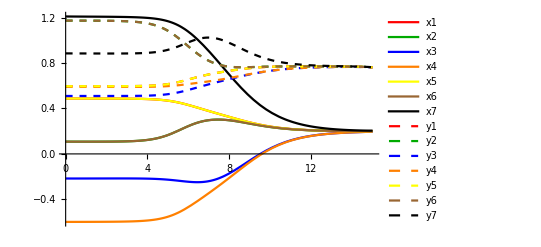

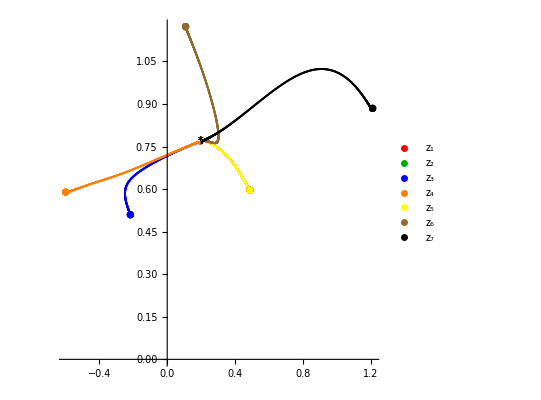

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_ISO7_FP5.csv",N[start],"csv"];*)
(*Export["flowData_ISO7_FP1.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_ISO7_5_to_1_first_direct.csv",valsBetter,"csv"];*)
```

### #2 - First broken flow from 5 to 1

```mathematica
(* Get IC ready *)
ansatz={"0.1561553522550902","-0.01010999998999"}; (* first-ever broken flow 5 to 1 *)
numberOfParams=2;
startIndex=2;
IC = expansion1Crit5v3/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=15;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==0.487204,y1[0]==0.595906,x2[0]==0.108063,y2[0]==1.1727,x3[0]==-0.216296,y3[0]==0.509702,x4[0]==-0.598071,y4[0]==0.589449,x5[0]==0.487204,y5[0]==0.595906,x6[0]==0.108063,y6[0]==1.1727,x7[0]==1.20928,y7[0]==0.884435}

{{-0.000229407,-0.000152892},{-0.000113013,-0.000102137},{0.00147337,-0.000137841},{0.00078827,0.0000305054},{-0.000229401,-0.000152891},{-0.000113016,-0.000102139},{-0.00081593,-0.000506955}}

NDSolve::precw: The precision of the differential equation ({{Divide[16 Cosh[Divide[Log[2] + Log[y1[r]], 2] + Divide[<<2>>] + Divide[<<2>>] + <<3>> + Divide[Log[2] + Log[y7[r]], 2]] <<2>> Power[y1[r], 2], <<1>>] + <<276>> == 0, <<27>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

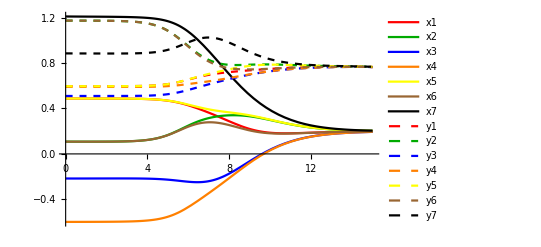

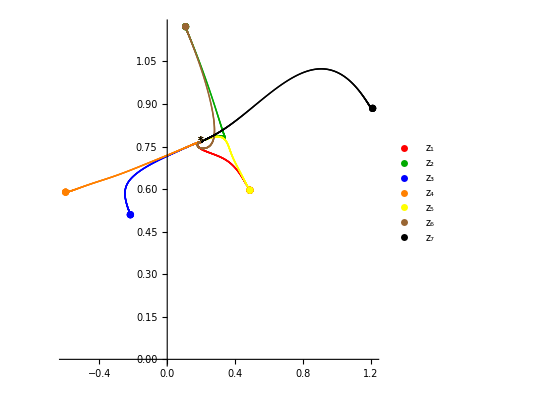

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_ISO7_FP5.csv",N[start],"csv"];*)
(*Export["flowData_ISO7_FP1.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_ISO7_5_to_1_first_broken.csv",valsBetter,"csv"];*)
```

## Broken version of 5 - 1 flow

```mathematica
(* Get IC ready *)
IC = expansion1Crit5v3/.getAlphaRule[finalValues];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC-fpSigma]
(* Solve - rmax is for the range of r *)
rmax=finalRmax;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],40,(distance=10^(8);Print["Blew up!"])];
```

{x1[0]==0.487204,y1[0]==0.595906,x2[0]==0.108063,y2[0]==1.1727,x3[0]==-0.216296,y3[0]==0.509702,x4[0]==-0.598071,y4[0]==0.589449,x5[0]==0.487204,y5[0]==0.595906,x6[0]==0.108063,y6[0]==1.1727,x7[0]==1.20928,y7[0]==0.884435}

{0.000229407,0.000152892,0.000113013,0.000102137,0.00147337,0.000137841,0.00078827,0.0000305054,0.000229401,0.000152891,0.000113016,0.000102139,0.00081593,0.000506955}

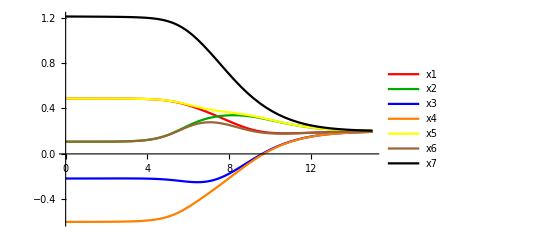

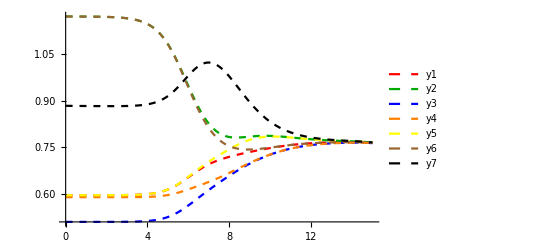

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
plotISO7G2=ListPlot[{#}&/@ISO7G2cut,PlotStyle->Purple,PlotMarkers->"G"];
(* Show desired plots *)
Show[plotReScalars]
Show[plotImScalars]
Show[plotComplexScalars,plotStart,plotGoal]
```

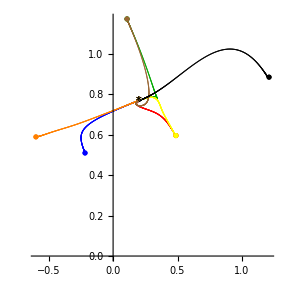

```mathematica
goodIC={-0.03337623917606312,0.6286528322153423,0.6354917555268917,0.5249481306246754,-0.02561538669653529,0.46086075785657243,-0.7300701393700112,1.4154294119441244,-0.03337623917606028,0.6286528322153448,0.6354917555268865,0.5249481306246747,0.6413316784718337,0.9967889301358085}
```

{-0.0333762,0.628653,0.635492,0.524948,-0.0256154,0.460861,-0.73007,1.41543,-0.0333762,0.628653,0.635492,0.524948,0.641332,0.996789}

## #3 Older flows:

### #3.1 - Flows starting from the 2nd FP

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=2;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit2=getExpansion[fpSigma, eigenvals,eigenvecs];
expansion1Crit2v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit2RescaledRvalue=expansion1Crit2v0/.{α1->1}//N;
```

{-1.56155,-0.561553,0.666667,0.666667,0.666667,1.,1.,1.,1.,1.33333,1.33333,1.33333,2.56155,3.56155}

```mathematica
hey=expansion1Crit2//N//cut;
hey[[3]]
hey[[4]]
hey[[7]]
```

{0.5-0.15518 2.71828^(2.05512 rvalue) α1+0.36137 2.71828^(0.739045 rvalue) α2,0.866025+0.268779 2.71828^(2.05512 rvalue) α1+0.208637 2.71828^(0.739045 rvalue) α2}

{0.5-0.15518 2.71828^(2.05512 rvalue) α1+0.36137 2.71828^(0.739045 rvalue) α2,0.866025+0.268779 2.71828^(2.05512 rvalue) α1+0.208637 2.71828^(0.739045 rvalue) α2}

{0.5-0.15518 2.71828^(2.05512 rvalue) α1+0.36137 2.71828^(0.739045 rvalue) α2,0.866025+0.268779 2.71828^(2.05512 rvalue) α1+0.208637 2.71828^(0.739045 rvalue) α2}

```mathematica
expansion1Crit2Tex=expansion1Crit2/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]]//N;
%//TeXForm;
```

### #3.1 Flow from 2 - 1:

```mathematica
expansion1Crit2RescaledRvalue//cut
```

{{-0.011493 α2,0.707139},{-0.011493 α2,0.707139},{0.499988+0.0120188 α2,0.866046+0.00693906 α2},{0.499988+0.0120188 α2,0.866046+0.00693906 α2},{-0.011493 α2,0.707139},{-0.011493 α2,0.707139},{0.499988+0.0120188 α2,0.866046+0.00693906 α2}}

```mathematica
(* Get IC ready *)
ansatz={"-0.2155592464500001"}; 
numberOfParams=1;
startIndex=2;
IC = expansion1Crit2RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=15;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==0.00247742,y1[0]==0.707139,x2[0]==0.00247742,y2[0]==0.707139,x3[0]==0.497397,y3[0]==0.86455,x4[0]==0.497397,y4[0]==0.86455,x5[0]==0.00247742,y5[0]==0.707139,x6[0]==0.00247742,y6[0]==0.707139,x7[0]==0.497397,y7[0]==0.86455}

{{0.00247742,0.0000327097},{0.00247742,0.0000327097},{-0.00260281,-0.00147493},{-0.00260281,-0.00147493},{0.00247742,0.0000327097},{0.00247742,0.0000327097},{-0.00260281,-0.00147493}}

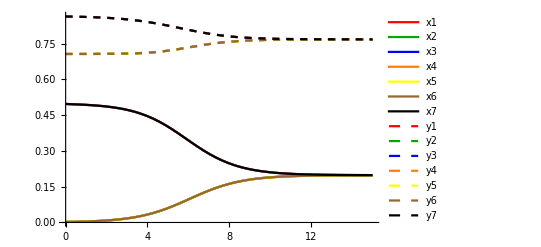

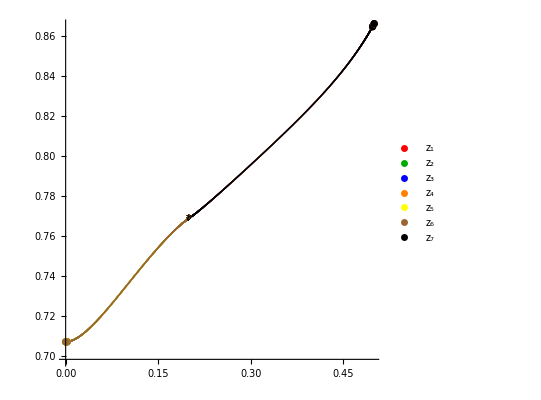

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_ISO7_2_to_1.csv",valsBetter,"csv"];*)
```

### #3.2 - Flows starting from the 3rd FP

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=3;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit3=getExpansion[N[fpSigma], N[eigenvals],N[eigenvecs]];
expansion1Crit3v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit3RescaledRvalue=expansion1Crit3v0/.{α3->α2}//N;
```

{-1.73205,-0.732051,-0.732051,0.267949,1.,1.,1.,1.,1.,1.,1.73205,2.73205,2.73205,3.73205}

```mathematica
expansion1Crit3RescaledRvalue//cut;
```

```mathematica
expansion1Crit3Tex=expansion1Crit3/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]];
%//TeXForm
```

\left\{0.104502 A_1 e^{2.41233 r}-0.557678 A_2 e^{1.01957 r}-0.557678 A_3 e^{1.01957 r}-0.39685,0.390007 A_1 e^{2.41233 r}+0.149429 A_2 e^{1.01957 r}+0.149429 A_3 e^{1.01957 r}+0.687365,-0.104502 A_1 e^{2.41233
   r}+0.321975 A_3 e^{1.01957 r}+0.39685,0.390007 A_1 e^{2.41233 r}+0.086273 A_3 e^{1.01957 r}+0.687365,-0.104502 A_1 e^{2.41233 r}+0.321975 A_2 e^{1.01957 r}+0.39685,0.390007 A_1 e^{2.41233 r}+0.086273 A_2 e^{1.01957
   r}+0.687365,-0.142753 A_1 e^{2.41233 r}+0.086273 A_2 e^{1.01957 r}+0.086273 A_3 e^{1.01957 r}+0.793701,0.0382504 A_1 e^{2.41233 r}+0.321975 A_2 e^{1.01957 r}+0.321975 A_3 e^{1.01957 r}+1.37473,0.104502 A_1 e^{2.41233
   r}-0.557678 A_2 e^{1.01957 r}-0.557678 A_3 e^{1.01957 r}-0.39685,0.390007 A_1 e^{2.41233 r}+0.149429 A_2 e^{1.01957 r}+0.149429 A_3 e^{1.01957 r}+0.687365,-0.104502 A_1 e^{2.41233 r}+0.321975 A_3 e^{1.01957
   r}+0.39685,0.390007 A_1 e^{2.41233 r}+0.086273 A_3 e^{1.01957 r}+0.687365,-0.104502 A_1 e^{2.41233 r}+0.321975 A_2 e^{1.01957 r}+0.39685,0.390007 A_1 e^{2.41233 r}+0.086273 A_2 e^{1.01957 r}+0.687365\right\}

```mathematica
(* Get IC ready *)
ansatz={"3.5709160396","-0.2920101000000001"}; (*  359, 0 *)
numberOfParams=2;
startIndex=1;
IC = expansion1Crit3RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=15;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==-0.393868,y1[0]==0.686588,x2[0]==0.395986,y2[0]==0.687155,x3[0]==0.395986,y3[0]==0.687155,x4[0]==0.793232,y4[0]==1.37301,x5[0]==-0.393868,y5[0]==0.686588,x6[0]==0.395986,y6[0]==0.687155,x7[0]==0.395986,y7[0]==0.687155}

{{0.00298185,-0.000776633},{-0.000864761,-0.000209361},{-0.000864761,-0.000209361},{-0.000468063,-0.0017163},{0.00298185,-0.000776633},{-0.000864761,-0.000209361},{-0.000864761,-0.000209361}}

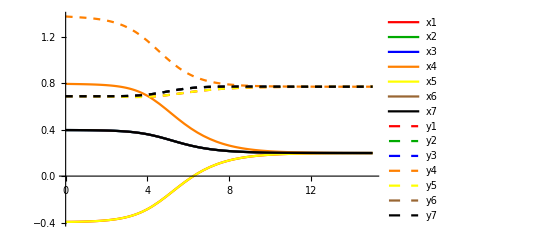

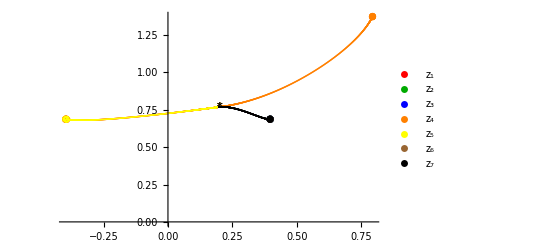

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotStart,plotIC,plotGoal,plotComplexScalars]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_ISO7_3_to_1.csv",valsBetter,"csv"];*)
```

### #3.2 - To finish if I have extra time/become extra bored? Flows starting from the 3rd FP, but break symmetry

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=3;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit3v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit3RescaledRvalue=expansion1Crit3v0/.{α3->-0.2}//N;
```

{-1.73205,-0.732051,-0.732051,0.267949,1.,1.,1.,1.,1.,1.,1.73205,2.73205,2.73205,3.73205}

```mathematica
expansion1Crit3RescaledRvalue//cut
```

{{-0.395362+1.56484×10^-6 α1-0.00509617 α2,0.686966+5.84005×10^-6 α1+0.00136551 α2},{0.395991-1.56484×10^-6 α1,0.687135+5.84005×10^-6 α1},{0.39685-1.56484×10^-6 α1+0.00294227 α2,0.687365+5.84005×10^-6 α1+0.00078838 α2},{0.79347-2.13761×10^-6 α1+0.00078838 α2,1.37387+5.7277×10^-7 α1+0.00294227 α2},{-0.395362+1.56484×10^-6 α1-0.00509617 α2,0.686966+5.84005×10^-6 α1+0.00136551 α2},{0.395991-1.56484×10^-6 α1,0.687135+5.84005×10^-6 α1},{0.39685-1.56484×10^-6 α1+0.00294227 α2,0.687365+5.84005×10^-6 α1+0.00078838 α2}}

```mathematica
(* Get IC ready *)
ansatz={"3.5709160396","-0.2920101000000001"}; (*  359, 0 *)
numberOfParams=2;
startIndex=1;
IC = expansion1Crit3RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=5;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==-0.394337,y1[0]==0.686714,x2[0]==0.396256,y2[0]==0.687228,x3[0]==0.395986,y3[0]==0.687155,x4[0]==0.793305,y4[0]==1.37328,x5[0]==-0.394337,y5[0]==0.686714,x6[0]==0.396256,y6[0]==0.687228,x7[0]==0.395986,y7[0]==0.687155}

{{0.00251295,-0.000650992},{-0.000594043,-0.000136822},{-0.000864761,-0.000209361},{-0.000395524,-0.00144558},{0.00251295,-0.000650992},{-0.000594043,-0.000136822},{-0.000864761,-0.000209361}}

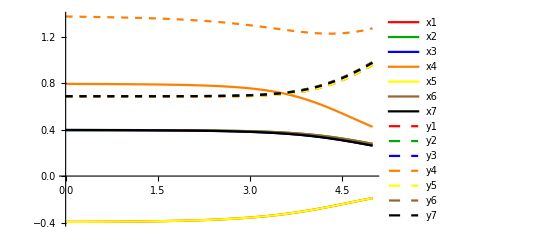

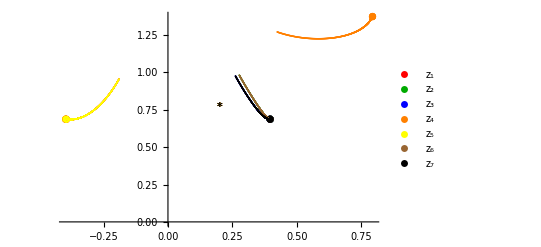

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotStart,plotIC,plotGoal,plotComplexScalars]
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α1,α2}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|8→<|{3.5714,-0.29201}→0.21886670529722910589815919116643472714920722141|>|>

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion1Crit3RescaledRvalue;
flowEqs=flowEqs1;
(* --- Initializations --- *)
numberOfParams=2;
startIndex=1;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=15;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={17};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={0.000001,0.01};
rmaxIncrementList={1, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

## Check the results

```mathematica
Keys[allExplorations]
```

{11,12,13,14}

```mathematica
finalRmax=Max[Keys[allExplorations]]
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final];
finalDistance=final[finalValues];
NumberForm[finalValues,20]
```

15

{3.5709160396,-0.2920101000000001}

```mathematica
(*Put[allExplorations,"explorations_ISO7_5_to_1_family1"]*)
(*Put[expansion1Crit5v3,"expansion1Crit5v3"]*)
```

### #3.2 - Flows starting from the 3rd FP, but break symmetry

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=4;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit3v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit3RescaledRvalue=expansion1Crit3v0//N;
```

{-1.44949,-1.44949,0.,0.,0.333333,0.333333,0.333333,1.66667,1.66667,1.66667,2.,2.,3.44949,3.44949}

```mathematica
test=expansion1Crit3RescaledRvalue//cut;
```

```mathematica
test[[1]]
test[[2]]
test[[5]]
test[[6]]
```

{0.433013-7.00116×10^-6 α1-0.0000147965 α2,0.559017+0.0000396925 α1+0.0000367928 α2}

{0.433013-7.00116×10^-6 α1-0.0000147965 α2,0.559017+0.0000396925 α1+0.0000367928 α2}

{0.433013-7.00116×10^-6 α1-0.0000147965 α2,0.559017+0.0000396925 α1+0.0000367928 α2}

«1 more identical outputs»

```mathematica
test[[3]]
test[[4]]
test[[7]]
```

{-0.25+0.0000136066 α2,0.968246+0.0000107698 α1}

{-0.25+0.0000136066 α2,0.968246+0.0000107698 α1}

{-0.25+0.0000136066 α2,0.968246+0.0000107698 α1}

```mathematica
(* Get IC ready *)
ansatz={"3.5709160396","-0.2920101000000001"}; (*  359, 0 *)
numberOfParams=2;
startIndex=1;
IC = expansion1Crit3RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=5;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==-0.394337,y1[0]==0.686714,x2[0]==0.396256,y2[0]==0.687228,x3[0]==0.395986,y3[0]==0.687155,x4[0]==0.793305,y4[0]==1.37328,x5[0]==-0.394337,y5[0]==0.686714,x6[0]==0.396256,y6[0]==0.687228,x7[0]==0.395986,y7[0]==0.687155}

{{0.00251295,-0.000650992},{-0.000594043,-0.000136822},{-0.000864761,-0.000209361},{-0.000395524,-0.00144558},{0.00251295,-0.000650992},{-0.000594043,-0.000136822},{-0.000864761,-0.000209361}}

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotStart,plotIC,plotGoal,plotComplexScalars]
```

-Graphics-

-Graphics-

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α1,α2}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|8→<|{3.5714,-0.29201}→0.21886670529722910589815919116643472714920722141|>|>

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion1Crit3RescaledRvalue;
flowEqs=flowEqs1;
(* --- Initializations --- *)
numberOfParams=2;
startIndex=1;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=15;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={17};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={0.000001,0.01};
rmaxIncrementList={1, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

## Check the results

```mathematica
Keys[allExplorations]
```

{11,12,13,14}

```mathematica
finalRmax=Max[Keys[allExplorations]]
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final];
finalDistance=final[finalValues];
NumberForm[finalValues,20]
```

15

{3.5709160396,-0.2920101000000001}

```mathematica
(*Put[allExplorations,"explorations_ISO7_5_to_1_family1"]*)
(*Put[expansion1Crit5v3,"expansion1Crit5v3"]*)
```

### # 3.4 - Flows from 4th (didn’t discuss)

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=4;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit4=getExpansion[N[fpSigma], N[eigenvals],N[eigenvecs]];
expansion1Crit4v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit4RescaledRvalue=expansion1Crit4v0/.{α3->α2}//N;
```

{-1.44949,-1.44949,0.,0.,0.333333,0.333333,0.333333,1.66667,1.66667,1.66667,2.,2.,3.44949,3.44949}

```mathematica
hey=expansion1Crit4//cut//N;
hey[[1]]
hey[[2]]
hey[[5]]
hey[[6]]
```

{0.433013-0.0846158 2.71828^(2.04114 rvalue) α1-0.17883 2.71828^(2.04114 rvalue) α2,0.559017+0.479722 2.71828^(2.04114 rvalue) α1+0.444676 2.71828^(2.04114 rvalue) α2}

{0.433013-0.0846158 2.71828^(2.04114 rvalue) α1-0.17883 2.71828^(2.04114 rvalue) α2,0.559017+0.479722 2.71828^(2.04114 rvalue) α1+0.444676 2.71828^(2.04114 rvalue) α2}

{0.433013-0.0846158 2.71828^(2.04114 rvalue) α1-0.17883 2.71828^(2.04114 rvalue) α2,0.559017+0.479722 2.71828^(2.04114 rvalue) α1+0.444676 2.71828^(2.04114 rvalue) α2}

«1 more identical outputs»

```mathematica
expansion1Crit4Tex=expansion1Crit4/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]];
%//TeXForm
```

\left\{-0.0846158 A_1 e^{2.04114 r}-0.17883 A_2 e^{2.04114 r}+0.433013,0.479722 A_1 e^{2.04114 r}+0.444676 A_2 e^{2.04114 r}+0.559017,-0.0846158 A_1 e^{2.04114 r}-0.17883 A_2 e^{2.04114 r}+0.433013,0.479722 A_1 e^{2.04114
   r}+0.444676 A_2 e^{2.04114 r}+0.559017,0.164449 A_2 e^{2.04114 r}-0.25,0.130164 A_1 e^{2.04114 r}+0.968246,0.164449 A_2 e^{2.04114 r}-0.25,0.130164 A_1 e^{2.04114 r}+0.968246,-0.0846158 A_1 e^{2.04114 r}-0.17883 A_2
   e^{2.04114 r}+0.433013,0.479722 A_1 e^{2.04114 r}+0.444676 A_2 e^{2.04114 r}+0.559017,-0.0846158 A_1 e^{2.04114 r}-0.17883 A_2 e^{2.04114 r}+0.433013,0.479722 A_1 e^{2.04114 r}+0.444676 A_2 e^{2.04114
   r}+0.559017,0.164449 A_2 e^{2.04114 r}-0.25,0.130164 A_1 e^{2.04114 r}+0.968246\right\}

### # 3.4 - Flows from 6th (didn’t find :’( )

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=6;
goalindex=1;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltas//FullSimplify//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit6=getExpansion[N[fpSigma], N[eigenvals],N[eigenvecs]];
expansion1Crit6v0=getExpansion[fpSigma, eigenvals,eigenvecs]/.{rvalue->Log[10^(-2)]};
expansion1Crit6RescaledRvalue=expansion1Crit6v0/.{α3->α2}//N;
```

{-2.12016,-1.97264,-1.6338,-1.02252,-1.00507,0.469696,0.603625,1.39638,1.53031,3.00508,3.02252,3.6338,3.97264,4.12016}

```mathematica
test=expansion1Crit6//cut;
test[[1]]
test[[5]]
```

{-0.11026+0.386828 ⅇ^(3.65229 rvalue) α1+0.0461372 ⅇ^(3.39817 rvalue) α2+0.0364767 ⅇ^(2.81446 rvalue) α3+0.320631 ⅇ^(1.76145 rvalue) α4-0.0888923 ⅇ^(1.73139 rvalue) α5,0.762911-0.194545 ⅇ^(3.65229 rvalue) α1-0.401245 ⅇ^(3.39817 rvalue) α2+0.121247 ⅇ^(2.81446 rvalue) α3+0.323186 ⅇ^(1.76145 rvalue) α4+0.0874768 ⅇ^(1.73139 rvalue) α5}

{-0.11026+0.386828 ⅇ^(3.65229 rvalue) α1+0.0461372 ⅇ^(3.39817 rvalue) α2+0.0364767 ⅇ^(2.81446 rvalue) α3-0.320631 ⅇ^(1.76145 rvalue) α4-0.0888923 ⅇ^(1.73139 rvalue) α5,0.762911-0.194545 ⅇ^(3.65229 rvalue) α1-0.401245 ⅇ^(3.39817 rvalue) α2+0.121247 ⅇ^(2.81446 rvalue) α3-0.323186 ⅇ^(1.76145 rvalue) α4+0.0874768 ⅇ^(1.73139 rvalue) α5}

```mathematica
expansion1Crit6TeX=expansion1Crit6/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]];
%//TeXForm
```

\left\{0.386828 A_1 e^{3.65229 r}+0.0461372 A_2 e^{3.39817 r}+0.0364767 A_3 e^{2.81446 r}+0.320631 A_4 e^{1.76145 r}-0.0888923 A_5 e^{1.73139 r}-0.11026,-0.194545 A_1 e^{3.65229 r}-0.401245 A_2 e^{3.39817 r}+0.121247 A_3
   e^{2.81446 r}+0.323186 A_4 e^{1.76145 r}+0.0874768 A_5 e^{1.73139 r}+0.762911,-0.226951 A_1 e^{3.65229 r}+0.302688 A_2 e^{3.39817 r}-0.131328 A_3 e^{2.81446 r}-0.540451 A_4 e^{1.76145 r}+0.409767 A_5 e^{1.73139
   r}+0.836439,-0.114444 A_1 e^{3.65229 r}+0.17518 A_2 e^{3.39817 r}+0.492662 A_3 e^{2.81446 r}-0.0256776 A_4 e^{1.76145 r}-0.0226078 A_5 e^{1.73139 r}+0.390702,-0.657371 A_1 e^{3.65229 r}-0.120826 A_2 e^{3.39817
   r}+0.0019231 A_3 e^{2.81446 r}-0.679593 A_5 e^{1.73139 r}-0.402122,-0.0387341 A_1 e^{3.65229 r}+0.240211 A_2 e^{3.39817 r}+0.664027 A_3 e^{2.81446 r}+0.0263984 A_5 e^{1.73139 r}+0.312003,0.00348252 A_1 e^{3.65229
   r}+0.199985 A_2 e^{3.39817 r}+0.030437 A_3 e^{2.81446 r}-0.264003 A_5 e^{1.73139 r}-0.944882,-0.104856 A_1 e^{3.65229 r}+0.289221 A_2 e^{3.39817 r}-0.0055178 A_3 e^{2.81446 r}+0.152541 A_5 e^{1.73139
   r}+1.44057,0.386828 A_1 e^{3.65229 r}+0.0461372 A_2 e^{3.39817 r}+0.0364767 A_3 e^{2.81446 r}-0.320631 A_4 e^{1.76145 r}-0.0888923 A_5 e^{1.73139 r}-0.11026,-0.194545 A_1 e^{3.65229 r}-0.401245 A_2 e^{3.39817
   r}+0.121247 A_3 e^{2.81446 r}-0.323186 A_4 e^{1.76145 r}+0.0874768 A_5 e^{1.73139 r}+0.762911,-0.226951 A_1 e^{3.65229 r}+0.302688 A_2 e^{3.39817 r}-0.131328 A_3 e^{2.81446 r}+0.540451 A_4 e^{1.76145 r}+0.409767 A_5
   e^{1.73139 r}+0.836439,-0.114444 A_1 e^{3.65229 r}+0.17518 A_2 e^{3.39817 r}+0.492662 A_3 e^{2.81446 r}+0.0256776 A_4 e^{1.76145 r}-0.0226078 A_5 e^{1.73139 r}+0.390702,0.0402257 A_1 e^{3.65229 r}-0.482697 A_2
   e^{3.39817 r}-0.0264938 A_3 e^{2.81446 r}-0.0365176 A_5 e^{1.73139 r}+0.740186,0.222625 A_1 e^{3.65229 r}-0.0138388 A_2 e^{3.39817 r}+0.0736079 A_3 e^{2.81446 r}+0.27424 A_5 e^{1.73139 r}+1.15257\right\}

## Older code for this flow:

```mathematica
(* Get linearisation around the fixed point. α12 and α13 give same deviations, so put α13 = 0 *)
expansion1Crit3=getExpansion[critPoint,eigenvals,eigenvecs]/.{α13->0};
```

```mathematica
expansion1Crit3[[8]]
```

1.37473-0.0780843 α12-0.0382504 α5

```mathematica
(* The constant that needs to be finetuned: *)
alphaValue=-920.5521; (* -920.5521, for rmax = 9 and negative alpha 5 *)
eps=10^-4;
IC=expansion1Crit3/.{α5->-1*eps,α12->alphaValue*eps};
(* IMPOSE a symmetry *)
IC[[1]]=-IC[[3]]; (* z1 -> -z2Bar *)
IC[[2]]=IC[[4]];
IC[[5]]=IC[[3]]; (* z3 -> z2 *)
IC[[6]]=IC[[4]];
IC[[7]]=2*IC[[3]]; (* z4 -> 2*z2 *)
IC[[8]]=2*IC[[4]];
(* Now make sure that z5 = z1, z6 = z2, z7 = z3 *)
IC[[9]]=IC[[1]]; (* z5 -> z1 *)
IC[[10]]=IC[[2]];
IC[[11]]=IC[[3]]; (* z6 -> z2 *)
IC[[12]]=IC[[4]];
IC[[13]]=IC[[5]]; (* z7 -> z3 *)
IC[[14]]=IC[[6]];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist;
deviations=IC-critPoint//Abs//Max (* is this a problem??? *)
```

0.0793958

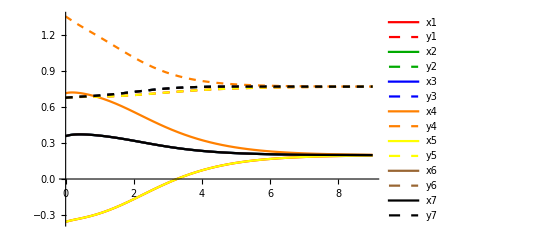

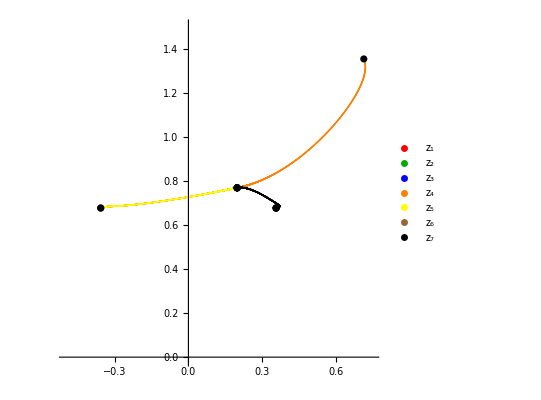

```mathematica
(* Solve - rmax is for the range of r *)
rmax=9;
solution = NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"}]; (*,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15*)
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,AspectRatio->1,PlotRange->{{-0.5,0.75},{-0.01,1.5}}, PlotStyle->colorsCF,PlotLegends->{"z_1","z_2","z_3","z_4","z_5","z_6","z_7"}];
plotComplexScalarsv2=ListPlot[solutionsComplex,PlotRange->{{-0.5,0.6},{-0.01,1.8}}];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
plotIC=ListPlot[IC//cut,PlotStyle->colorsRF];
(* Show desired plots *)
Show[plotAllScalars]
Show[plotComplexScalars,plotIC,plotGoal]
```

## Q: Can I find another new flow?

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=5;
goalindex=6;
(* Define expansion: *)
start=critPoints1Sigma[[index]];
jac=jacobians1[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints1Sigma[[goalindex]];
target=goal;
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues1[[index]]/.{g->1};
L=lgValues[[index]];
deltas=eigenvals*(-L);
deltasNum=deltas//N;
deltasNum//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints1Sigma[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians1[[index]]/.{g->1,m->1}; 
{eigenvals,eigenvecs}=jac//Eigensystem//Chop//FS;
expansion1Crit5=getExpansion[fpSigma,eigenvals,eigenvecs]//N;
```

{-1.72714,-1.71693,-1.04408,-0.241802,0.708313,0.877535,0.888892,1.11111,1.12246,1.29169,2.2418,3.04408,3.71693,3.72714}

New deltas at 5th and 6th critical point: to put in thesis:

```mathematica
(* 5th point: *)
{"-1.727136538","-1.716927592","-1.044079105","-0.2418020914","0.7083131935","0.8775354779","0.888891756","1.111108283","1.122464561","1.291686846","2.241802131","3.044079144","3.716927631","3.727136577"};
(* 6th point *)
{"-2.120159784","-1.972640361","-1.633796002","-1.022522898","-1.005074845","0.4696956994","0.6036253116","1.396375685","1.530305297","3.005075842","3.022523894","3.633796999","3.972641357","4.120160781"};
```

```mathematica
(* Another expansion: *)
rvalueHere=Log[10^-1];
check=expansion1Crit5/.{rvalue->rvalueHere}//cut;
{check[[1]],check[[5]]};
expansion1Crit5RescaledRvaluev2=expansion1Crit5/.{α1->0.00001,α2->0,rvalue->rvalueHere};
expansion1Crit5RescaledRvalue=expansion1Crit5RescaledRvaluev2/.{α3->α2,α4->α3};
he=expansion1Crit5RescaledRvalue//cut;
```

```mathematica
expansion1Crit5RescaledRvalue;
```

```mathematica
{he[[1]],he[[5]]};
{he[[2]],he[[6]]};
```

## Find a good shooting guess from experience

```mathematica
getStartFromAngles[radius_,thetas_]:=(
emptyVec=Table[0,14];
For[i=1,i<8,i++,
(
emptyVec[[2i-1]]=radius*Cos[thetas[[i]]Degree];
emptyVec[[2i]]=radius*Sin[thetas[[i]]Degree];
)];
Return[emptyVec];
)
```

```mathematica
expansion1Crit6v2=expansion1Crit6/.{α4->0,rvalue->rvalueHere};
expansion1Crit6AllAlphas=expansion1Crit6v2/.{α5->α4};
eps=0.01;
goodDirection=fpSigma+eps*(startingTarget-fpSigma)//N;
(*goodDirection[[14]]=fpSigma[[14]]-0.1;*)
goodDirection;
```

```mathematica
eps=0.01;
startAngles=getStartFromAngles[eps,{30, 90, 0, -90, 30, 90, -90}];
goodDirection=fpSigma+eps*(startAngles-fpSigma)//N;
```

```mathematica
Abs[goodDirection-fpSigma]//cut
```

{{0.00119657,0.00766331},{0.00836439,0.00380702},{0.00412122,0.00312003},{0.00944882,0.0145057},{0.00119657,0.00766331},{0.00836439,0.00380702},{0.00740186,0.0116257}}

```mathematica
myDeviations=expansion1Crit6AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify;
sol=NSolve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α1,α2,α3,α4}];
solValue=sol[[1]]
```

{α1→37.9563,α2→17.6976,α3→-5.3541,α4→-1.23878}

```mathematica
pointFound=myDeviations/.solValue
Abs[pointFound-fpSigma]
```

{-0.104951,0.755431,0.828383,0.387401,-0.392965,0.307253,-0.937651,1.43829,-0.104951,0.755431,0.828383,0.387401,0.73817,1.14745}

{0.00530961,0.00748003,0.00805643,0.00330085,0.00915685,0.00475037,0.00723135,0.00228348,0.00530961,0.00748003,0.00805643,0.00330085,0.00201621,0.00511401}

#### Step 1) Find a good initial point by hand

```mathematica
(* Define expansion: *)
expansion1Crit6RescaledRvaluev2=expansion1Crit6 /. {α5->-0.0001,rvalue ->rvalueHere};
expansion1Crit6RescaledRvalue=expansion1Crit6RescaledRvaluev2 ;
expansion1Crit6NoBreaking=expansion1Crit6RescaledRvalue/. {α4->0};
```

```mathematica
(* Get IC ready *)
ansatz={0,0};
numberOfParams=2;
startIndex=2;
IC = expansion1Crit5RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=4;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];
```

{x1[0]==0.487433,y1[0]==0.596059,x2[0]==0.108176,y2[0]==1.1728,x3[0]==-0.21777,y3[0]==0.50984,x4[0]==-0.598859,y4[0]==0.589419,x5[0]==0.487433,y5[0]==0.596059,x6[0]==0.108176,y6[0]==1.1728,x7[0]==1.2101,y7[0]==0.884942}

{{2.39275×10^-9,-1.29438×10^-8},{1.45797×10^-9,-2.94288×10^-9},{-2.0848×10^-9,-1.62566×10^-8},{-1.6752×10^-9,-1.31746×10^-8},{2.39275×10^-9,-1.29438×10^-8},{1.45797×10^-9,-2.94288×10^-9},{4.88375×10^-9,-6.66309×10^-9}}

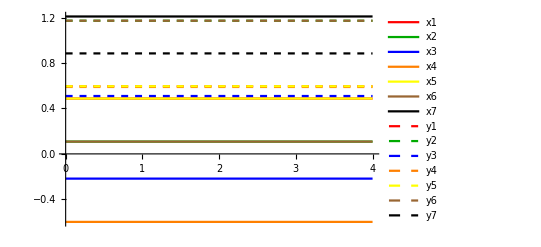

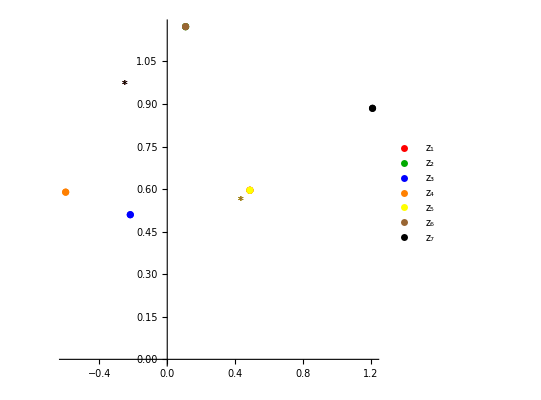

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotStart,plotGoal]
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α2,α3}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|4→<|{0,0}→1.89441788321341298921956231515334708601417860861|>|>

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion1Crit5RescaledRvalue;
flowEqs=flowEqs1;
(* --- Initializations --- *)
numberOfParams=2;
startIndex=2;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=7;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={17};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={0.001,0.01};
rmaxIncrementList={0.2, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

```mathematica
test=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/explorations_ISO7_5_to_1"];
test2=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/explorations_ISO7_5_to_1_cont"];
```

## Check the results

```mathematica
Keys[allExplorations]
```

{4,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.}

```mathematica
finalRmax=Max[Keys[allExplorations]];
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final];
finalDistance=final[finalValues];
NumberForm[finalValues,20]
```

{0.004743999999999998,0.11321}

```mathematica
(* Get IC ready *)
IC = expansion1Crit5RescaledRvalue/.getAlphaRule[finalValues];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC-fpSigma]
(* Solve - rmax is for the range of r *)
rmax=finalRmax;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],40,(distance=10^(8);Print["Blew up!"])];
```

{x1[0]==0.492466,y1[0]==0.600345,x2[0]==0.111947,y2[0]==1.17409,x3[0]==-0.256143,y3[0]==0.513749,x4[0]==-0.616744,y4[0]==0.588475,x5[0]==0.492466,y5[0]==0.600345,x6[0]==0.111947,y6[0]==1.17409,x7[0]==1.23024,y7[0]==0.898334}

{0.00503276,0.00428559,0.00377062,0.00128785,0.0383733,0.00390872,0.017885,0.000943834,0.00503276,0.00428559,0.00377062,0.00128785,0.0201418,0.0133915}

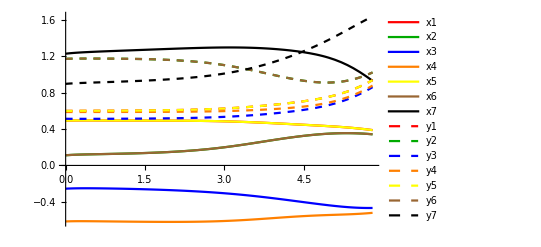

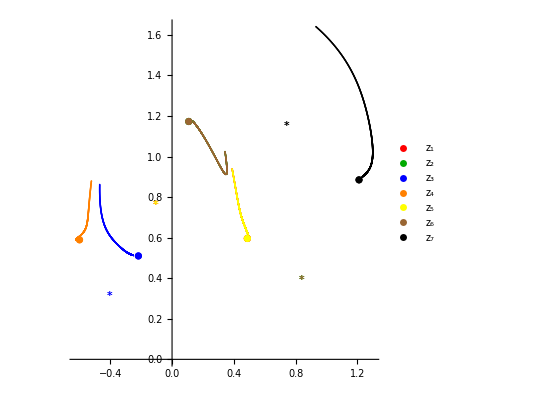

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
plotISO7G2=ListPlot[{#}&/@ISO7G2cut,PlotStyle->Purple,PlotMarkers->"G"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotStart,plotGoal]
```

```mathematica
goodIC={-0.03337623917606312,0.6286528322153423,0.6354917555268917,0.5249481306246754,-0.02561538669653529,0.46086075785657243,-0.7300701393700112,1.4154294119441244,-0.03337623917606028,0.6286528322153448,0.6354917555268865,0.5249481306246747,0.6413316784718337,0.9967889301358085}
```

{-0.0333762,0.628653,0.635492,0.524948,-0.0256154,0.460861,-0.73007,1.41543,-0.0333762,0.628653,0.635492,0.524948,0.641332,0.996789}

## Extra: symmetries and copies of the vacua

```mathematica
(* Look at the superpotential, we rescale g just for simplicity (doesn't matter). Only cubic terms! *)
superpotISO7=superpotGuarino/.{g->1/2,m->1/2}//Expand
```

1+z1 z2 z3+z1 z4 z5+z2 z4 z6+z3 z5 z6+z3 z4 z7+z2 z5 z7+z1 z6 z7

```mathematica
ourSuperpot1=superpot1/.{g->1/2}
```

1+z1 z2 z3+z3 z4 z5+z2 z4 z6+z1 z5 z6+z1 z4 z7+z2 z5 z7+z3 z6 z7

Find all permutations of the seven scalars, which leave this superpotential invariant

```mathematica
allPermutations=AlternatingGroup[7]//GroupElements;
allPermutations//Dimensions
```

{2520}

```mathematica
(* Go over all permutations: *)
symmPerm={};
For[i=1,i<Length[allPermutations]+1,i++,
(
perm=allPermutations[[i]];
zPerm=Permute[z,perm];
newSuperpotISO7=superpotISO7/.Table[z[[j]]->zPerm[[j]],{j,1,7}];
diff=superpotISO7-newSuperpotISO7//Simplify;
If[diff==0,AppendTo[symmPerm,perm]];
)];
```

```mathematica
symmPerm//Dimensions
```

{168}

Sign flips: first get all sign flips (exclude 0 and 7 sign flips: 0 = trivial, 7 = non-invariant)

```mathematica
(* Get all vectors containing the sign flips: *)
allSignFlipVectors={};
For[i=1,i<Length[allPermutations]+1,i++,
(
perm=allPermutations[[i]];
(* 1 minus sign *)
vector={-1,1,1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 2 minus sign *)
vector={-1,-1,1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 3 minus sign *)
vector={-1,-1,-1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 4 minus sign *)
vector={-1,-1,-1,-1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 5 minus sign *)
vector={-1,-1,-1,-1,-1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 6 minus sign *)
vector={-1,-1,-1,-1,-1,-1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
)];
allSignFlipVectors=allSignFlipVectors//DeleteDuplicates;
```

```mathematica
allSignFlipVectors//Dimensions
```

{126,7}

Now check which ones leave the superpotential invariant

```mathematica
goodSignFlipVectors={};
For[a=1,a<Length[allSignFlipVectors]+1,a++,
(
signFlipVector=allSignFlipVectors[[a]];
newZ=signFlipVector*z;
newSuperpotISO7=superpotISO7/.Table[z[[i]]->newZ[[i]],{i,1,7}];
diff=superpotISO7-newSuperpotISO7;
If[diff==0,AppendTo[goodSignFlipVectors,signFlipVector]];
)];
```

```mathematica
goodSignFlipVectors//Dimensions
```

{7,7}

```mathematica
goodSignFlipVectors
```

{{-1,-1,1,-1,1,1,-1},{-1,-1,1,1,-1,-1,1},{-1,1,-1,-1,1,-1,1},{-1,1,-1,1,-1,1,-1},{1,-1,-1,-1,-1,1,1},{1,-1,-1,1,1,-1,-1},{1,1,1,-1,-1,-1,-1}}

```mathematica
(* Are they the same as SO(8) --- Watch out: need to swap 1 and 3 to agree! *)
goodSignFlipVectorsPermuted=Table[Permute[goodSignFlipVectors[[h]],Cycles[{{1,3}}]],{h,1,Length[goodSignFlipVectors]}]
```

{{1,-1,-1,-1,1,1,-1},{1,-1,-1,1,-1,-1,1},{-1,1,-1,-1,1,-1,1},{-1,1,-1,1,-1,1,-1},{-1,-1,1,-1,-1,1,1},{-1,-1,1,1,1,-1,-1},{1,1,1,-1,-1,-1,-1}}

```mathematica
(* Here we copied the sign flips obtained in the SO(8) notebook: *)
signFlipsSO8={{-1,-1,-1,1,1,1,-1},{-1,-1,1,1,-1,-1,1},{-1,1,-1,-1,-1,1,1},{-1,1,1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,1,-1},{1,1,-1,1,-1,-1,-1}};
```

```mathematica
(* They are NOT the same! *)
goodSignFlipVectors==signFlipsSO8
goodSignFlipVectorsPermuted==signFlipsSO8
```

False

False

Now find as many inequivalent copies as possible:

```mathematica
allCritLists={};
For[b=1,b<8,b++,
(
(* Do one additional entry where we consider an arbitrary z , otherwise take a crit point *)
If[b==7,aCrit=z,aCrit=critPoints1[[b]];];
aCritList={aCrit};
(* 1 - get SF *)
SFlist={};
For[a=1,a<Length[goodSignFlipVectors]+1,a++,
(
(* get current sign flip *)
signflip=goodSignFlipVectors[[a]];
(* flip the crit *)
newCrit=signflip*aCrit;
AppendTo[aCritList,newCrit];
AppendTo[SFlist,newCrit];
)];
(* 2 - get P *)
Plist={};
For[a=1,a<Length[symmPerm]+1,a++,
(
(* get current permutation *)
perm=symmPerm[[a]];
(* permute the crit *)
newCrit=Permute[aCrit,perm];
AppendTo[aCritList,newCrit];
AppendTo[Plist,newCrit];
)];
(* 3 - get SF[P] *)
For[p=1,p<Length[Plist]+1,p++,
(
currentCrit=Plist[[p]];
(* Get a point from Plist, and flip its signs *)
For[a=1,a<Length[goodSignFlipVectors]+1,a++,
(
(* get current sign flip *)
signflip=goodSignFlipVectors[[a]];
(* flip the crit *)
newCrit=signflip*currentCrit;
AppendTo[aCritList,newCrit];
)];
)];
(* 4 - get P[SF] *)
For[p=1,p<Length[SFlist]+1,p++,
(
currentCrit=SFlist[[p]];
(* Get a point from Plist, and flip its signs *)
For[a=1,a<Length[symmPerm]+1,a++,
(
(* get current permutation *)
perm=symmPerm[[a]];
(* permute the crit *)
newCrit=Permute[currentCrit,perm];
AppendTo[aCritList,newCrit];
)];
)];
aCritList=aCritList//DeleteDuplicates;
AppendTo[allCritLists,aCritList]);
];
```

```mathematica
Table[Length[allCritLists[[f]]],{f,1,Length[allCritLists]}]
```

{8,56,168,56,1344,1344,1344}

```mathematica
allCritLists[[2]]//Dimensions
```

{56,7}

We got the copies, now verify that they are solutions:

```mathematica
eqs=nabla[superpotISO7];
```

```mathematica
(* Take a crit. This is fixed throughout the exploration *)
For[b=1,b<7,b++,
((* For each b means for each crit (there are 5) *)
toCheckCrits=allCritLists[[b]];
(* Build towards the to check *)
eqs=nabla[superpotISO7];
permutedCrits={};
test={};
For[a=1,a<Length[toCheckCrits]+1,a++,
(
(* Now check each distinct copy. Take it: *)
currentCrit=toCheckCrits[[a]];
(* Check if it is a susy vacuum *)
check=eqs/.Join[Table[z[[i]]->currentCrit[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[currentCrit[[i]]],{i,1,7}]]//N//Chop;
(* If[check=={0,0,0,0,0,0,0},AppendTo[permutedCrits,currentCrit]];*)
AppendTo[test,currentCrit];
If[Norm[Abs[check]]<=10^(-8),AppendTo[permutedCrits,currentCrit]];
)];
numberOfCritsEstimate=Length[DeleteDuplicates[permutedCrits]];
Print[StringForm["There are at least `` susy copies for critical point ``",numberOfCritsEstimate,b]];
)];
```

There are at least 8 susy copies for critical point 1

There are at least 56 susy copies for critical point 2

There are at least 168 susy copies for critical point 3

There are at least 56 susy copies for critical point 4

There are at least 1344 susy copies for critical point 5

There are at least 1344 susy copies for critical point 6

## Extra: getting the masses of scalars and scaling dimensions in the dual

```mathematica
potential2RF=potentialGuarino//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential2RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### #1

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue; (* WATCH OUT - different relation! *)
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.24158,-2.24158,-2.24158,-2.24158,-2.24158,-2.24158,-1.42509,-1.42509,-1.42509,-1.42509,-1.42509,-1.42509,1.55051,6.44949}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{-0.44949,3.44949},{-1.44949,4.44949}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.59175,1.59175,1.59175,1.59175,1.59175,1.59175,2.40825,2.40825,2.40825,2.40825,2.40825,2.40825,3.44949,4.44949}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.40825,1.40825,1.40825,1.40825,1.40825,1.40825,0.591752,0.591752,0.591752,0.591752,0.591752,0.591752,-0.44949,-1.44949}

#### #2

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22222,-2.22222,-2.22222,-2.,-2.,-2.,-2.,-1.55556,-1.55556,-1.55556,-1.12311,2.,2.,7.12311}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33333,1.66667},{1.33333,1.66667},{1.33333,1.66667},{1.,2.},{1.,2.},{1.,2.},{1.,2.},{0.666667,2.33333},{0.666667,2.33333},{0.666667,2.33333},{0.438447,2.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-1.56155,4.56155}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66667,1.66667,1.66667,2.,2.,2.,2.,2.33333,2.33333,2.33333,2.56155,3.56155,3.56155,4.56155}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33333,1.33333,1.33333,1.,1.,1.,1.,0.666667,0.666667,0.666667,0.438447,-0.561553,-0.561553,-1.56155}

#### #3

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=3;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.19615,-2.,-2.,-2.,-2.,-2.,-2.,-0.732051,-0.732051,-0.732051,2.73205,2.73205,2.73205,8.19615}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.26795,1.73205},{1.,2.},{1.,2.},{1.,2.},{1.,2.},{1.,2.},{1.,2.},{0.267949,2.73205},{0.267949,2.73205},{0.267949,2.73205},{-0.732051,3.73205},{-0.732051,3.73205},{-0.732051,3.73205},{-1.73205,4.73205}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.73205,2.,2.,2.,2.,2.,2.,2.73205,2.73205,2.73205,3.73205,3.73205,3.73205,4.73205}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.26795,1.,1.,1.,1.,1.,1.,0.267949,0.267949,0.267949,-0.732051,-0.732051,-0.732051,-1.73205}

#### #4

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=4;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22222,-2.22222,-2.22222,-2.,-2.,-0.888889,-0.888889,-0.888889,0,0,1.55051,1.55051,6.44949,6.44949}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33333,1.66667},{1.33333,1.66667},{1.33333,1.66667},{1.,2.},{1.,2.},{0.333333,2.66667},{0.333333,2.66667},{0.333333,2.66667},{0,3},{0,3},{-0.44949,3.44949},{-0.44949,3.44949},{-1.44949,4.44949},{-1.44949,4.44949}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66667,1.66667,1.66667,2.,2.,2.66667,2.66667,2.66667,3,3,3.44949,3.44949,4.44949,4.44949}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33333,1.33333,1.33333,1.,1.,0.333333,0.333333,0.333333,0,0,-0.44949,-0.44949,-1.44949,-1.44949}

#### #5

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=5;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.20661,-2.10747,-2.09876,-1.87655,-1.86254,-1.69973,-1.62323,0.13418,0.783875,2.66477,2.71014,4.22234,8.09862,8.16441}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.29169,1.70831},{1.12246,1.87754},{1.11111,1.88889},{0.888892,2.11111},{0.877536,2.12246},{0.758198,2.2418},{0.708313,2.29169},{-0.0440791,3.04408},{-0.241802,3.2418},{-0.716928,3.71693},{-0.727137,3.72714},{-1.04408,4.04408},{-1.71693,4.71693},{-1.72714,4.72714}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.70831,1.87754,1.88889,2.11111,2.12246,2.2418,2.29169,3.04408,3.2418,3.71693,3.72714,4.04408,4.71693,4.72714}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.29169,1.12246,1.11111,0.888892,0.877536,0.758198,0.708313,-0.0440791,-0.241802,-0.716928,-0.727137,-1.04408,-1.71693,-1.72714}

```mathematica
(* FIRST PART *)
```

```mathematica
Table[allMasses[[i]],{i,1,7}]
```

{-2.20661,-2.10747,-2.09876,-1.87655,-1.86254,-1.69973,-1.62323}

```mathematica
Table[deltaPlus[[i]],{i,1,7}]
```

{1.70831,1.87754,1.88889,2.11111,2.12246,2.2418,2.29169}

```mathematica
Table[deltaMinus[[i]],{i,1,7}]
```

{1.29169,1.12246,1.11111,0.888892,0.877536,0.758198,0.708313}

```mathematica
(* SECOND PART *)
```

```mathematica
Table[allMasses[[i]],{i,8,14}]
```

{0.13418,0.783875,2.66477,2.71014,4.22234,8.09862,8.16441}

```mathematica
Table[deltaPlus[[i]],{i,8,14}]
```

{3.04408,3.2418,3.71693,3.72714,4.04408,4.71693,4.72714}

```mathematica
Table[deltaMinus[[i]],{i,8,14}]
```

{-0.0440791,-0.241802,-0.716928,-0.727137,-1.04408,-1.71693,-1.72714}

#### #6

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=6;
fp = critPoints1[[index]];
potentialValue=potentialValues1[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-12/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.24908,-2.23926,-1.44651,-1.18847,0.0152488,0.0680745,2.30308,3.86395,4.0254,4.11312,4.61524,7.57068,9.80923,10.8556}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.46973,1.53027},{1.39639,1.60361},{0.603626,2.39637},{0.469696,2.5303},{-0.00507435,3.00507},{-0.0225224,3.02252},{-0.633796,3.6338},{-0.97264,3.97264},{-1.00508,4.00508},{-1.02252,4.02252},{-1.12016,4.12016},{-1.6338,4.6338},{-1.97264,4.97264},{-2.12016,5.12016}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.53027,1.60361,2.39637,2.5303,3.00507,3.02252,3.6338,3.97264,4.00508,4.02252,4.12016,4.6338,4.97264,5.12016}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.46973,1.39639,0.603626,0.469696,-0.00507435,-0.0225224,-0.633796,-0.97264,-1.00508,-1.02252,-1.12016,-1.6338,-1.97264,-2.12016}

```mathematica
(* FIRST PART *)
```

```mathematica
Table[allMasses[[i]],{i,1,7}]
```

{-2.24908,-2.23926,-1.44651,-1.18847,0.0152488,0.0680745,2.30308}

```mathematica
Table[deltaPlus[[i]],{i,1,7}]
```

{1.53027,1.60361,2.39637,2.5303,3.00507,3.02252,3.6338}

```mathematica
Table[deltaMinus[[i]],{i,1,7}]
```

{1.46973,1.39639,0.603626,0.469696,-0.00507435,-0.0225224,-0.633796}

```mathematica
(* SECOND PART *)
```

```mathematica
Table[allMasses[[i]],{i,8,14}]
```

{3.86395,4.0254,4.11312,4.61524,7.57068,9.80923,10.8556}

```mathematica
Table[deltaPlus[[i]],{i,8,14}]
```

{3.97264,4.00508,4.02252,4.12016,4.6338,4.97264,5.12016}

```mathematica
Table[deltaMinus[[i]],{i,8,14}]
```

{-0.97264,-1.00508,-1.02252,-1.12016,-1.6338,-1.97264,-2.12016}

## MODEL 2) [SO(6) x SO(1, 1)] x R12

```mathematica
(* See https://arxiv.org/pdf/2104.00977.pdf for critical points and Table 3 of arXiv:2111.11461v1 for the a's and b's values *)
superpot2=superpot/.{a->0,b->0,atilde->-c,btilde->c};
potential2=potential/.{a->0,b->0,atilde->-c,btilde->c};
```

### 2.1) Critical points from https://arxiv.org/pdf/2104.00977.pdf (Bobev et al) + Guarino & Sterckx

```mathematica
(* Save the critical points *)
critPoints2FamilyI={-c*chi+I*c/Sqrt[2], I*c,c*chi+I*c/Sqrt[2],I,(1+I)/Sqrt[2],I,(1+I)/Sqrt[2]};
critPoints2FamilyII={I*c*Sqrt[phi^2+1]/Sqrt[2], I*c*Sqrt[phi^2+1]/Sqrt[2], I*c, (1+I)/Sqrt[2],(1+I)/Sqrt[2],(-phi+I)/(Sqrt[phi^2+1]),(phi+I)/(Sqrt[phi^2+1])};
(* Make a function that evaluates atf the desired critical point *)
evalatComplexFP[f_,fp_]:=f/.Join[Table[z[[i]]->fp[[i]],{i,1,Length[fp]}],Table[zb[[i]]->Conjugate[fp[[i]]],{i,1,Length[fp]}]]//refine
```

```mathematica
(* Third critical point To be written: this is the potential value - this is the one "higher up" the "hill" *)
critPoints2Guarino={c(-chi1 + I*Sqrt[5]/3),c(-chi2 + I*Sqrt[5]/3),c(-chi3 + I*Sqrt[5]/3),1/Sqrt[6]*(1+I*Sqrt[5]),1/Sqrt[6]*(1+I*Sqrt[5]),1/Sqrt[6]*(1+I*Sqrt[5]),1/Sqrt[6]*(1+I*Sqrt[5])};
potentialValueGuarino=−162/(25Sqrt[5])//N;
potentialValues2={potentialValueGuarino,-3,-3};
(* Save all critpoints *)
critPoints2 = {critPoints2Guarino,critPoints2FamilyI,critPoints2FamilyII};
(* Now save the critical points in the form x1, y1,... *)
critPoints2Sigma={0,0,0};
Table[critPoints2Sigma[[i]]=Flatten[Transpose[{Re[critPoints2[[i]]],Im[critPoints2[[i]]]}]],{i,1,Length[critPoints2]}]//refine;
(* To plot the critical points, we have to pair them like {{x1, y1}, {x2, y2},...} *)
critPoints2SigmaCut=Table[critPoints2Sigma[[i]]/.{chi->chiValue,c->1}//cut,{i,1,Length[critPoints2Sigma]}]//refine;
ICGS = {0.00017863218713342558, 
   0.7077888884831314, -0.00020553736391149154, 0.9749844252695677,
    0.00017863218713342558, 0.7077888884831314, 
   0.020119629751530557, 0.9998488458756412, 0.6975737471803543, 
   0.7163275762751399, 0.020119629751530557, 0.9998488458756412, 
   0.6975737471803543, 0.7163275762751399};
```

### 2.2) Check the masses (see other NB)

Masses have to be compared with arXiv: 2104.00977, see eqs 2.24, 2.31.

```mathematica
potential2RF=potential2//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential2RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### BPS equations and Jacobian matrix

```mathematica
(* For this, we will need the BPS equations. Taken from arXiv:1909.10969v2. Here: in complex co's. sign = -1 *)
(* "part 1": since we will rework this *)
sign=-1;
factor=1;
zprime2Part1=Table[sign*factor*Exp[kahlerpot/2]*(superpot2/Abs[superpot2])*Sum[Inverse[kahlerMetric][[a]][[b]]*nablaBar[conjugate[superpot2]][[b]],{b,1,Length[z]}],{a,1,Length[z]}]//complexToRealScalars//refine//ExpToTrig;
```

```mathematica
(* Get the xprime and yprime equations from earlier: *)
xprime2=Get["xprime2"];
yprime2=Get["yprime2"];
sigmaprime2={xprime2,yprime2}//Transpose//Flatten;
```

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
jacobian2 = Get["jacobian2"]/.{g->1,c->1};
```

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
paramValue=0;
fp = critPoints2FamilyII/.{c->1,chi->paramValue,phi->paramValue};
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->fpSigma[[i]],{i,1,Length[sigma]}];
```

## Load Jacobians and test out getting eigenvalues out of them:

```mathematica
c=1;
g=1;
```

```mathematica
(*Load the Jacobian matrices again*)
{jacobian2Crit1Num,jacobian2Crit2Num,jacobian2Crit3Num}={Get["jacobian2Crit1Num"],Get["jacobian2Crit2Num"],Get["jacobian2Crit3Num"]};
(*jacobians2Num={jacobian2Crit1Num,jacobian2Crit2Num,jacobian2Crit3Num};*)
{jacobian2Crit1,jacobian2Crit2,jacobian2Crit3}={Get["jacobian2CritGuarino"],Get["jacobian2Crit1"],Get["jacobian2Crit2"]};
jacobians2={jacobian2Crit1,jacobian2Crit2,jacobian2Crit3};
jacobians2Num=jacobians2//N;
```

```mathematica
(* Get an equation for Aprime *)
Aprime2=Exp[kahlerpot/2]*Abs[superpot2]/.{c->1,g->1}//complexToRealScalars;
Aprime2R=Aprime2//putRDependence;
```

```mathematica
(* Test it - it works fine *)
paramValue=0;
fp = critPoints2FamilyI/.{chi->paramValue,phi->paramValue,c->1,g->1};
fp = critPoints2Guarino/.{chi1->0,chi2->0,c->1,g->1};
potentialValue=-3 g^2/c;
lengthScale=Sqrt[-3/potentialValue]/.{c->1,g->1};
lengthScaleGuarino=Sqrt[-3/potentialValueGuarino]/.{c->1,g->1};
1/lengthScale;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
Aprime2//evalatFP;
```

```mathematica
(* Save the values *)
inverseLengthScales2={1/lengthScaleGuarino,1,1};
```

## === Holographic RG flows ===

```mathematica
(* Get the flow equations for the REAL scalars *)
xprime2R=xprime2//putRDependence/.{g->1};
yprime2R=yprime2//putRDependence/.{g->1};
sigmaprime2R=Transpose[{xprime2R,yprime2R}]//Flatten;
```

```mathematica
(* Get the flow equations for the real scalars to be solved *)
flowEqs2=Table[D[sigmaR[[i]],r]-sigmaprime2R[[i]]==0,{i,1,Length[sigmaR]}]/.{c->1,g->1};
```

```mathematica
(* Function that gets eigensystem if critical point and value for chi/phi is specified *)
getEigensystem[index_,value_]:=(
(* Get correct jacobian and correct FP *)
jac=jacobians2[[index]];
fpHere = critPoints2[[index]];
fpReHere=Re[fpHere];
fpImHere=Im[fpHere];
fpSigmaHere=Transpose[{fpReHere,fpImHere}]//Flatten//refine;
evalatFPHere[f_]:= f/. Table[sigma[[i]]->N[fpSigmaHere[[i]]],{i,1,Length[sigma]}];
(* Choose a specific value for chi OR phi (I vs II) *)
matrix1Here=jac/.{chi->value,phi->value,c->1,g->1};
matrixHere=matrix1Here/.{c->1,g->1}//refine//Chop//N;
eigensystemHere=matrixHere//Eigensystem//Chop;
(* Now return *)
Return[eigensystemHere];
)
```

```mathematica
vals=getEigensystem[2,0.01][[1]];
s=0;
For[i=1,i<Length[vals]+1,i++,
If[vals[[i]]>0,s+=1]
];
s
```

4

```mathematica
vals
```

{-3.56155,-3.56155,-2.56155,-2.56155,-2.,-2.,1.56155,1.56155,-1.,-1.,0.561553,0.561553,0,0}

## Load expansion and initial condition for the Guarino & Sterckx flow

```mathematica
(* Here, the IC are taken from Guarino & Sterckx: see their eq 3.10, but we put L = -1 (from potential value)  *)
re={(-1+Sqrt[17])/(4*Sqrt[2])*lambda1*Exp[-0.5*(3-Sqrt[17])*rvalue],-(bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue] + lambda1*Exp[-0.5*(3-Sqrt[17])rvalue]),(-1+Sqrt[17])/(4*Sqrt[2])*lambda1*Exp[-0.5*(3-Sqrt[17])*rvalue],(-1+Sqrt[17])/(4)*lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/(2Sqrt[2])(2+(bigLambda1+bigLambda2)Exp[-0.5*(1-Sqrt[17])rvalue]-(lambda1+lambda2)Exp[-0.5*(3-Sqrt[17])rvalue]),(-1+Sqrt[17])/(4)*lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/(2Sqrt[2])(2+(bigLambda1+bigLambda2)Exp[-0.5*(1-Sqrt[17])rvalue]-(lambda1+lambda2)Exp[-0.5*(3-Sqrt[17])rvalue])};
im={1/Sqrt[2]*(1-(1+Sqrt[17])/(4)*bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]),1-bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]-lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/Sqrt[2]*(1-(1+Sqrt[17])/(4)*bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]),1+(1+Sqrt[17])/(4)*bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue],1/(2Sqrt[2])*(2+(bigLambda2-bigLambda1)Exp[-0.5*(1-Sqrt[17])rvalue]+(lambda2-lambda1)Exp[-0.5*(3-Sqrt[17])rvalue]),1+(1+Sqrt[17])/(4)*bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue],1/(2Sqrt[2])*(2+(bigLambda2-bigLambda1)Exp[-0.5*(1-Sqrt[17])rvalue]+(lambda2-lambda1)Exp[-0.5*(3-Sqrt[17])rvalue])};
guarinoSterckxLambdas={re,im}//Transpose//Flatten;
guarinoSterckx={re,im}/.{rvalue->Log[10^-2],lambda1->α2,lambda2->α3,bigLambda2->α4,bigLambda1->-1}//Transpose//Flatten;
(* Get IC of best flow *)
bestLambda1=0.0042958950;
bestLambda2=0.3421361222;
bestBigLambda1=-1;
bestBigLambda2=-0.1566939789;
(* Get actual values from it *)
ICGS=guarinoSterckxLambdas/.{rvalue->Log[10^-2],lambda1->bestLambda1,lambda2->bestLambda2,bigLambda1->bestBigLambda1,bigLambda2->bestBigLambda2};
(* Gather in a list *)
ICGSlist=Table[sigmaZero[[i]]==ICGS[[i]],{i,1,Length[sigmaZero]}]//refine;
ICGSlist;
```

```mathematica
IClistMine={x1[0]==0.013173623884593942,y1[0]==0.7010134211323186,x2[0]==-0.014229586137396168,y2[0]==0.9161775559298592,x3[0]==0.013173623884593942,y3[0]==0.7010134211323186,x4[0]==0.06281997900037992,y4[0]==1.0029444416213886,x5[0]==0.6457822845279871,y5[0]==0.7548100182311024,x6[0]==0.06281997900037992,y6[0]==1.0029444416213886,x7[0]==0.6457822845279871,y7[0]==0.7548100182311024};
ICMine={0.013173623884593942,0.7010134211323186,-0.014229586137396168,0.9161775559298592,0.013173623884593942,0.7010134211323186,0.06281997900037992,1.0029444416213886,0.6457822845279871,0.7548100182311024,0.06281997900037992,1.0029444416213886,0.6457822845279871,0.7548100182311024};
```

```mathematica
ICGS
```

{0.000178632,0.707789,-0.000205537,0.974984,0.000178632,0.707789,0.0201196,0.999849,0.697574,0.716328,0.0201196,0.999849,0.697574,0.716328}

## Get critical points and Get expansion:

```mathematica
(* Define target: *)
goalindex=1;
{chi1Value,chi2Value}={0,0};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
target=goal;
goalUV=goal;
goal//cut;
(* Define starting point: *)
index=2;
chiValue=0.01;
start=critPoints2FamilyI/.{chi->chiValue,phi->chiValue,c->1};
critPoint=start/.{chi->chiValue, phi->chiValue};
fpSigma=critPoints2Sigma[[index]]/.{chi->chiValue,phi->chiValue,c->1};
```

```mathematica
fpSigma//N//cut
```

{{-0.01,0.707107},{0.,1.},{0.01,0.707107},{0.,1.},{0.707107,0.707107},{0.,1.},{0.707107,0.707107}}

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2FamilyI;
fp=fp/.{chi->chiValue,phi->chiValue}//N;
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get eigenvectors for the expansion *)
jac=jacobian2//evalatFP;
jac=jac//N//Chop;
{eigenvals, eigenvecs}=jac//Eigensystem//Chop;
(* For the results obtained at chi = phi = 0: save them *)
(*{eigenvalsAtOrigin, eigenvecsAtOrigin}={eigenvals, eigenvecs};*)
eigenvals//Sort;
%*(-1);
%//Sort
```

{0.+0.745356 ⅈ,0.+0.745356 ⅈ,0.+0.745356 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ}

{-1.44949,-1.44949,0.,0.,0.333333,0.333333,0.333333,1.66667,1.66667,1.66667,2.,2.,3.44949,3.44949}

```mathematica
potentialValue=potentialValues2[[1]]
```

-2.89794

## Get the expansion

```mathematica
(* Now get the expansion DON'T DELETE!!! *)
expansion2Crit2=getExpansion[fpSigma,eigenvals,eigenvecs]//N;
expansion2Crit2RescaledRvaluev2=expansion2Crit2/.{α5->0.0001,rvalue->Log[10^-2]}; (* alpha 1 fix was for good chi = zero *)
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop
expansion2Crit2RescaledRvalue//cut;
```

{0.707107+0.00260258 2.71828^(1.56155 rvalue) α1+0.324928 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3-0.375812 2.71828^(0.561553 rvalue) α4-0.0141308 2.71828^(0.00039984 rvalue) α5,0.707107+0.355838 2.71828^(1.56155 rvalue) α1+0.226014 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3+0.308414 2.71828^(0.561553 rvalue) α4-0.0141308 2.71828^(0.00039984 rvalue) α5}

{0.707107+0.00260258 2.71828^(1.56155 rvalue) α1+0.324928 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3-0.375812 2.71828^(0.561553 rvalue) α4+0.0141308 2.71828^(0.00039984 rvalue) α5,0.707107+0.355838 2.71828^(1.56155 rvalue) α1+0.226014 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3+0.308414 2.71828^(0.561553 rvalue) α4+0.0141308 2.71828^(0.00039984 rvalue) α5}

{-0.01-0.0356614 α3+0.00396342 α4,0.707107+0.000340747 α1-0.0000954173 α2,-0.000190896 α1-0.000293417 α2+0.0322966 α3-0.00358945 α4,1.+0.000188124 α1-0.0000526792 α2-0.0364401 α4,0.01-0.0356614 α3+0.00396342 α4,0.707107+0.000340747 α1-0.0000954173 α2,-0.0000705524+0.0284515 α4,1.+0.000244495 α1+0.000375802 α2,0.707105+1.96019×10^-6 α1+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.707105+0.000268008 α1+0.000170227 α2+0.0228372 α3+0.0232289 α4,0.0000705524+0.0284515 α4,1.+0.000244495 α1+0.000375802 α2,0.707108+1.96019×10^-6 α1+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.707108+0.000268008 α1+0.000170227 α2+0.0228372 α3+0.0232289 α4}

```mathematica
test=expansion2Crit2/.{rvalue->Log[10^-2]}//cut;
```

```mathematica
expansion2Crit2[[3]]/.{rvalue->Log[10^-2]}
```

0.-0.000190896 α1-0.000293417 α2+0.0322966 α3-0.00358945 α4

```mathematica
(*goodExpansionChiZero=Get["expansion_SO11_15_5"];*)
(*goodExplorationsChiZero=Get["explorations_SO11_15_5"];*)
(*goodExplorationsChiZero;*)
(*bestParamsChiZero={6.456844878629852,-0.3388085961622639,0.6460354580856319};*)
```

## Find a good shooting guess from experience (if wanted)

```mathematica
(* Choose the UV target that we wish to land on here! *)
val=0;
{chi1Value,chi2Value}={val,-2val};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
```

```mathematica
start//N//cut
goal//N//cut
```

{{-0.01+0.707107 ⅈ,0.+1. ⅈ},{0.01+0.707107 ⅈ,0.+1. ⅈ},{0.707107+0.707107 ⅈ,0.+1. ⅈ}}

{{0.,0.745356},{0.,0.745356},{0.,0.745356},{0.408248,0.912871},{0.408248,0.912871},{0.408248,0.912871},{0.408248,0.912871}}

```mathematica
rvalueHere=Log[10^-2];
(* Don't fix an alpha yet, keep everyone, try to optimize first guess this way: *)
expansion2AllAlphas=expansion2Crit2RescaledRvalue
eps=1;
(* We want to start in the same direction as the ICGS ansatz *)
startingTarget=ICGS;
startingTarget[[1]]=goal[[1]];
startingTarget[[3]]=goal[[3]];
startingTarget[[5]]=goal[[5]];
startingTarget;
goodDirection=fpSigma+eps*(startingTarget-fpSigma)//N;
goodDirection;
```

{-0.01-0.0356614 α3+0.00396342 α4,0.707107+0.000340747 α1-0.0000954173 α2,-0.000190896 α1-0.000293417 α2+0.0322966 α3-0.00358945 α4,1.+0.000188124 α1-0.0000526792 α2-0.0364401 α4,0.01-0.0356614 α3+0.00396342 α4,0.707107+0.000340747 α1-0.0000954173 α2,-0.0000705524+0.0284515 α4,1.+0.000244495 α1+0.000375802 α2,0.707105+1.96019×10^-6 α1+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.707105+0.000268008 α1+0.000170227 α2+0.0228372 α3+0.0232289 α4,0.0000705524+0.0284515 α4,1.+0.000244495 α1+0.000375802 α2,0.707108+1.96019×10^-6 α1+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.707108+0.000268008 α1+0.000170227 α2+0.0228372 α3+0.0232289 α4}

```mathematica
(* Try to get, from our expansion, as close to the best initial start as possible *)
myDeviations=expansion2AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
(* Look for minimum of distance *)
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify//N;
sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α1,α2,α3,α4}];
(*eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0,D[distanceFunction,α5]==0}//ComplexExpand//Simplify;*)
(*sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals],Element[α5,Reals]}],{α1,α2,α3,α4,α5}];*)
solValue=sol[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α1→-7.66208,α2→4.56703,α3→0.0593658,α4→0.550491}

```mathematica
(* Now define expansion, fix alpha 1 using best ansatz from above: *)
alpha1Value=α1/.solValue;
expansion2Crit2RescaledRvaluev2=expansion2Crit2 /. {α1->alpha1Value,α5->0,rvalue ->rvalueHere};
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop ;
expansion2Crit2RescaledRvalue // cut
```

{{-0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2},{0.00146266-0.000293417 α2+0.0322966 α3-0.00358945 α4,0.998559-0.0000526792 α2-0.0364401 α4},{0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2},{0.0284515 α4,0.998127+0.000375802 α2},{0.707092+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.705053+0.000170227 α2+0.0228372 α3+0.0232289 α4},{0.0284515 α4,0.998127+0.000375802 α2},{0.707092+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.705053+0.000170227 α2+0.0228372 α3+0.0232289 α4}}

## FINDING RG FLOWS - CURRENT WORK

## WATCH OUT WE ARE CHANGING THE DISTANCE FUNCTION HERE

```mathematica
(* Function which computes distance between end of an RG flow, and a target, using hyperbolic distance! *)
getDistanceEndFlow[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
endValuesHereCont={endValuesHere[[2]],endValuesHere[[4]],endValuesHere[[6]],endValuesHere[[7]],endValuesHere[[8]],endValuesHere[[9]],endValuesHere[[10]],endValuesHere[[11]],endValuesHere[[12]],endValuesHere[[13]],endValuesHere[[14]]};
targetCont={target[[2]],target[[4]],target[[6]],target[[7]],target[[8]],target[[9]],target[[10]],target[[11]],target[[12]],target[[13]],target[[14]]};
distanceEucl=EuclideanDistance[endValuesHereCont,targetCont];
distanceChi=Abs[endValuesHere[[1]]+endValuesHere[[3]]+endValuesHere[[5]]];
distanceHere=distanceEucl+distanceChi;
Return[distanceHere];
);
```

#### Step 1) Find a good initial point by hand

```mathematica
test=expansion2Crit2//cut;
test[[5]]
test[[7]]
```

{0.707107+0.00260258 2.71828^(1.56155 rvalue) α1+0.324928 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3-0.375812 2.71828^(0.561553 rvalue) α4-0.0141308 2.71828^(0.00039984 rvalue) α5,0.707107+0.355838 2.71828^(1.56155 rvalue) α1+0.226014 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3+0.308414 2.71828^(0.561553 rvalue) α4-0.0141308 2.71828^(0.00039984 rvalue) α5}

{0.707107+0.00260258 2.71828^(1.56155 rvalue) α1+0.324928 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3-0.375812 2.71828^(0.561553 rvalue) α4+0.0141308 2.71828^(0.00039984 rvalue) α5,0.707107+0.355838 2.71828^(1.56155 rvalue) α1+0.226014 2.71828^(1.56155 rvalue) α2+0.303213 2.71828^(0.561553 rvalue) α3+0.308414 2.71828^(0.561553 rvalue) α4+0.0141308 2.71828^(0.00039984 rvalue) α5}

```mathematica
expansion2Crit2TeX=getExpansion[fpSigma,eigenvals,eigenvecs];
expansion2Crit2TeX/.{α1->-7.662078398570975,rvalue->Log[10^-2]}//N;
expansion2Crit2TeXX=expansion2Crit2TeX/.Join[{rvalue->r}, Table[alpha[[i]]->Avector[[i]],{i,1,14}]];
expansion2Crit2TeXX//TeXForm;
```

```mathematica
expansion2Crit2RescaledRvalue={-0.01-0.035661416998929656 α3+0.0039634168029788405 α4,0.7044959497326386-0.00009541732146755674 α2,0.0014626601777794695-0.0002934170384477354 α2+0.03229660832451349 α3-0.0035894513141875753 α4,0.9985585800797371-0.000052679167663447 α2-0.0364400670002395 α4,0.01-0.035661416998930176 α3+0.003963416802978704 α4,0.7044959497326386-0.00009541732146755678 α2,0.0284515445615833 α4,0.9981266593537128+0.00037580162008091667 α2,0.7070917620564233+0.0002447269742841559 α2+0.022837150755589366 α3-0.028305143847762712 α4,0.7050532864561128+0.00017022738091998168 α2+0.02283715075558942 α3+0.023228893117760756 α4,0.02845154456158316 α4,0.9981266593537128+0.0003758016200809171 α2,0.7070917620564233+0.00024472697428415554 α2+0.022837150755589286 α3-0.028305143847762657 α4,0.7050532864561129+0.00017022738091998187 α2+0.022837150755589387 α3+0.023228893117760455 α4};
```

```mathematica
(* Get IC ready *)
ansatz={α2->7.312425664801599,α3->-0.3350973972283631,α4->0.6457968638808849};(* alpha1 = -1 fixed for this! *)
ansatz={-7.662078398570973,4.56703496883068,0.05936576406177209};
ansatz={4.673264742920671,0.05936499004466509,0.5543896161564815};
numberOfParams=3;
startIndex=2;
IC = expansion2Crit2RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine
IC;
IC- fpSigma//cut
ICGS;
(* Solve - rmax is for the range of r *)
rmax=20;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];
```

{x1[0]==-0.00991976,y1[0]==0.70405,x2[0]==0.000018778,y2[0]==0.97811,x3[0]==0.0100802,y3[0]==0.70405,x4[0]==0.0157732,y4[0]==0.999883,x5[0]==0.693899,y5[0]==0.720082,x6[0]==0.0157732,y6[0]==0.999883,x7[0]==0.693899,y7[0]==0.720082}

{{0.0000802375,-0.00305674},{0.000018778,-0.0218896},{0.0000802375,-0.00305674},{0.0157732,-0.00011712},{-0.0132077,0.0129756},{0.0157732,-0.00011712},{-0.0132077,0.0129756}}

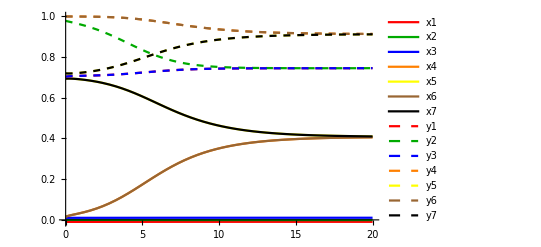

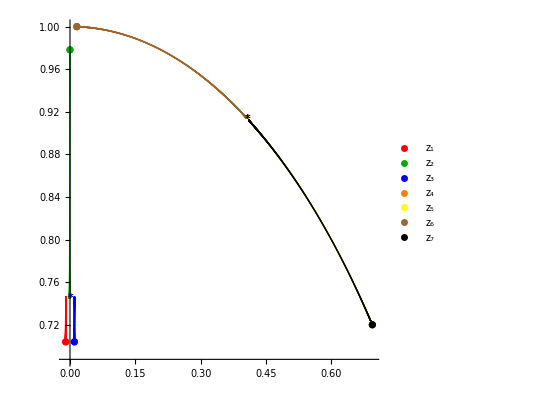

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO11_Nonzero_Chi.csv",valsBetter,"csv"];*)
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distanceBeginAndEnd=False;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α2,α3,α4}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|16.5→<|{4.67326,0.059365,0.55439}→0.0181609|>|>

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion2Crit2RescaledRvalue;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=5;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=20;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={25};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={0.00000000001,0.01};
rmaxIncrementList={0.5, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

```mathematica
allExplorations;
```

## Check the results

```mathematica
(*Put[allExplorations,"explorations_SO11_15_5"]*)
(*Put[expansion2Crit2RescaledRvalue,"expansion_SO11_15_5"]*)
```

```mathematica
Put[allExplorations,"allExplorations_Chi_Nonzero_1_06_part3"]
```

```mathematica
allExplorations;
```

```mathematica
Keys[allExplorations]
```

{8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5}

```mathematica
finalRmax=Max[Keys[allExplorations]]
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final]
finalDistance=final[finalValues];
```

20.

{4.67326,0.059365,0.55439}

```mathematica
(* Get IC ready *)
IC = expansion2Crit2RescaledRvalue/.getAlphaRule[finalValues];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC-fpSigma]
(* Solve - rmax is for the range of r *)
rmax=finalRmax;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,(distance=10^(8);Print["Blew up!"])];
```

{x1[0]==-0.00991976,y1[0]==0.70405,x2[0]==0.0000187723,y2[0]==0.97811,x3[0]==0.0100802,y3[0]==0.70405,x4[0]==0.0157733,y4[0]==0.999883,x5[0]==0.693899,y5[0]==0.720082,x6[0]==0.0157733,y6[0]==0.999883,x7[0]==0.693899,y7[0]==0.720082}

{0.0000802431,0.00305674,0.0000187723,0.0218897,0.0000802431,0.00305674,0.0157733,0.000117119,0.0132077,0.0129756,0.0157733,0.000117119,0.0132077,0.0129756}

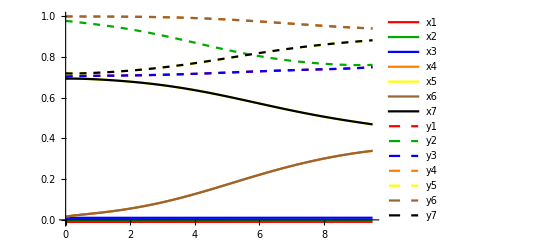

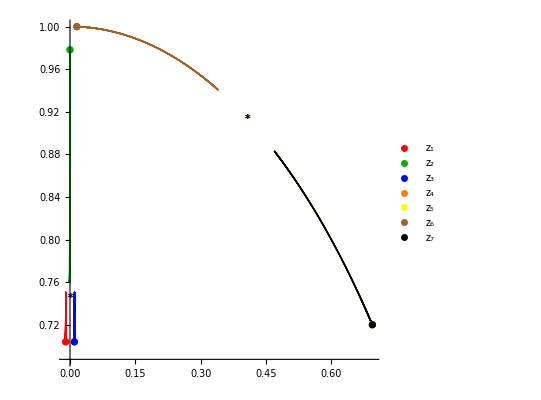

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

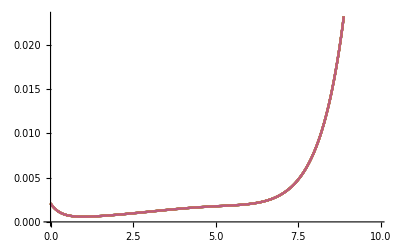

```mathematica
theSum=Evaluate[Table[x1[r]+x2[r]+x3[r]/. solution,{i, 1,Length[sigmaR]}]];
Plot[theSum,{r, 0, finalRmax}]
```

```mathematica
Evaluate[{x1[rmax],x2[rmax],x3[rmax]}/. solution]
```

{{0.150011,-0.23373,0.170011}}

## Current work: What’s the deal with alpha five?

## Get critical points and Get expansion:

```mathematica
(* Define target: *)
goalindex=1;
{chi1Value,chi2Value}={0,0};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
target=goal;
goalUV=goal;
goal//cut;
(* Define starting point: *)
index=2;
chiValue=0.01;
start=critPoints2FamilyI/.{chi->chiValue,phi->chiValue,c->1};
critPoint=start/.{chi->chiValue, phi->chiValue};
fpSigma=critPoints2Sigma[[index]]/.{chi->chiValue,phi->chiValue,c->1};
```

```mathematica
fpSigma//N//cut
```

{{-0.01,0.707107},{0.,1.},{0.01,0.707107},{0.,1.},{0.707107,0.707107},{0.,1.},{0.707107,0.707107}}

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2FamilyI;
fp=fp/.{chi->chiValue,phi->chiValue}//N
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get eigenvectors for the expansion *)
jac=jacobian2//evalatFP;
jac=jac//N//Chop;
{eigenvals, eigenvecs}=jac//Eigensystem//Chop;
(* For the results obtained at chi = phi = 0: save them *)
(*{eigenvalsAtOrigin, eigenvecsAtOrigin}={eigenvals, eigenvecs};*)
eigenvals//Sort
```

{-0.01+0.707107 ⅈ,0.+1. ⅈ,0.01+0.707107 ⅈ,0.+1. ⅈ,0.707107+0.707107 ⅈ,0.+1. ⅈ,0.707107+0.707107 ⅈ}

{-3.56155,-3.56155,-2.56155,-2.56155,-2.0004,-2.,-1.0004,-0.9996,0,0.00039984,0.561553,0.561553,1.56155,1.56155}

IGNORE THIS ___ THIS IS JUST FOR THE APPENDIX B TABLE AT THE END

```mathematica
{chi1Star,chi2Star}=-{-0.02029767536628553481551078701057402956611199935716819051429779514854435357829`49.989603308740314,-2*(-0.02029767536628553481551078701057402956611199935716819051429779514854435357829`49.989603308740314)};
```

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2[[1]];
fp=fp/.{chi1->chi1Star,chi2->chi2Star}//N
potentialValue=potentialValues2[[1]];
L=Sqrt[-3/potentialValue];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get eigenvectors for the expansion *)
jac=jacobian2//evalatFP;
jac=jac//N//Chop;
{eigenvals, eigenvecs}=jac//Eigensystem//Chop;
eigenvals//Sort;
deltas=eigenvals*(-L)//Sort
```

{-0.0202977+0.745356 ⅈ,0.0405954+0.745356 ⅈ,-0.0202977+0.745356 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ,0.408248+0.912871 ⅈ}

{-1.44949,-1.44949,0.,0.,0.327182,0.33179,0.33179,1.66821,1.66821,1.67282,2.,2.,3.44949,3.44949}

## Get the expansion

```mathematica
(* Now get the expansion DON'T DELETE!!! *)
expansion2Crit2=getExpansion[fpSigma,eigenvals,eigenvecs]//N;
expansion2Crit2Broken=expansion2Crit2/.{α5->0.01,rvalue->Log[10^-2]}; 
expansion2Crit2RescaledRvaluev2=expansion2Crit2/.{α1->-7.662078398570975,α5->0.01,rvalue->Log[10^-2]}; (* alpha 1 fix was for good chi = zero *)
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop
expansion2Crit2RescaledRvalue//cut;
```

{-0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2,0.00146266-0.000293417 α2+0.0322966 α3-0.00358945 α4,0.998559-0.0000526792 α2-0.0364401 α4,0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2,-0.00705524+0.0284515 α4,0.998127+0.000375802 α2,0.706951+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.704912+0.000170227 α2+0.0228372 α3+0.0232289 α4,0.00705524+0.0284515 α4,0.998127+0.000375802 α2,0.707233+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.705194+0.000170227 α2+0.0228372 α3+0.0232289 α4}

## WATCH OUT WE ARE CHANGING THE DISTANCE FUNCTION HERE

```mathematica
(* Function which computes distance between end of an RG flow, and a target, using hyperbolic distance! *)
getDistanceEndFlow[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
endValuesHereCont={endValuesHere[[2]],endValuesHere[[4]],endValuesHere[[6]],endValuesHere[[7]],endValuesHere[[8]],endValuesHere[[9]],endValuesHere[[10]],endValuesHere[[11]],endValuesHere[[12]],endValuesHere[[13]],endValuesHere[[14]]};
targetCont={target[[2]],target[[4]],target[[6]],target[[7]],target[[8]],target[[9]],target[[10]],target[[11]],target[[12]],target[[13]],target[[14]]};
distanceEucl=EuclideanDistance[endValuesHereCont,targetCont];
distanceChi=Abs[endValuesHere[[1]]+endValuesHere[[3]]+endValuesHere[[5]]];
distanceHere=distanceEucl+distanceChi;
Return[distanceHere];
);
```

```mathematica
(* Choose the UV target that we wish to land on here! *)
val=0;
{chi1Value,chi2Value}={val,-2val};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
```

```mathematica
start//N//cut;
goal//N//cut;
```

```mathematica
rvalueHere=Log[10^-2];
(* Don't fix an alpha yet, keep everyone, try to optimize first guess this way: *)
expansion2AllAlphas=expansion2Crit2Broken;
eps=1;
(* We want to start in the same direction as the ICGS ansatz *)
startingTarget=ICGS;
startingTarget[[1]]=goal[[1]];
startingTarget[[3]]=goal[[3]];
startingTarget[[5]]=goal[[5]];
startingTarget;
goodDirection=fpSigma+eps*(startingTarget-fpSigma)//N;
goodDirection;
```

```mathematica
(* Try to get, from our expansion, as close to the best initial start as possible *)
myDeviations=expansion2AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
(* Look for minimum of distance *)
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify//N;
sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α1,α2,α3,α4}];
(*eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0,D[distanceFunction,α5]==0}//ComplexExpand//Simplify;*)
(*sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals],Element[α5,Reals]}],{α1,α2,α3,α4,α5}];*)
solValue=sol[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α1→-7.66208,α2→4.56703,α3→0.0593658,α4→0.550491}

```mathematica
(* Now define expansion, fix alpha 1 using best ansatz from above: *)
alpha1Value=α1/.solValue;
expansion2Crit2Broken=expansion2Crit2Broken /. {α1->alpha1Value};
expansion2Crit2Broken // cut
```

{{-0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2},{0.00146266-0.000293417 α2+0.0322966 α3-0.00358945 α4,0.998559-0.0000526792 α2-0.0364401 α4},{0.01-0.0356614 α3+0.00396342 α4,0.704496-0.0000954173 α2},{-0.00705524+0.0284515 α4,0.998127+0.000375802 α2},{0.706951+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.704912+0.000170227 α2+0.0228372 α3+0.0232289 α4},{0.00705524+0.0284515 α4,0.998127+0.000375802 α2},{0.707233+0.000244727 α2+0.0228372 α3-0.0283051 α4,0.705194+0.000170227 α2+0.0228372 α3+0.0232289 α4}}

#### Step 1) Find a good initial point by hand

```mathematica
(* Get IC ready *)
ansatz={4.673264742920671,0.05936499004466509,0.5543896161564815};
ansatz={α2,α3,α4}/.solValue;
numberOfParams=3;
startIndex=2;
IC = expansion2Crit2Broken/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine
IC;
IC- fpSigma//cut
(* Solve - rmax is for the range of r *)
rmax=4;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];
```

{x1[0]==-0.00993524,y1[0]==0.70406,x2[0]==0.0000639655,y2[0]==0.978258,x3[0]==0.0100648,y3[0]==0.70406,x4[0]==0.00860709,y4[0]==0.999843,x5[0]==0.693842,y5[0]==0.719833,x6[0]==0.0227176,y6[0]==0.999843,x7[0]==0.694124,y7[0]==0.720115}

{{0.0000647591,-0.00304661},{0.0000639655,-0.0217419},{0.0000647591,-0.00304661},{0.00860709,-0.000157042},{-0.0132644,0.0127259},{0.0227176,-0.000157042},{-0.0129823,0.013008}}

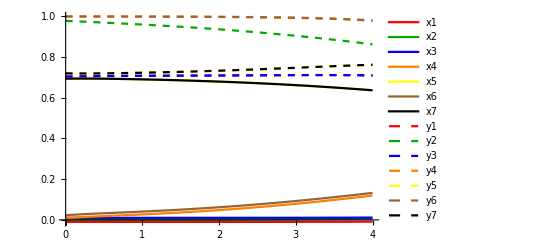

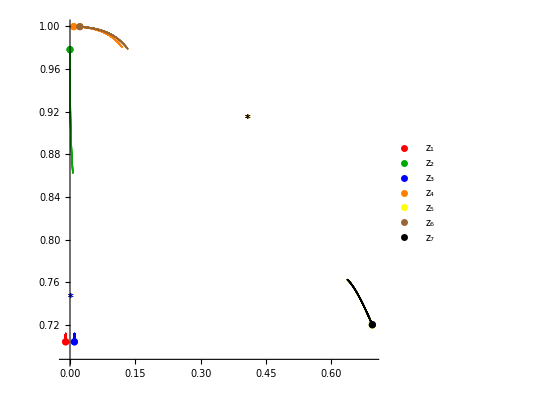

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO11_Nonzero_Chi.csv",valsBetter,"csv"];*)
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distanceBeginAndEnd=False;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α2,α3,α4}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|16.5→<|{4.67326,0.059365,0.55439}→0.0181609|>|>

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion2Crit2RescaledRvalue;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=5;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=20;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={25};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={0.00000000001,0.01};
rmaxIncrementList={0.5, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

```mathematica
allExplorations;
```

## Check the results

```mathematica
(*Put[allExplorations,"explorations_SO11_15_5"]*)
(*Put[expansion2Crit2RescaledRvalue,"expansion_SO11_15_5"]*)
```

```mathematica
Put[allExplorations,"allExplorations_Chi_Nonzero_1_06_part3"]
```

```mathematica
allExplorations;
```

```mathematica
Keys[allExplorations]
```

{8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5}

```mathematica
finalRmax=Max[Keys[allExplorations]]
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final]
finalDistance=final[finalValues];
```

20.

{4.67326,0.059365,0.55439}

```mathematica
(* Get IC ready *)
IC = expansion2Crit2RescaledRvalue/.getAlphaRule[finalValues];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC-fpSigma]
(* Solve - rmax is for the range of r *)
rmax=finalRmax;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,(distance=10^(8);Print["Blew up!"])];
```

{x1[0]==-0.00991976,y1[0]==0.70405,x2[0]==0.0000187723,y2[0]==0.97811,x3[0]==0.0100802,y3[0]==0.70405,x4[0]==0.0157733,y4[0]==0.999883,x5[0]==0.693899,y5[0]==0.720082,x6[0]==0.0157733,y6[0]==0.999883,x7[0]==0.693899,y7[0]==0.720082}

{0.0000802431,0.00305674,0.0000187723,0.0218897,0.0000802431,0.00305674,0.0157733,0.000117119,0.0132077,0.0129756,0.0157733,0.000117119,0.0132077,0.0129756}

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Current work: getting a new flow from non-zero phi

## Get critical points and Get expansion:

```mathematica
(* Define target: *)
goalindex=1;
{chi1Value,chi2Value}={0,0};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
target=goal;
goalUV=goal;
goal//cut;
(* Define starting point: *)
index=3;
chiValue=0.00;
start=critPoints2FamilyI/.{chi->chiValue,phi->chiValue,c->1};
critPoint=start/.{chi->chiValue, phi->chiValue};
fpSigma=critPoints2Sigma[[index]]/.{chi->chiValue,phi->chiValue,c->1};
```

```mathematica
fpSigma//N//cut
```

{{0.,0.707142},{0.,0.707142},{0.,1.},{0.707107,0.707107},{0.707107,0.707107},{-0.0099995,0.99995},{0.0099995,0.99995}}

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2FamilyII;
fp=fp/.{chi->chiValue,phi->chiValue}//N
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get eigenvectors for the expansion *)
jac=jacobian2//evalatFP;
jac=jac//N//Chop;
{eigenvals, eigenvecs}=jac//Eigensystem//Chop;
(* For the results obtained at chi = phi = 0: save them *)
(*{eigenvalsAtOrigin, eigenvecsAtOrigin}={eigenvals, eigenvecs};*)
eigenvals//Sort
```

{0.+0.707107 ⅈ,0.+0.707107 ⅈ,0.+1. ⅈ,0.707107+0.707107 ⅈ,0.707107+0.707107 ⅈ,0.+1. ⅈ,0.+1. ⅈ}

{-3.56155,-3.56155,-2.56155,-2.56155,-2.,-2.,-1.,-1.,0,0,0.561553,0.561553,1.56155,1.56155}

```mathematica
(* Now get the expansion DON'T DELETE!!! *)
expansion2Crit2=getExpansion[fpSigma,eigenvals,eigenvecs]//N;
expansion2Crit2RescaledRvaluev2=expansion2Crit2/.{rvalue->Log[10^-2]}; 
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop
expansion2Crit2RescaledRvalue//cut;
```

{0.0356614 α3-0.013476 α4,0.707107+0.000440105 α1+0.0000524176 α2,0.0356614 α3-0.013476 α4,0.707107+0.000440105 α1+0.0000524176 α2,0.0000209971 α1+0.000298401 α2-0.0322966 α3+0.0122045 α4,1.+0.000242978 α1+0.0000289393 α2+0.0339484 α4,0.707107-0.000186659 α1-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107+0.000156964 α1-0.000190538 α2-0.0228372 α3-0.0153753 α4,0.707107-0.000186659 α1-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107+0.000156964 α1-0.000190538 α2-0.0228372 α3-0.0153753 α4,-0.0265061 α4,1.-0.0000268926 α1-0.000382185 α2,-0.0265061 α4,1.-0.0000268926 α1-0.000382185 α2}

## Find a good shooting guess from experience (if wanted)

```mathematica
(* Choose the UV target that we wish to land on here! *)
val=0;
{chi1Value,chi2Value}={val,-2val};
goal=critPoints2Sigma[[goalindex]]/.{chi1->chi1Value,chi2->chi2Value,c->1};
```

```mathematica
start//N//cut
goal//N//cut
```

{{0.+0.707107 ⅈ,0.+1. ⅈ},{0.+0.707107 ⅈ,0.+1. ⅈ},{0.707107+0.707107 ⅈ,0.+1. ⅈ}}

{{0.,0.745356},{0.,0.745356},{0.,0.745356},{0.408248,0.912871},{0.408248,0.912871},{0.408248,0.912871},{0.408248,0.912871}}

```mathematica
rvalueHere=Log[10^-2];
(* Don't fix an alpha yet, keep everyone, try to optimize first guess this way: *)
expansion2AllAlphas=expansion2Crit2RescaledRvalue
eps=0.01;
(* We want to start in the same direction as the ICGS ansatz *)
startingTarget=ICGS;
startingTarget[[1]]=goal[[1]];
startingTarget[[3]]=goal[[3]];
startingTarget[[5]]=goal[[5]];
startingTarget;
goodDirection=fpSigma+eps*(startingTarget-fpSigma)//N;
goodDirection;
```

{0.0356614 α3-0.013476 α4,0.707107+0.000440105 α1+0.0000524176 α2,0.0356614 α3-0.013476 α4,0.707107+0.000440105 α1+0.0000524176 α2,0.0000209971 α1+0.000298401 α2-0.0322966 α3+0.0122045 α4,1.+0.000242978 α1+0.0000289393 α2+0.0339484 α4,0.707107-0.000186659 α1-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107+0.000156964 α1-0.000190538 α2-0.0228372 α3-0.0153753 α4,0.707107-0.000186659 α1-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107+0.000156964 α1-0.000190538 α2-0.0228372 α3-0.0153753 α4,-0.0265061 α4,1.-0.0000268926 α1-0.000382185 α2,-0.0265061 α4,1.-0.0000268926 α1-0.000382185 α2}

```mathematica
(* Try to get, from our expansion, as close to the best initial start as possible *)
myDeviations=expansion2AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
(* Look for minimum of distance *)
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify//N;
sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α1,α2,α3,α4}];
(*eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0,D[distanceFunction,α5]==0}//ComplexExpand//Simplify;*)
(*sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals],Element[α5,Reals]}],{α1,α2,α3,α4,α5}];*)
solValue=sol[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α1→1.97255,α2→3.11081,α3→-0.0292541,α4→-0.104839}

```mathematica
(* Now define expansion, fix alpha 1 using best ansatz from above: *)
alpha1Value=α1/.solValue;
expansion2Crit2RescaledRvaluev2=expansion2Crit2 /. {α1->alpha1Value,α5->0,rvalue ->rvalueHere};
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop ;
expansion2Crit2RescaledRvalue // cut
```

{{0.0356614 α3-0.013476 α4,0.707975+0.0000524176 α2},{0.0356614 α3-0.013476 α4,0.707975+0.0000524176 α2},{0.0000414179+0.000298401 α2-0.0322966 α3+0.0122045 α4,1.00048+0.0000289393 α2+0.0339484 α4},{0.706739-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707416-0.000190538 α2-0.0228372 α3-0.0153753 α4},{0.706739-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707416-0.000190538 α2-0.0228372 α3-0.0153753 α4},{-0.0265061 α4,0.999947-0.000382185 α2},{-0.0265061 α4,0.999947-0.000382185 α2}}

## FINDING RG FLOWS - CURRENT WORK

## WATCH OUT WE ARE CHANGING THE DISTANCE FUNCTION HERE

```mathematica
(* Function which computes distance between end of an RG flow, and a target, using hyperbolic distance! *)
getDistanceEndFlow[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
endValuesHereCont={endValuesHere[[2]],endValuesHere[[4]],endValuesHere[[6]],endValuesHere[[7]],endValuesHere[[8]],endValuesHere[[9]],endValuesHere[[10]],endValuesHere[[11]],endValuesHere[[12]],endValuesHere[[13]],endValuesHere[[14]]};
targetCont={target[[2]],target[[4]],target[[6]],target[[7]],target[[8]],target[[9]],target[[10]],target[[11]],target[[12]],target[[13]],target[[14]]};
distanceEucl=EuclideanDistance[endValuesHereCont,targetCont];
distanceChi=Abs[endValuesHere[[1]]+endValuesHere[[3]]+endValuesHere[[5]]];
distanceHere=distanceEucl+distanceChi;
Return[distanceHere];
);
```

#### Step 1) Find a good initial point by hand

```mathematica
(* Now define expansion, fix alpha 1 using best ansatz from above: *)
alpha1Value=0.001;
expansion2Crit2RescaledRvaluev2=expansion2Crit2 /. {α1->alpha1Value,α5->0,rvalue ->rvalueHere};
expansion2Crit2RescaledRvalue=expansion2Crit2RescaledRvaluev2//Chop ;
expansion2Crit2RescaledRvalue // cut
```

{{0.0356614 α3-0.013476 α4,0.707107+0.0000524176 α2},{0.0356614 α3-0.013476 α4,0.707107+0.0000524176 α2},{2.09971×10^-8+0.000298401 α2-0.0322966 α3+0.0122045 α4,1.+0.0000289393 α2+0.0339484 α4},{0.707107-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107-0.000190538 α2-0.0228372 α3-0.0153753 α4},{0.707107-0.000231465 α2-0.0228372 α3+0.032635 α4,0.707107-0.000190538 α2-0.0228372 α3-0.0153753 α4},{-0.0265061 α4,1.-0.000382185 α2},{-0.0265061 α4,1.-0.000382185 α2}}

```mathematica
(* Get IC ready *)
ansatz={ α2, α3, α4}/.solValue;
ansatz={0,0,0};
numberOfParams=3;
startIndex=2;
IC = expansion2Crit2RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine
IC;
IC- fpSigma//cut
ICGS;
(* Solve - rmax is for the range of r *)
rmax=2.5;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];
```

{x1[0]==0.,y1[0]==0.707107,x2[0]==0.,y2[0]==0.707107,x3[0]==2.09971×10^-8,y3[0]==1.,x4[0]==0.707107,y4[0]==0.707107,x5[0]==0.707107,y5[0]==0.707107,x6[0]==0.,y6[0]==1.,x7[0]==0.,y7[0]==1.}

{{0.,4.40105×10^-7},{0.,4.40105×10^-7},{2.09971×10^-8,2.42978×10^-7},{-1.86659×10^-7,1.56964×10^-7},{-1.86659×10^-7,1.56964×10^-7},{0.,-2.68926×10^-8},{0.,-2.68926×10^-8}}

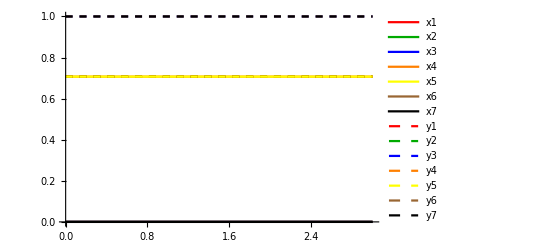

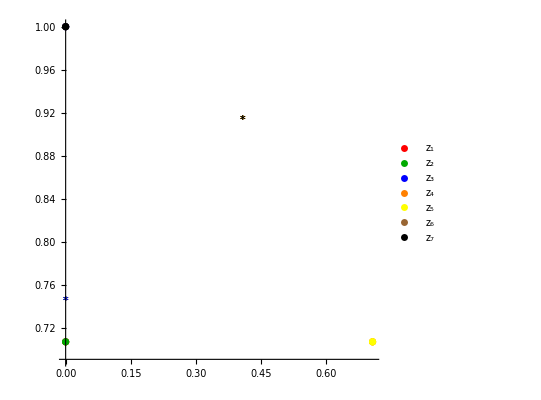

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO11_Nonzero_Chi.csv",valsBetter,"csv"];*)
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distanceBeginAndEnd=False;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α2,α3,α4}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|3→<|{0,0,0}→0.824367622235976564968184896365800265673099444985|>|>

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion2Crit2RescaledRvalue;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=5;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=10;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={25};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={1,0.01};
rmaxIncrementList={0.1, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

=== === rmax: 3 === ===

Tuning parameter: 1.

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 1. Parameter values: {1,0,0}.

Distance: 0.8520598845.

Parameter values: {-1,0,0}.

Distance: 0.8831308324.

Direction not found. Step back: s: 0.1. Count: 1/5

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 1. Parameter values: {0.1,0.,0.}.

Distance: 0.8267805618.

Parameter values: {-0.1,0.,0.}.

Distance: 0.8297367989.

Direction not found. Step back: s: 0.01. Count: 2/5

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 1. Parameter values: {0.01,0.,0.}.

Distance: 0.8246051800.

Parameter values: {-0.01,0.,0.}.

Distance: 0.8248950814.

Direction not found. Step back: s: 0.001. Count: 3/5

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 1. Parameter values: {0.001,0.,0.}.

Distance: 0.8243913404.

Parameter values: {-0.001,0.,0.}.

Distance: 0.8244154495.

Direction not found. Step back: s: 0.0001. Count: 4/5

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 1. Parameter values: {0.0001,0.,0.}.

Distance: 0.8243699937.

Parameter values: {-0.0001,0.,0.}.

Distance: 0.8243675313.

Direction not found. Step back: s: 0.00001. Count: 5/5

Maximum tuning achieved for this parameter!

Tuning parameter: 2.

Current best: {0,0,0}. Distance: 0.824367622235976564968184896365800265673099444985.

Finding correct direction for nr 2. Parameter values: {0,1,0}.

$Aborted

```mathematica
allExplorations
```

<|2→<|{3.11081,-0.0292541,-0.104839}→0.81631280480160617437141695857869662673871890841,{2.11081,-0.0292541,-0.104839}→0.81068286627607172336821060264735257271123340541,{1.11081,-0.0292541,-0.104839}→0.80532440840878953861572833382488053560209803312,{0.110808,-0.0292541,-0.104839}→0.80024501706448355043084272011401899955518349612,{0.010808,-0.0292541,-0.104839}→0.79975274978091109326995288764548977921001920455,{-0.089192,-0.0292541,-0.104839}→0.799263367878519796336319269719081114885311559402,{-0.189192,-0.0292541,-0.104839}→0.798776880705839910627245457063044715413543941134,{-0.289192,-0.0292541,-0.104839}→0.798293297724023917573027257721708418667922505767,{-0.299192,-0.0292541,-0.104839}→0.798245099523970683728338656788621125138506244311,{-0.309192,-0.0292541,-0.104839}→0.798196930471113957469521069201059494792939389382,{-0.319192,-0.0292541,-0.104839}→0.798148790575101539819938251229608655060994551003,{-0.329192,-0.0292541,-0.104839}→0.798100679845593414502174485864203701970792586032,{-0.339192,-0.0292541,-0.104839}→0.798052598292260908862832129012863274490129958449,{-0.339192,-0.0292541,-1.10484}→0.699740367848271979548440122903996227618178603793,{-0.339192,-0.0292541,-2.10484}→0.678334263076716822051401592598933666948945145869,{-0.339192,-0.0292541,-2.00484}→0.67799044490845180452541224319229461103497045765|>,2.1→<|{-0.339192,-0.0292541,-2.00484}→0.697941,{-1.33919,-0.0292541,-2.00484}→0.689599,{-2.33919,-0.0292541,-2.00484}→0.681413,{-3.33919,-0.0292541,-2.00484}→0.673381,{-4.33919,-0.0292541,-2.00484}→0.665503,{-5.33919,-0.0292541,-2.00484}→0.65778,{-6.33919,-0.0292541,-2.00484}→0.65021,{-7.33919,-0.0292541,-2.00484}→0.642795,{-8.33919,-0.0292541,-2.00484}→0.635536,{-9.33919,-0.0292541,-2.00484}→0.628435,{-10.3392,-0.0292541,-2.00484}→0.621493,{-11.3392,-0.0292541,-2.00484}→0.614713,{-12.3392,-0.0292541,-2.00484}→0.608099,{-13.3392,-0.0292541,-2.00484}→0.601653,{-14.3392,-0.0292541,-2.00484}→0.59538,{-15.3392,-0.0292541,-2.00484}→0.589284,{-16.3392,-0.0292541,-2.00484}→0.583371,{-17.3392,-0.0292541,-2.00484}→0.577644,{-18.3392,-0.0292541,-2.00484}→0.572112,{-19.3392,-0.0292541,-2.00484}→0.566779,{-20.3392,-0.0292541,-2.00484}→0.561655,{-21.3392,-0.0292541,-2.00484}→0.556745,{-22.3392,-0.0292541,-2.00484}→0.555482,{-22.2392,-0.0292541,-2.00484}→0.554738,{-22.1392,-0.0292541,-2.00484}→0.553997,{-22.0392,-0.0292541,-2.00484}→0.55344,{-22.0492,-0.0292541,-2.00484}→0.553394|>|>

# ======================================

# Compilation of RG flows of SO(1, 1) model:

## #1 - The flow from Guarino & Sterckx, exactly copy-pasting their expansion and values:

```mathematica
(* Here, the IC are taken from Guarino & Sterckx: see their eq 3.10, but we put L = -1 (from potential value)  *)
Clear[lambda1,lambda2,bigLambda1,bigLambda2]
re={(-1+Sqrt[17])/(4*Sqrt[2])*lambda1*Exp[-0.5*(3-Sqrt[17])*rvalue],-(bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue] + lambda1*Exp[-0.5*(3-Sqrt[17])rvalue]),(-1+Sqrt[17])/(4*Sqrt[2])*lambda1*Exp[-0.5*(3-Sqrt[17])*rvalue],(-1+Sqrt[17])/(4)*lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/(2Sqrt[2])(2+(bigLambda1+bigLambda2)Exp[-0.5*(1-Sqrt[17])rvalue]-(lambda1+lambda2)Exp[-0.5*(3-Sqrt[17])rvalue]),(-1+Sqrt[17])/(4)*lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/(2Sqrt[2])(2+(bigLambda1+bigLambda2)Exp[-0.5*(1-Sqrt[17])rvalue]-(lambda1+lambda2)Exp[-0.5*(3-Sqrt[17])rvalue])};
im={1/Sqrt[2]*(1-(1+Sqrt[17])/(4)*bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]),1-bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]-lambda2*Exp[-0.5*(3-Sqrt[17])rvalue],1/Sqrt[2]*(1-(1+Sqrt[17])/(4)*bigLambda1*Exp[-0.5*(1-Sqrt[17])rvalue]),1+(1+Sqrt[17])/(4)*bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue],1/(2Sqrt[2])*(2+(bigLambda2-bigLambda1)Exp[-0.5*(1-Sqrt[17])rvalue]+(lambda2-lambda1)Exp[-0.5*(3-Sqrt[17])rvalue]),1+(1+Sqrt[17])/(4)*bigLambda2*Exp[-0.5*(1-Sqrt[17])rvalue],1/(2Sqrt[2])*(2+(bigLambda2-bigLambda1)Exp[-0.5*(1-Sqrt[17])rvalue]+(lambda2-lambda1)Exp[-0.5*(3-Sqrt[17])rvalue])};
guarinoSterckxLambdas={re,im}//Transpose//Flatten;
guarinoSterckx={re,im}/.{rvalue->Log[10^-2],lambda1->α2,lambda2->α3,bigLambda2->α4,bigLambda1->-1}//Transpose//Flatten;
(* Get IC of best flow *)
bestLambda1=0.0042958950;
bestLambda2=0.3421361222;
bestBigLambda1=-1;
bestBigLambda2=-0.1566939789;
(* Get actual values from it *)
ICGS=guarinoSterckxLambdas/.{rvalue->Log[10^-2],lambda1->bestLambda1,lambda2->bestLambda2,bigLambda1->bestBigLambda1,bigLambda2->bestBigLambda2};
(* Gather in a list *)
ICGSlist=Table[sigmaZero[[i]]==ICGS[[i]],{i,1,Length[sigmaZero]}]//refine;
ICGSlist
```

{x1[0]==0.000178632,y1[0]==0.707789,x2[0]==-0.000205537,y2[0]==0.974984,x3[0]==0.000178632,y3[0]==0.707789,x4[0]==0.0201196,y4[0]==0.999849,x5[0]==0.697574,y5[0]==0.716328,x6[0]==0.0201196,y6[0]==0.999849,x7[0]==0.697574,y7[0]==0.716328}

```mathematica
(* Get IC ready *)
ansatz={"0.00429589502","0.3421361222342497","-0.15669397894"};
numberOfParams=3;
startIndex=2;
IC = guarinoSterckx/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
(* Solve - rmax is for the range of r *)
rmax=19;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],40,(distance=10^(8);Print["no"])];
```

{x1[0]==0.000178632,y1[0]==0.707789,x2[0]==-0.000205537,y2[0]==0.974984,x3[0]==0.000178632,y3[0]==0.707789,x4[0]==0.0201196,y4[0]==0.999849,x5[0]==0.697574,y5[0]==0.716328,x6[0]==0.0201196,y6[0]==0.999849,x7[0]==0.697574,y7[0]==0.716328}

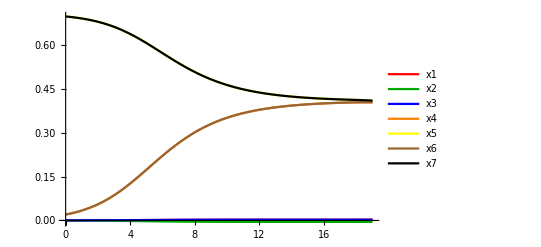

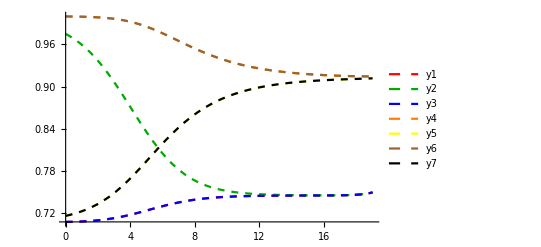

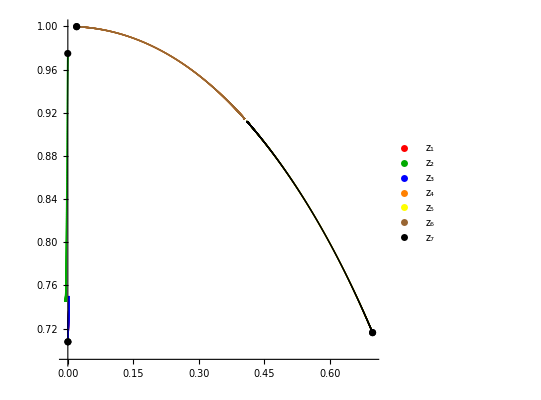

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
plotIC=ListPlot[ICGS//cut,PlotStyle->colorsRF];
(* Show desired plots *)
Show[plotReScalars]
Show[plotImScalars]
Show[plotComplexScalars,plotIC]
```

```mathematica
x1[15]/.solution
```

{0.002503122215251755549289991692616430609669744058705}

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_1_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_1_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO11_GS_1.csv",valsBetter,"csv"];*)
```

## #2 - G&S but different coefficients

```mathematica
(* Define the goal *)
{chi1Value,chi2Value}={0.02,-0.04};
goal=critPoints2Sigma[[1]]/.{chi1->chi1Value,chi2->chi2Value}//N
```

{-0.02,0.745356,0.04,0.745356,-0.02,0.745356,0.408248,0.912871,0.408248,0.912871,0.408248,0.912871,0.408248,0.912871}

```mathematica
(*Put[allExplorations,"guarinoExplorationsv2part1"]*)
```

```mathematica
(* Get IC ready *)
ansatz={-0.027605720061501006,0.3397537432343989,-0.30789650806929986};
numberOfParams=3;
startIndex=2;
IC = guarinoSterckx/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
(* Solve - rmax is for the range of r *)
rmax=20;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],40,(distance=10^(8);Print["no"])];
```

{x1[0]==-0.0011479,y1[0]==0.707789,x2[0]==0.00231109,y2[0]==0.975164,x3[0]==-0.0011479,y3[0]==0.707789,x4[0]==0.0199795,y4[0]==0.999703,x5[0]==0.698446,y5[0]==0.717073,x6[0]==0.0199795,y6[0]==0.999703,x7[0]==0.698446,y7[0]==0.717073}

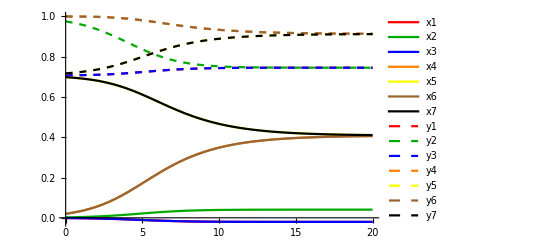

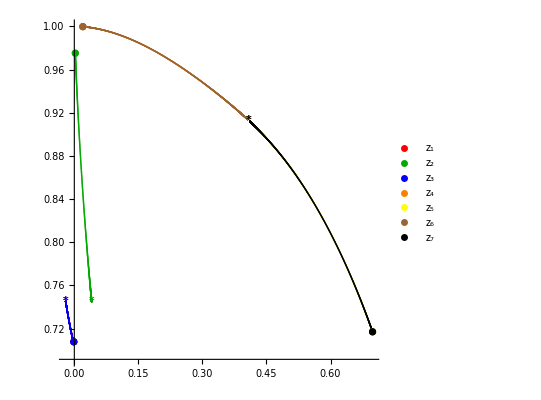

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
Evaluate[{x1[rmax],x2[rmax],x3[rmax]}/. solution]
```

{{-0.02029767536628553481551078701057402956611199935717,0.04054527641736048629774409993736106522171463920516,-0.02029767536628553481551078701057402956611199935717}}

## Get flow data

```mathematica
(* Fixed points data *)
(*Export["flowData_SO11_GS_2_start.csv",N[start],"csv"];*)
(*Export["flowData_SO11_GS_2_goal.csv",N[goal],"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO11_GS_2.csv",valsBetter,"csv"];*)
```

## Extra: getting the masses and the scaling dimensions

```mathematica
potential2RF=potential2//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential2RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### #1 chi = 0

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPoints2[[index]]/.{g->1,c->1,chi->0};
potentialValue=potentialValues2[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.,-2.,-2.,-2.,-1.12311,-1.12311,0,0,2.,2.,2.,2.,7.12311,7.12311}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.,2.},{1.,2.},{1.,2.},{1.,2.},{0.438447,2.56155},{0.438447,2.56155},{0,3},{0,3},{-0.561553,3.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-1.56155,4.56155},{-1.56155,4.56155}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{2.,2.,2.,2.,2.56155,2.56155,3,3,3.56155,3.56155,3.56155,3.56155,4.56155,4.56155}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.,1.,1.,1.,0.438447,0.438447,0,0,-0.561553,-0.561553,-0.561553,-0.561553,-1.56155,-1.56155}

#### #2 chi = 0.01

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPoints2[[index]]/.{g->1,c->1,chi->0.01};
potentialValue=potentialValues2[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.0004,-2.,-1.9996,-1.9996,-1.12311,-1.12311,0,0.00119968,2.,2.,2.,2.,7.12311,7.12311}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.0004,1.9996},{1.,2.},{0.9996,2.0004},{0.9996,2.0004},{0.438447,2.56155},{0.438447,2.56155},{0,3},{-0.00039984,3.0004},{-0.561553,3.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-1.56155,4.56155},{-1.56155,4.56155}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.9996,2.,2.0004,2.0004,2.56155,2.56155,3,3.0004,3.56155,3.56155,3.56155,3.56155,4.56155,4.56155}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.0004,1.,0.9996,0.9996,0.438447,0.438447,0,-0.00039984,-0.561553,-0.561553,-0.561553,-0.561553,-1.56155,-1.56155}

```mathematica
(* First part *)
Table[allMasses[[i]],{i,1,6}]
```

{-2.0004,-2.,-1.9996,-1.9996,-1.12311,-1.12311}

```mathematica
Table[deltaPlus[[i]],{i,1,6}]
```

{1.9996,2.,2.0004,2.0004,2.56155,2.56155}

```mathematica
Table[deltaMinus[[i]],{i,1,6}]
```

{1.0004,1.,0.9996,0.9996,0.438447,0.438447}

```mathematica
(* Second part *)
Table[allMasses[[i]],{i,7,14}]
```

{0,0.00119968,2.,2.,2.,2.,7.12311,7.12311}

```mathematica
Table[deltaPlus[[i]],{i,7,14}]
```

{3,3.0004,3.56155,3.56155,3.56155,3.56155,4.56155,4.56155}

```mathematica
Table[deltaMinus[[i]],{i,7,14}]
```

{0,-0.00039984,-0.561553,-0.561553,-0.561553,-0.561553,-1.56155,-1.56155}

#### #3 chi123 = 0

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPoints2[[index]]/.{g->1,c->1,chi1->0,chi2->0};
potentialValue=potentialValues2[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22222,-2.22222,-2.22222,-2.,-2.,-0.888889,-0.888889,-0.888889,0,0,1.55051,1.55051,6.44949,6.44949}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33333,1.66667},{1.33333,1.66667},{1.33333,1.66667},{1.,2.},{1.,2.},{0.333333,2.66667},{0.333333,2.66667},{0.333333,2.66667},{0,3},{0,3},{-0.44949,3.44949},{-0.44949,3.44949},{-1.44949,4.44949},{-1.44949,4.44949}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66667,1.66667,1.66667,2.,2.,2.66667,2.66667,2.66667,3,3,3.44949,3.44949,4.44949,4.44949}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33333,1.33333,1.33333,1.,1.,0.333333,0.333333,0.333333,0,0,-0.44949,-0.44949,-1.44949,-1.44949}

```mathematica
(* First part *)
Table[allMasses[[i]],{i,1,6}]
```

{-2.0004,-2.,-1.9996,-1.9996,-1.12311,-1.12311}

```mathematica
Table[deltaPlus[[i]],{i,1,6}]
```

{1.9996,2.,2.0004,2.0004,2.56155,2.56155}

```mathematica
Table[deltaMinus[[i]],{i,1,6}]
```

{1.0004,1.,0.9996,0.9996,0.438447,0.438447}

```mathematica
(* Second part *)
Table[allMasses[[i]],{i,7,14}]
```

{0,0.00119968,2.,2.,2.,2.,7.12311,7.12311}

```mathematica
Table[deltaPlus[[i]],{i,7,14}]
```

{3,3.0004,3.56155,3.56155,3.56155,3.56155,4.56155,4.56155}

```mathematica
Table[deltaMinus[[i]],{i,7,14}]
```

{0,-0.00039984,-0.561553,-0.561553,-0.561553,-0.561553,-1.56155,-1.56155}

#### #3 chi123 at other value

```mathematica
{chi1Star,chi2Star}=-{-0.02029767536628553481551078701057402956611199935716819051429779514854435357829`49.989603308740314,-2*(-0.02029767536628553481551078701057402956611199935716819051429779514854435357829`49.989603308740314)};
```

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPoints2[[index]]/.{g->1,c->1,chi1->chi1Star,chi2->chi2Star};
potentialValue=potentialValues2[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22171,-2.22171,-2.22013,-2.,-2.,-0.885286,-0.885286,-0.874497,0,0,1.55051,1.55051,6.44949,6.44949}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33179,1.66821},{1.33179,1.66821},{1.32718,1.67282},{1.,2.},{1.,2.},{0.33179,2.66821},{0.33179,2.66821},{0.327182,2.67282},{0,3},{0,3},{-0.44949,3.44949},{-0.44949,3.44949},{-1.44949,4.44949},{-1.44949,4.44949}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66821,1.66821,1.67282,2.,2.,2.66821,2.66821,2.67282,3,3,3.44949,3.44949,4.44949,4.44949}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33179,1.33179,1.32718,1.,1.,0.33179,0.33179,0.327182,0,0,-0.44949,-0.44949,-1.44949,-1.44949}

```mathematica
(* First part *)
Table[allMasses[[i]],{i,1,7}]
```

{-2.22171,-2.22171,-2.22013,-2.,-2.,-0.885286,-0.885286}

```mathematica
Table[deltaPlus[[i]],{i,1,7}]
```

{1.66821,1.66821,1.67282,2.,2.,2.66821,2.66821}

```mathematica
Table[deltaMinus[[i]],{i,1,7}]
```

{1.33179,1.33179,1.32718,1.,1.,0.33179,0.33179}

```mathematica
(* Second part *)
Table[allMasses[[i]],{i,8,14}]
```

{-0.874497,0,0,1.55051,1.55051,6.44949,6.44949}

```mathematica
Table[deltaPlus[[i]],{i,8,14}]
```

{2.67282,3,3,3.44949,3.44949,4.44949,4.44949}

```mathematica
Table[deltaMinus[[i]],{i,8,14}]
```

{0.327182,0,0,-0.44949,-0.44949,-1.44949,-1.44949}

## MODEL 3) [SO(6) x SO(2)] x R12

See arXiv:2111.11461v1 for critical points and Table 3 for the a’s and b’s values. We focus on the supersymmetric solutions, and there are two in this case. The first has SO(3) symmetry, while the second has U(1) symmetry.

### 3.1) Critical points & functions

```mathematica
superpot3=superpot/.{a->0,b->0,atilde->1,btilde->1};
potential3=potential/.{a->0,b->0,atilde->1,btilde->1};
(* SUSY critical points: eqs 3.16 and 3.19 in arXiv:2111.11461v1 *)
critPoints3part1={(2+I*Sqrt[5])/(3*Sqrt[3]),(2+I*Sqrt[5])/(3*Sqrt[3]),(2+I*Sqrt[5])/(3*Sqrt[3]), (-1+I*Sqrt[5])/(108^(1/4)),(-1+I*Sqrt[5])/(108^(1/4)),(-1+I*Sqrt[5])/(108^(1/4)),(5+I*Sqrt[5])/(108^(1/4))};
Clear[κ];
critPoints3part2=Conjugate[{κ/Sqrt[6]*Exp[-I*Pi/3], Sqrt[3+κ^2]/(4*Sqrt[2])-I*Sqrt[-3+3 κ^2]/(4*Sqrt[2]),Sqrt[3+κ^2]/(4*Sqrt[2])-I*Sqrt[-3+3 κ^2]/(4*Sqrt[2]), (κ-2)/(2Sqrt[3](2 κ^2-5)^(1/4)) - I*((7*κ^2/2)-8)^(1/4)/κ, Sqrt[κ]*6^(-1/4)Exp[-2I*Pi/3],Sqrt[κ]*6^(-1/4)Exp[-2I*Pi/3], (Sqrt[κ^2+2](2*κ^2-5)^(1/4))/(Sqrt[6]*(2-κ)) - I* ((7*κ^2/2)-8)^(1/4)/κ}];
κ=Sqrt[Sqrt[13] - 1];
(* Combine into one list *)
critPoints3={critPoints3part1,critPoints3part2};
(* Now save the critical points in the form x1, y1,... *)
critPoints3Sigma={0,0};
Table[critPoints3Sigma[[i]]=Flatten[Transpose[{Re[critPoints3[[i]]],Im[critPoints3[[i]]]}]],{i,1,Length[critPoints3]}]//refine;
(* To plot the critical points, we have to pair them like {{x1, y1}, {x2, y2},...} *)
critPoints3SigmaCut=Table[critPoints3Sigma[[i]]//cut,{i,1,Length[critPoints3Sigma]}]//refine;
potentialValues3={-243/25 √(3/5) g^2,-16/27 √(70+26 √13) g^2};
potval3Num=potentialValues3/.{g->1}//N;
lengthScales3=Sqrt[-3/potentialValues3];
```

```mathematica
potential3RF=potential3//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential3RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### First solution

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPoints3[[index]];
potentialValue=potentialValues3[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
```

#### BPS equations and Jacobian matrix

```mathematica
(* For this, we will need the BPS equations. Taken from arXiv:1909.10969v2. Here: in complex co's. sign = -1 *)
(* "part 1": since we will rework this *)
sign=-1;
factor=1;
zprime3Part1=Table[sign*factor*Exp[kahlerpot/2]*(superpot3/Abs[superpot3])*Sum[Inverse[kahlerMetric][[a]][[b]]*nablaBar[conjugate[superpot3]][[b]],{b,1,Length[z]}],{a,1,Length[z]}]//complexToRealScalars//refine//ExpToTrig;
(* Get the xprime and yprime equations from earlier: *)
xprime3=Get["xprime3"];
yprime3=Get["yprime3"];
sigmaprime3={xprime3,yprime3}//Transpose//Flatten;
```

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
(* jacobian3 = Get["jacobian3"];  *)
```

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPoints3[[index]];
potentialValue=potentialValues3[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
```

```mathematica
(* Get Jacobian matrices *)
{jacobian3Crit1Num,jacobian3Crit2Num}={Get["jacobian3Crit1Num"],Get["jacobian3Crit2Num"]};
jacobians3={jacobian3Crit1Num,jacobian3Crit2Num};
```

## === Holographic RG flows ===

```mathematica
(* Get the flow equations for the REAL scalars. Rescale such that g no longer appears *)
xprime3R=xprime3//putRDependence/.{g->1};
yprime3R=yprime3//putRDependence/.{g->1};
sigmaprime3R=Transpose[{xprime3R,yprime3R}]//Flatten;
(* Get the flow equations for the real scalars to be solved *)
flowEqs3=Table[D[sigmaR[[i]],r]-sigmaprime3R[[i]]==0,{i,1,Length[sigmaR]}]/.{g->1};
```

```mathematica
(* Start from second point, go towards first. *)
index=2;
goalindex=1;
start=critPoints3Sigma[[2]];
goal=critPoints3Sigma[[1]];
target=goal; (* using these names interchangeably... *)
jac=jacobians3[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
eigenvals
goal=critPoints3Sigma[[1]];
potentialValue=potentialValues3[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//Sort
```

{-7.84988,-7.20357,-6.28691,-6.14956,4.67016,4.02385,-3.82618,3.10719,2.96984,-2.07812,-2.02757,-1.15215,-1.10161,0.64646}

{-2.93747,-2.53094,-1.95438,-1.86799,-0.406614,0.692894,0.724684,1.27532,1.30711,2.40661,3.86799,3.95438,4.53094,4.93747}

## ===

### RG FLOW

```mathematica
(* Start from second point, go towards first. *)
start=critPoints3Sigma[[2]];
goal=critPoints3Sigma[[1]];
target=goal; (* using these names interchangeably... *)
jac=jacobians3[[index]]/.{g->1};
critPoint=start;
{eigenvals, eigenvecs}=Eigensystem[jac];
goal=critPoints3Sigma[[1]];
potentialValue=potentialValues3[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigma=critPoints3Sigma[[2]];
```

{-2.93747,-2.53094,-1.95438,-1.86799,-0.406614,0.692894,0.724684,1.27532,1.30711,2.40661,3.86799,3.95438,4.53094,4.93747}

```mathematica
expansion3=getExpansion[fpSigma,eigenvals,eigenvecs]//N;
(* Another expansion: *)
rvalueHere=Log[10^-1];
check=expansion3/.{rvalue->rvalueHere};
test=check//cut;
expansion3v2=expansion3/.{α1->0.001,α3->0,rvalue->rvalueHere};
expansion3Rescaled=expansion3v2/.{α5->α4,α4->α3};
test=expansion3Rescaled//cut;
```

```mathematica
expansion3Rescaled
```

{0.329491+0.0000503401 α2-0.0000622929 α3+0.0566373 α4,0.570696+0.0000154386 α2+0.000369598 α3-0.133516 α4,0.418537-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.38797+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4,0.418537-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.38797+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4,-0.164316+0.0000322862 α2+0.0000399532 α3-0.086448 α4,0.637235+0.0000414862 α2+0.00006168 α3+0.046639 α4,-0.405889-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.70302-0.0000197469 α2+0.0000922867 α3-0.0020048 α4,-0.405889-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.70302-0.0000197469 α2+0.0000922867 α3-0.0020048 α4,1.5392-2.18654×10^-6 α2-0.000246676 α3+0.0122587 α4,0.637235+1.26568×10^-6 α2+0.000279993 α3+0.0433162 α4}

```mathematica
test[[2]]
test[[3]]
```

{0.418537-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.38797+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4}

{0.418537-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.38797+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4}

```mathematica
test[[5]]
test[[6]]
```

{-0.405889-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.70302-0.0000197469 α2+0.0000922867 α3-0.0020048 α4}

{-0.405889-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.70302-0.0000197469 α2+0.0000922867 α3-0.0020048 α4}

## Find a good shooting guess from experience

```mathematica
expansion3AllAlphas=expansion3Rescaled;
eps=0.1;
startingTarget=target;
goodDirection=fpSigma+eps*(startingTarget-fpSigma)//N;
(*secondEps=0.5;*)
(*goodDirection[[13]]=fpSigma[[13]]+secondEps*(startingTarget[[13]]-fpSigma[[13]])//N;*)
(*goodDirection[[14]]=fpSigma[[14]]+secondEps*(startingTarget[[14]]-fpSigma[[14]])//N;*)
goodDirection;
```

```mathematica
myDeviations=expansion3AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
eqs={D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify;
sol=Solve[Join[eqs,{Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α2,α3,α4}];
solValue=sol[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α2→-51.5555,α3→-1.43864,α4→0.118075}

```mathematica
pointFound=myDeviations/.solValue
Abs[pointFound-fpSigma]
```

{0.333673,0.553603,0.41337,0.393555,0.41337,0.393555,-0.176245,0.640514,-0.399355,0.703669,-0.399355,0.703669,1.54111,0.641881}

{0.00418178,0.0170926,0.00516774,0.00558548,0.00516774,0.00558548,0.0119294,0.00327935,0.00653372,0.000648581,0.00653372,0.000648581,0.00191506,0.00464652}

```mathematica
(* Define expansion: *)
alpha1Value=α1/.solValue;
expansion3RescaledRvaluev2=expansion3 /. {α1->alpha1Value,α4->0,rvalue ->rvalueHere};
expansion3RescaledRvalue=expansion3RescaledRvaluev2 /. {α5 -> α4};
expansion3RescaledRvalue // cut
```

{{0.329491-2.26499×10^-7 α1+0.0000503401 α2-2.93432×10^-19 α3+0.0566373 α4,0.570696+1.04048×10^-6 α1+0.0000154386 α2-2.13956×10^-18 α3-0.133516 α4},{0.418537+1.78893×10^-6 α1-0.000034525 α2-0.000454727 α3-0.0586016 α4,0.38797+1.05128×10^-6 α1+1.02752×10^-7 α2-0.0000212397 α3+0.055228 α4},{0.418537+1.78893×10^-6 α1-0.000034525 α2+0.000454727 α3-0.0586016 α4,0.38797+1.05128×10^-6 α1+1.02752×10^-7 α2+0.0000212397 α3+0.055228 α4},{-0.164316-8.74679×10^-6 α1+0.0000322862 α2-5.84202×10^-19 α3-0.086448 α4,0.637235+7.64605×10^-6 α1+0.0000414862 α2-9.65182×10^-19 α3+0.046639 α4},{-0.405889-9.7069×10^-6 α1-0.0000112648 α2-0.000120132 α3+0.051267 α4,0.70302+5.18523×10^-6 α1-0.0000197469 α2-0.000289033 α3-0.0020048 α4},{-0.405889-9.7069×10^-6 α1-0.0000112648 α2+0.000120132 α3+0.051267 α4,0.70302+5.18523×10^-6 α1-0.0000197469 α2+0.000289033 α3-0.0020048 α4},{1.5392+7.05596×10^-6 α1-2.18654×10^-6 α2+1.89547×10^-18 α3+0.0122587 α4,0.637235+4.4751×10^-6 α1+1.26568×10^-6 α2-1.79295×10^-18 α3+0.0433162 α4}}

```mathematica
expansion3Tex=expansion3/.Join[{rvalue->r},Table[alpha[[i]]->Avector[[i]],{i,1,14}]]//Chop;
%//TeXForm
```

\left\{-0.0105981 A_1 2.71828^{4.67016 r}+0.531815 A_2 2.71828^{4.02385 r}-0.0581137 A_4 2.71828^{2.96984 r}+0.250936 A_5 2.71828^{0.64646 r}+0.329491,0.0486849 A_1 2.71828^{4.67016 r}+0.1631 A_2 2.71828^{4.02385 r}+0.344803 A_4 2.71828^{2.96984 r}-0.591551 A_5
   2.71828^{0.64646 r}+0.570696,0.0837058 A_1 2.71828^{4.67016 r}-0.364737 A_2 2.71828^{4.02385 r}-0.582028 A_3 2.71828^{3.10719 r}+0.0183412 A_4 2.71828^{2.96984 r}-0.259639 A_5 2.71828^{0.64646 r}+0.418537,0.0491905 A_1 2.71828^{4.67016 r}+0.00108551 A_2
   2.71828^{4.02385 r}-0.0271857 A_3 2.71828^{3.10719 r}+0.603269 A_4 2.71828^{2.96984 r}+0.244692 A_5 2.71828^{0.64646 r}+0.38797,0.0837058 A_1 2.71828^{4.67016 r}-0.364737 A_2 2.71828^{4.02385 r}+0.582028 A_3 2.71828^{3.10719 r}+0.0183412 A_4 2.71828^{2.96984
   r}-0.259639 A_5 2.71828^{0.64646 r}+0.418537,0.0491905 A_1 2.71828^{4.67016 r}+0.00108551 A_2 2.71828^{4.02385 r}+0.0271857 A_3 2.71828^{3.10719 r}+0.603269 A_4 2.71828^{2.96984 r}+0.244692 A_5 2.71828^{0.64646 r}+0.38797,-0.409271 A_1 2.71828^{4.67016 r}+0.341085 A_2
   2.71828^{4.02385 r}+0.0372728 A_4 2.71828^{2.96984 r}-0.383014 A_5 2.71828^{0.64646 r}-0.164316,0.357766 A_1 2.71828^{4.67016 r}+0.438277 A_2 2.71828^{4.02385 r}+0.057542 A_4 2.71828^{2.96984 r}+0.206638 A_5 2.71828^{0.64646 r}+0.637235,-0.454195 A_1 2.71828^{4.67016
   r}-0.119006 A_2 2.71828^{4.02385 r}-0.153763 A_3 2.71828^{3.10719 r}+0.0651159 A_4 2.71828^{2.96984 r}+0.227142 A_5 2.71828^{0.64646 r}-0.405889,0.242622 A_1 2.71828^{4.67016 r}-0.208615 A_2 2.71828^{4.02385 r}-0.369948 A_3 2.71828^{3.10719 r}+0.0860953 A_4
   2.71828^{2.96984 r}-0.00888242 A_5 2.71828^{0.64646 r}+0.70302,-0.454195 A_1 2.71828^{4.67016 r}-0.119006 A_2 2.71828^{4.02385 r}+0.153763 A_3 2.71828^{3.10719 r}+0.0651159 A_4 2.71828^{2.96984 r}+0.227142 A_5 2.71828^{0.64646 r}-0.405889,0.242622 A_1 2.71828^{4.67016
   r}-0.208615 A_2 2.71828^{4.02385 r}+0.369948 A_3 2.71828^{3.10719 r}+0.0860953 A_4 2.71828^{2.96984 r}-0.00888242 A_5 2.71828^{0.64646 r}+0.70302,0.330155 A_1 2.71828^{4.67016 r}-0.0230995 A_2 2.71828^{4.02385 r}-0.230127 A_4 2.71828^{2.96984 r}+0.0543129 A_5
   2.71828^{0.64646 r}+1.5392,0.209394 A_1 2.71828^{4.67016 r}+0.0133712 A_2 2.71828^{4.02385 r}+0.261208 A_4 2.71828^{2.96984 r}+0.191916 A_5 2.71828^{0.64646 r}+0.637235\right\}

```mathematica
test=expansion3Tex//cut;
test[[2]]
test[[3]]
test[[5]]
test[[6]]
```

{0.418537+0.0837058 2.71828^(4.67016 r) A_1-0.364737 2.71828^(4.02385 r) A_2-0.582028 2.71828^(3.10719 r) A_3+0.0183412 2.71828^(2.96984 r) A_4-0.259639 2.71828^(0.64646 r) A_5,0.38797+0.0491905 2.71828^(4.67016 r) A_1+0.00108551 2.71828^(4.02385 r) A_2-0.0271857 2.71828^(3.10719 r) A_3+0.603269 2.71828^(2.96984 r) A_4+0.244692 2.71828^(0.64646 r) A_5}

{0.418537+0.0837058 2.71828^(4.67016 r) A_1-0.364737 2.71828^(4.02385 r) A_2+0.582028 2.71828^(3.10719 r) A_3+0.0183412 2.71828^(2.96984 r) A_4-0.259639 2.71828^(0.64646 r) A_5,0.38797+0.0491905 2.71828^(4.67016 r) A_1+0.00108551 2.71828^(4.02385 r) A_2+0.0271857 2.71828^(3.10719 r) A_3+0.603269 2.71828^(2.96984 r) A_4+0.244692 2.71828^(0.64646 r) A_5}

{-0.405889-0.454195 2.71828^(4.67016 r) A_1-0.119006 2.71828^(4.02385 r) A_2-0.153763 2.71828^(3.10719 r) A_3+0.0651159 2.71828^(2.96984 r) A_4+0.227142 2.71828^(0.64646 r) A_5,0.70302+0.242622 2.71828^(4.67016 r) A_1-0.208615 2.71828^(4.02385 r) A_2-0.369948 2.71828^(3.10719 r) A_3+0.0860953 2.71828^(2.96984 r) A_4-0.00888242 2.71828^(0.64646 r) A_5}

{-0.405889-0.454195 2.71828^(4.67016 r) A_1-0.119006 2.71828^(4.02385 r) A_2+0.153763 2.71828^(3.10719 r) A_3+0.0651159 2.71828^(2.96984 r) A_4+0.227142 2.71828^(0.64646 r) A_5,0.70302+0.242622 2.71828^(4.67016 r) A_1-0.208615 2.71828^(4.02385 r) A_2+0.369948 2.71828^(3.10719 r) A_3+0.0860953 2.71828^(2.96984 r) A_4-0.00888242 2.71828^(0.64646 r) A_5}

#### Step 1) Find a good initial point by hand

```mathematica
expansion3Rescaled
```

{0.329491+0.0000503401 α2-0.0000622929 α3+0.0566373 α4,0.570697+0.0000154386 α2+0.000369598 α3-0.133516 α4,0.418539-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.387971+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4,0.418539-0.000034525 α2+0.0000196602 α3-0.0586016 α4,0.387971+1.02752×10^-7 α2+0.000646652 α3+0.055228 α4,-0.164325+0.0000322862 α2+0.0000399532 α3-0.086448 α4,0.637242+0.0000414862 α2+0.00006168 α3+0.046639 α4,-0.405899-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.703025-0.0000197469 α2+0.0000922867 α3-0.0020048 α4,-0.405899-0.0000112648 α2+0.0000697986 α3+0.051267 α4,0.703025-0.0000197469 α2+0.0000922867 α3-0.0020048 α4,1.53921-2.18654×10^-6 α2-0.000246676 α3+0.0122587 α4,0.637239+1.26568×10^-6 α2+0.000279993 α3+0.0433162 α4}

```mathematica
(* Get IC ready *)
ansatz={α2,α3,α4}/.solValue;
ansatz={0,0,0};
numberOfParams=3;
startIndex=2;
IC = expansion3Rescaled/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC- fpSigma]//cut
(* Solve - rmax is for the range of r *)
rmax=1.5;
solution = TimeConstrained[NDSolve[Join[flowEqs3, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],50,Print["Blew up!"]];
```

{x1[0]==0.329491,y1[0]==0.570696,x2[0]==0.418537,y2[0]==0.38797,x3[0]==0.418537,y3[0]==0.38797,x4[0]==-0.164316,y4[0]==0.637235,x5[0]==-0.405889,y5[0]==0.70302,x6[0]==-0.405889,y6[0]==0.70302,x7[0]==1.5392,y7[0]==0.637235}

{{2.26499×10^-10,1.04048×10^-9},{1.78893×10^-9,1.05128×10^-9},{1.78893×10^-9,1.05128×10^-9},{8.74679×10^-9,7.64605×10^-9},{9.7069×10^-9,5.18523×10^-9},{9.7069×10^-9,5.18523×10^-9},{7.05596×10^-9,4.4751×10^-9}}

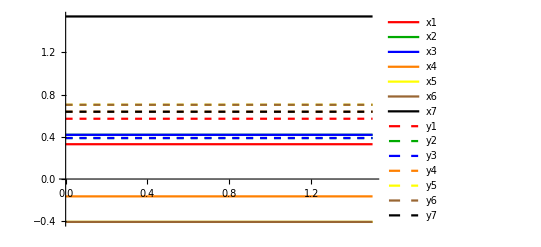

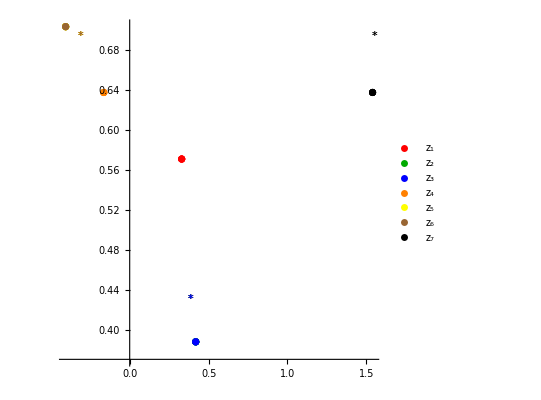

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
pointFoundCut=pointFound//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotPointFound=ListPlot[{#}&/@pointFoundCut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

#### Start finetuning

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
(* Save this initial guess *)
useEuclDistance=True;
distanceBeginAndEnd=False;
distance=getDistanceEndFlow[solution,goal];
ansatzValues={α2, α3,α4}/.getAlphaRule[ansatz];
f=Association[ansatzValues->distance];
allExplorations=Association[rmax->f]
```

<|1.5→<|{0,0,0}→1.43032|>|>

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansion3Rescaled;
flowEqs=flowEqs3;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
firstRmax=rmax;
maxRmax=5;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-5; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];
(* Define stuff for the 'stages" *)
stageNumber=0;
rmaxList={17};
roundCount=0;
numberOfRounds=1;
initialStepSizeList={1,0.01};
rmaxIncrementList={0.1, 0.5};
initialStepSizeFactorDecreaseList={1,1,1,1};
stepSizeFactorDecreaseList={0.1,0.1,0.1,0.1};
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[rmax==firstRmax ||(stageNumber!=0&&rmax>=rmaxList[[stageNumber]]),(
(* Set everything up or update *)
stageNumber+=1;
initialStepSize=initialStepSizeList[[stageNumber]];
rmaxIncrement=rmaxIncrementList[[stageNumber]];
initialStepSizeFactorDecrease=initialStepSizeFactorDecreaseList[[stageNumber]];
stepSizeFactorDecrease=stepSizeFactorDecreaseList[[stageNumber]];
)];
(* Starting fresh rmax, so clear explored & count *)
exploredParamVals={};
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* For all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Tuning parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Initialize everything for new parameter finetuning *)
directionFound=False;
stepDecreaseCount=0;
stepSize=initialStepSize;
(* === Finetune: as long as divisoun count did not hit max === *)
While[stepDecreaseCount!=maxStepDecrease,
(* Get the correct rmax association & current best: *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(If[directionFound==False,
(
(* Check all directions, choose best direction, if not already tuned *)
(* Go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Finding correct direction for nr ``. Parameter values: ``.",p,upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
(* Save as better guess & explored *)
newMinimalValue=bestDistance;
newMinimalValueKey=currentValues;
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
),
(* Here, we found a direction, and explore further *)
(
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["No improvement. Step back:  s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)]
)]
),
((* You've hit a point that was already explored so decrease step size & look in both directions *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
directionFound=False;
Print[StringForm["Already explored s: ``. Count: ``/``",stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
)])
];
)];
)];
)];
roundCount=roundCount+1;
Print[StringForm["Tuned all params. Round ``/``",roundCount,numberOfRounds]];
stepSize=initialStepSize;
If[roundCount==numberOfRounds,
(roundCount=0;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,10^8];
If[distance==10^8,(
Print["WARNING: Current best blew up. Something is terribly wrong"];
Abort[];)];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
),
(
Print["Max number of rounds not reached yet. Doing nothing"];
)];
)];
Print["THE END"];
]
```

=== === rmax: 1.5 === ===

Tuning parameter: 1.

Current best: {0,0,0}. Distance: 1.43032.

Finding correct direction for nr 1. Parameter values: {1,0,0}.

Distance: 1.452933032.

Parameter values: {-1,0,0}.

Distance: 1.413570897.

Direction found.

Current best: {-1,0,0}. Distance: 1.41357.

Parameter values: {-2,0,0}.

Distance: 1.402506654.

Current best: {-2,0,0}. Distance: 1.40251.

Parameter values: {-3,0,0}.

Distance: 1.396932577.

Current best: {-3,0,0}. Distance: 1.39693.

Parameter values: {-4,0,0}.

Distance: 1.396619143.

Current best: {-4,0,0}. Distance: 1.39662.

Parameter values: {-5,0,0}.

Distance: 1.401303772.

No improvement. Step back:  s: 0.1. Count: 1/10

Current best: {-4,0,0}. Distance: 1.39662.

Finding correct direction for nr 1. Parameter values: {-3.9,0.,0.}.

Distance: 1.396421114.

Parameter values: {-4.1,0.,0.}.

Distance: 1.39686715.

Direction found.

Current best: {-3.9,0.,0.}. Distance: 1.39642.

Parameter values: {-3.8,0.,0.}.

Distance: 1.396273337.

Current best: {-3.8,0.,0.}. Distance: 1.39627.

Parameter values: {-3.7,0.,0.}.

Distance: 1.396176084.

Current best: {-3.7,0.,0.}. Distance: 1.39618.

Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Parameter values: {-3.5,0.,0.}.

Distance: 1.396134235.

No improvement. Step back:  s: 0.01. Count: 2/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.59,0.,0.}.

Distance: 1.396127785.

Parameter values: {-3.61,0.,0.}.

Distance: 1.396131979.

Direction not found. Step back: s: 0.001. Count: 3/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.599,0.,0.}.

Distance: 1.39612942.

Parameter values: {-3.601,0.,0.}.

Distance: 1.396129839.

Direction not found. Step back: s: 0.0001. Count: 4/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.5999,0.,0.}.

Distance: 1.396129606.

Parameter values: {-3.6001,0.,0.}.

Distance: 1.396129648.

Direction not found. Step back: s: 0.00001. Count: 5/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.59999,0.,0.}.

Distance: 1.396129625.

Parameter values: {-3.60001,0.,0.}.

Distance: 1.396129629.

Direction not found. Step back: s: 1.×10^-6. Count: 6/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Direction not found. Step back: s: 1.×10^-7. Count: 7/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Direction not found. Step back: s: 1.×10^-8. Count: 8/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Direction not found. Step back: s: 1.×10^-9. Count: 9/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 1. Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Parameter values: {-3.6,0.,0.}.

Distance: 1.396129627.

Direction not found. Step back: s: 1.×10^-10. Count: 10/10

Maximum tuning achieved for this parameter!

Tuning parameter: 2.

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 2. Parameter values: {-3.6,1.,0.}.

Distance: 1.411685016.

Parameter values: {-3.6,-1.,0.}.

Distance: 1.440849142.

Direction not found. Step back: s: 0.1. Count: 1/10

Current best: {-3.6,0.,0.}. Distance: 1.39613.

Finding correct direction for nr 2. Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Parameter values: {-3.6,-0.1,0.}.

Distance: 1.396942041.

Direction found.

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Parameter values: {-3.6,0.2,0.}.

Distance: 1.396158433.

No improvement. Step back:  s: 0.01. Count: 2/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.11,0.}.

Distance: 1.39589096.

Parameter values: {-3.6,0.09,0.}.

Distance: 1.39588639.

Direction not found. Step back: s: 0.001. Count: 3/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.101,0.}.

Distance: 1.395886352.

Parameter values: {-3.6,0.099,0.}.

Distance: 1.395885893.

Direction not found. Step back: s: 0.0001. Count: 4/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.1001,0.}.

Distance: 1.39588612.

Parameter values: {-3.6,0.0999,0.}.

Distance: 1.395886074.

Direction not found. Step back: s: 0.00001. Count: 5/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.10001,0.}.

Distance: 1.395886099.

Parameter values: {-3.6,0.09999,0.}.

Distance: 1.395886095.

Direction not found. Step back: s: 1.×10^-6. Count: 6/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.100001,0.}.

Distance: 1.395886097.

Parameter values: {-3.6,0.099999,0.}.

Distance: 1.395886097.

Direction not found. Step back: s: 1.×10^-7. Count: 7/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Parameter values: {-3.6,0.0999999,0.}.

Distance: 1.395886097.

Direction not found. Step back: s: 1.×10^-8. Count: 8/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Direction not found. Step back: s: 1.×10^-9. Count: 9/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 2. Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Parameter values: {-3.6,0.1,0.}.

Distance: 1.395886097.

Direction not found. Step back: s: 1.×10^-10. Count: 10/10

Maximum tuning achieved for this parameter!

Tuning parameter: 3.

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,1.}.

Parameter values: {-3.6,0.1,-1.}.

Direction not found. Step back: s: 0.1. Count: 1/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,0.1}.

Parameter values: {-3.6,0.1,-0.1}.

Direction not found. Step back: s: 0.01. Count: 2/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,0.01}.

Distance: 1.440414161.

Parameter values: {-3.6,0.1,-0.01}.

Distance: 1.424025545.

Direction not found. Step back: s: 0.001. Count: 3/10

Current best: {-3.6,0.1,0.}. Distance: 1.39589.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,0.001}.

Distance: 1.397637737.

Parameter values: {-3.6,0.1,-0.001}.

Distance: 1.394856316.

Direction found.

Current best: {-3.6,0.1,-0.001}. Distance: 1.39486.

Parameter values: {-3.6,0.1,-0.002}.

Distance: 1.394583273.

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Parameter values: {-3.6,0.1,-0.003}.

Distance: 1.395101999.

No improvement. Step back:  s: 0.0001. Count: 4/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.0019}.

Distance: 1.394575527.

Parameter values: {-3.6,0.1,-0.0021}.

Distance: 1.394598936.

Direction not found. Step back: s: 0.00001. Count: 5/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.00199}.

Distance: 1.394582143.

Parameter values: {-3.6,0.1,-0.00201}.

Distance: 1.394584482.

Direction not found. Step back: s: 1.×10^-6. Count: 6/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.001999}.

Distance: 1.394583156.

Parameter values: {-3.6,0.1,-0.002001}.

Distance: 1.39458339.

Direction not found. Step back: s: 1.×10^-7. Count: 7/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.0019999}.

Distance: 1.394583261.

Parameter values: {-3.6,0.1,-0.0020001}.

Distance: 1.394583285.

Direction not found. Step back: s: 1.×10^-8. Count: 8/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.00199999}.

Distance: 1.394583272.

Parameter values: {-3.6,0.1,-0.00200001}.

Distance: 1.394583274.

Direction not found. Step back: s: 1.×10^-9. Count: 9/10

Current best: {-3.6,0.1,-0.002}. Distance: 1.39458.

Finding correct direction for nr 3. Parameter values: {-3.6,0.1,-0.002}.

Distance: 1.394583273.

Parameter values: {-3.6,0.1,-0.002}.

Distance: 1.394583273.

Direction not found. Step back: s: 1.×10^-10. Count: 10/10

Maximum tuning achieved for this parameter!

Tuned all params. Round 1/1

Updating distance for min value key . . .

Distance: 1.408272584.

=== === rmax: 1.6 === ===

Tuning parameter: 1.

Current best: {-3.6,0.1,-0.002}. Distance: 1.40827.

Finding correct direction for nr 1. Parameter values: {-2.6,0.1,-0.002}.

Distance: 1.395514266.

Parameter values: {-4.6,0.1,-0.002}.

Distance: 1.430866216.

Direction found.

Current best: {-2.6,0.1,-0.002}. Distance: 1.39551.

Parameter values: {-1.6,0.1,-0.002}.

Distance: 1.393185734.

Current best: {-1.6,0.1,-0.002}. Distance: 1.39319.

Parameter values: {-0.6,0.1,-0.002}.

Distance: 1.402041189.

No improvement. Step back:  s: 0.1. Count: 1/10

Current best: {-1.6,0.1,-0.002}. Distance: 1.39319.

Finding correct direction for nr 1. Parameter values: {-1.5,0.1,-0.002}.

Distance: 1.39355596.

Parameter values: {-1.7,0.1,-0.002}.

Distance: 1.392927471.

Direction found.

Current best: {-1.7,0.1,-0.002}. Distance: 1.39293.

Parameter values: {-1.8,0.1,-0.002}.

Distance: 1.392780421.

Current best: {-1.8,0.1,-0.002}. Distance: 1.39278.

Parameter values: {-1.9,0.1,-0.002}.

Distance: 1.39274382.

Current best: {-1.9,0.1,-0.002}. Distance: 1.39274.

Parameter values: {-2.,0.1,-0.002}.

$Aborted

## Check the results

Had: {-0.4699999999999999,0.189,0.00123}

```mathematica
Put[allExplorations,"explorations_SO2"]
(*Put[expansion1Crit5RescaledRvalue,"expansion1Crit5RescaledRvalue"]*)
```

```mathematica
Keys[allExplorations]
```

{1,1.1}

```mathematica
finalRmax=Max[Keys[allExplorations]]
final=allExplorations[finalRmax];
finalValues=getKeyMinValue[final];
finalDistance=final[finalValues];
NumberForm[finalValues,20]
```

2.5

{0.02300000000000004,0.03900000000000001,-0.0003600000000000003}

```mathematica
(* Get IC ready *)
IC = expansion3Rescaled/.getAlphaRule[finalValues];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
(* Solve - rmax is for the range of r *)
rmax=finalRmax;
solution = TimeConstrained[NDSolve[Join[flowEqs3, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,(distance=10^(8);Print["Blew up!"])];
```

{x1[0]==0.334157,y1[0]==0.553511,x2[0]==0.413078,y2[0]==0.392899,x3[0]==0.413078,y3[0]==0.392899,x4[0]==-0.175916,y4[0]==0.640814,x5[0]==-0.39958,y5[0]==0.703403,x6[0]==-0.39958,y6[0]==0.703403,x7[0]==1.54132,y7[0]==0.641596}

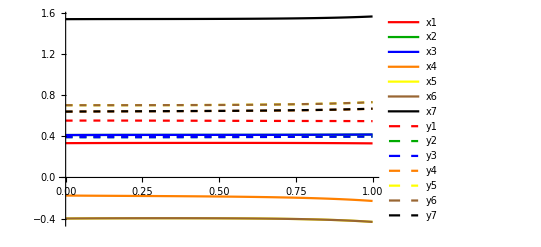

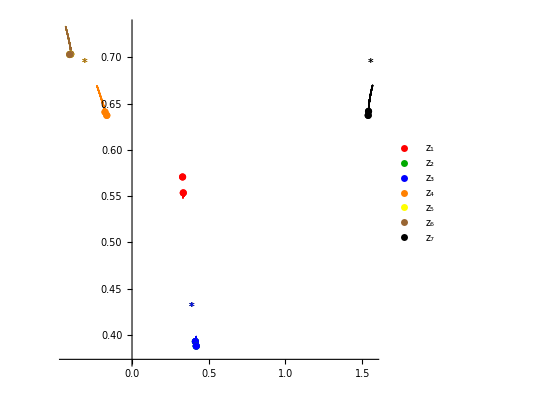

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

# ============================================================ ======================== Archive ============================= ============================================================

#### Finetune --- OLD VERSION

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Initializations *)
numberOfIterations=200;
numberOfParams=3;
startIndex=2;
continue=False;
initialStepSize=0.1;
rmaxIncrement=0.1;
stepSizeFactorDecrease=0.5;
maxStepSize=1;
timeLimit=50;
improvementMade=False;
noImprovementCount=0;
maxNoImprovementCount=10;
thresholdDistance=10^-3;
Timing[
(* If we are beginning from scratch, initialize the step size *)
If[continue==False,
(stepSize=initialStepSize;
exploredParamVals={};
)];
(* Start exploring. Once an iteration gave a very short distance, stop improving *)
For[n=1,n<numberOfIterations+1,n++,
If[distance<tresholdDistance,(
Print["Threshold value reached. Exiting loop"];
Break[];
)];
Print[StringForm["Now at iteration: ``/``.",n,numberOfIterations]];
(* Search for which key the value is minimal right now, save *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
(* After step 1, we check if we found a new minimum or not. *)
If[n!=1,
If[previousMinimalValueKey!=newMinimalValueKey,
(
(* If we have new minimum, report and proceed  *)
Print[StringForm["New minimum found at: `` w. ``.",newMinimalValueKey,newMinimalValue]];
improvementMade=True;
noImprovementCount=0;
),
(* Else, if we are at the same minimum, check if we made improvement before or not *)
(If[improvementMade==True,
((* If minimum distance was improved before, increase rmax, decrease step size and start new association *)
Print[StringForm["No new minimum reported (now: `` w. ``). rmax is now ``",newMinimalValueKey,newMinimalValue,rmax+rmaxIncrement]];
(* Prepare to go to next stage. Reset step size *)
stepSize=initialStepSize;
improvementMade=False;
rmax=rmax+rmaxIncrement;
Print["Updating distance for min value key . . . "];
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[newMinimalValueKey],timeLimit,Null];
(* Start a new association & clear explored values *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
exploredParamVals={};
),
(* If we did not improve before: *)
If[noImprovementCount==maxNoImprovementCount,
((* If minimum distance was improved before, increase rmax, decrease step size and start new association *)
Print[StringForm["No new minimum reported (now: `` w. ``). rmax is now ``",newMinimalValueKey,newMinimalValue,rmax+rmaxIncrement]];
(* Prepare to go to next stage. Reset step size *)
stepSize=initialStepSize;
improvementMade=False;
rmax=rmax+rmaxIncrement;
Print["Updating distance for min value key . . . "];
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[newMinimalValueKey],timeLimit,Null];
(* Start a new association & clear explored values *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
exploredParamVals={};
noImprovementCount=0;
),
(* Else, decrease the step size *)
(stepSize=stepSize*stepSizeFactorDecrease;
noImprovementCount+=1;
Print[StringForm["No improvement seen (``/``). Decreasing step size to s = ``",noImprovementCount,maxNoImprovementCount,stepSize]];
)];
];
)];
];
(* Explore the nearest neighbours*)
For[i=1,i<numberOfParams+1,i++,(
(* Clear previous solution, to make space available *)
Clear[solution];
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[i]]=1;
(* Now go up in this direction BUT check if already explored *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,upParamValues]],
(
Print[StringForm["Parameter values: ``.",upParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[upParamValues],timeLimit,Null];
AppendTo[allExplorations[rmax],{upParamValues->distance}];
(* Save the fact that we already explored this *)
AppendTo[exploredParamVals,upParamValues];
);
];
(* Now go down in this direction BUT check if already explored *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,downParamValues]],
(
Print[StringForm["Parameter values: ``.",downParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[downParamValues],timeLimit,Null];
AppendTo[allExplorations[rmax],{downParamValues->distance}];
(* Save the fact that we already explored this *)
AppendTo[exploredParamVals,downParamValues];
);
];
);
];
(* Go to next step: save previous min value key in explored *)
previousMinimalValueKey=newMinimalValueKey;
AppendTo[exploredParamVals,previousMinimalValueKey];
If[n==numberOfIterations,
Print["Max number of iterations reached."];
Print[StringForm["Current best: ``. Step size: ``. rmax: ``",newMinimalValueKey,stepSize,rmax]];
currentBest=newMinimalValueKey;
]
];
]
```

## === === === === === SECOND VERSION OF THE ALGORITHM === === === === ===

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
rmax=5;
(* Create a large association containing explorations organized per value of rmax *)
allExplorations=Association[rmax->f]
```

#### Finetune

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Initializations *)
numberOfIterations=2;
numberOfParams=3;
startIndex=2;
continue=False;
initialStepSize=0.1;
stepSize=initialStepSize;
rmaxIncrement=0.5;
stepSizeFactorDecrease=0.5;
stepDecreaseCount=0;
maxStepDecrease=2;
timeLimit=50;
thresholdDistance=10^-3;
(* List to save indices of parameters already finetuned *)
tunedIndices={};
maxRmax=7;
initialRmax=5;
While[rmax<maxRmax,
(
For[p=1,p<numberOfParams+1,p++,(
(* Search for which key the value is minimal right now, save *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
(* Reset rmax etc *)
rmax=initialRmax;
exploredParamVals={};
(* Check all directions, choose best direction, if not already tuned *)
Print["Exploring phase . . ."];
directions=Association[];
directionsValues=Association[];
directionsSigns=Association[];
For[i=1,i<numberOfParams+1,i++,
((* Check if parameter has not been finetuned yet. If not, explore as well *)
If[Not[MemberQ[tunedIndices,i]],
(
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[i]]=1;
(* Now go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Parameter values: ``.",upParamValues]];
upDistance=TimeConstrained[doRGFlowGetCosmologicalDistance[upParamValues],timeLimit,Null];
(* Now go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetCosmologicalDistance[downParamValues],timeLimit,Null];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
AppendTo[directions, i->bestDistance];
(* Also save "up or down" *)
If[bestDistance==upDistance,
(AppendTo[directionsSigns,i->+1];
AppendTo[directionsValues,i->upParamValues];),
(AppendTo[directionsSigns,i->-1];
AppendTo[directionsValues,i->downParamValues];)];
);
];
);
];
(* Choose optimal direction *)
currentIndex=Keys[MinimalBy[Value][directions]][[1]];
sign=directionsSigns[currentIndex];
currentValues=directionsValues[currentIndex];
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Save the fact that we already explored this *)
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
Print[StringForm["Tuning parameter: ``.",currentIndex]];
(* --- FINETUNE THIS PARAMETER --- *)
firstIteration=True;
While[stepDecreaseCount!=maxStepDecrease,(
(* Search for which key the value is minimal right now, save *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
(* After step 1, check if we found a new minimum or not. *)
If[firstIteration==False,
If[previousMinimalValueKey!=newMinimalValueKey,
((* If we have new minimum, report and proceed  *)
Print[StringForm["New minimum found at: `` w. ``.",newMinimalValueKey,newMinimalValue]];
),
(Print["If you see this, something is terribly wrong."];
Abort[];)];
];
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
firstIteration=False;
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];
(* Save the fact that we already explored this *)
previousMinimalValueKey=newMinimalValueKey;),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)]
),
((* You've hit a point that was already explored so decrease step size *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)])
];
)];
);
];
Print["Tuned all params. Increasing rmax. Updating distance for min value key . . . "];
stepSize=initialStepSize;
rmax=rmax+rmaxIncrement;
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
distance=TimeConstrained[doRGFlowGetCosmologicalDistance[newMinimalValueKey],timeLimit,Null];
(* Start a new association & clear explored values *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
exploredParamVals={};
)];
```

## === === === === === THIRD VERSION OF THE ALGORITHM === === === === ===

```mathematica
(* The goal we want to reach - this is 1/L with L the AdS length scale of the goal point *)
index=1;
goal=critPoints2Sigma[[index]]/.{c->1,g->1, chi1->0,chi2->0}//N//refine
```

```mathematica
ansatz={α2->1,α3->-1,α4->1};
```

```mathematica
(* Get IC ready *)
IC = expansion2Crit1Rescaled/.ansatz;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
```

```mathematica
(* Solve - rmax is for the range of r *)
rstart=0;
rmax=3;
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, rstart, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],40,(distance=10^(8);Print["no"])];
```

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, rstart, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, rstart, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, rstart, rmax},Evaluate[mystyleImScalars]];
plotIC=ListPlot[IC//cut,PlotStyle->colorsRF];
(* Show desired plots *)
Show[plotReScalars]
Show[plotImScalars]
Show[plotComplexScalars,plotIC]
```

NOTE: Now save the distance we have between start and finish USING ONLY 4 scalars.

```mathematica
getDistanceEndFlow4Scalars[solution_,target_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
endValuesHere4Scalars=Table[endValuesHere[[i]],{i,7,14}];
target4Scalars=Table[target[[i]],{i,7,14}];
distanceHere=EuclideanDistance[endValuesHere4Scalars,target4Scalars];
Return[distanceHere];
);
```

```mathematica
distance=getDistanceEndFlow[solution,goal]
```

Now that we have a first guess, let us save it in an association.

```mathematica
ansatzValues={α2,α3,α4}/.ansatz;
f=Association[ansatzValues->distance]
```

```mathematica
getAlphaRule[paramValues_]:=(
(* Startindex: sometimes, we can rescale and already choose a value for α1 *)
partAlpha=alpha[[startIndex;;startIndex+numberOfParams ]];
returnValue=Table[partAlpha[[i]]->paramValues[[i]],{i,1,Length[paramValues]}];
Return[returnValue];
);
doRGFlowGetDistance[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! NOTE requires an expansion *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve NOTE have to specify the flow equations *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getDistanceEndFlow[solution,goal];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
```

#### Give us something to start with:

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
rmax=3;
(* Create a large association containing explorations organized per value of rmax *)
allExplorations=<|rmax-><|{1,-1,1}->0.6240286940250567|>|>
```

#### Finetune

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
continue=False;
If[continue==True,
(Print["Continuing . . ."];
initialStepSize=stepSize;),
(Print["Starting again . . . "];
initialStepSize=0.1;)];
initialStepSizeFactorDecrease=1;
stepSize=initialStepSize;
stepSizeFactorDecrease=0.5;
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
rmaxIncrement=0.5;
maxRmax=5;
(* Thresholds *)
timeLimit=50;
thresholdDistance=10^-3;
Clear[previousMinimalValueKey];(* for debugging... *)
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[Not[firstRound],
((* After first round, we decrease initial stepsize *)
initialStepSize=initialStepSize*initialStepSizeFactorDecrease;
stepSize=initialStepSize;
Print[StringForm["Initial step size: ``",initialStepSize]];
),
((* We are in 1st round: next time no longer *)
firstRound=False;
)];
(* If not at first*)
(* Starting fresh rmax, so clear explored *)
exploredParamVals={};
stepDecreaseCount=0;
(Print[StringForm["rmax: ``",rmax]];
(* Iterate over all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Search for which key the value is minimal right now *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
directionFound=False;
stepDecreaseCount = 0;
While[directionFound==False &&stepDecreaseCount!=maxStepDecrease,
(
(* Check all directions, choose best direction, if not already tuned *)
Print[StringForm["Finding correct direction for parameter nr ``.",p]];
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[p]]=1;
(* Now go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Parameter values: ``.",upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Now go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
)];
(* Current direction *)
currentIndex=p;
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Save the fact that we already explored this *)
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
Print[StringForm["Tuning parameter: ``.",currentIndex]];
(* --- FINETUNE THIS PARAMETER --- *)
firstIteration=True;
While[stepDecreaseCount!=maxStepDecrease,(
(* Search for which key the value is minimal right now, save *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
(* After step 1, check if we found a new minimum or not. *)
If[firstIteration==False,
If[previousMinimalValueKey!=newMinimalValueKey,
((* If we have new minimum, report and proceed  *)
Print[StringForm["New minimum found at: `` w. ``.",newMinimalValueKey,newMinimalValue]];
),
(Print["Min value key did not improve: ending tuning session here"];
stepSize=initialStepSize;
Break[];)];
];
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
firstIteration=False;
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];
(* Save the fact that we already explored this *)
previousMinimalValueKey=newMinimalValueKey;),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)]
),
((* You've hit a point that was already explored so decrease step size *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)])
];
)];
);
];
Print["Tuned all params. Going to increase rmax. "];
stepSize=initialStepSize;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,Null];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
)];
Print["THE END"];
]
```

## ========================

## 21/03/2022 een versie van het algoritme dat zeer hoopvol was!!!!!!!!

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][currentExploration]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=guarinoSterckx;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
initialStepSize=0.01;
initialStepSizeFactorDecrease=0.1;
stepSize=initialStepSize;
stepSizeFactorDecrease=0.1;
stepDecreaseCount=0;
maxStepDecrease=10;
(* rmax info *)
(* Get the latest rmax *)
rmax=Max[Keys[allExplorations]];
rmaxIncrement=1;
maxRmax=15;
(* Thresholds *)
timeLimit=50;
thresholdImprovement=10^-4; (* Only go forward if we improve by enough *)
Clear[previousMinimalValueKey];(* for debugging... *)
Timing[
firstRound=True;
(* --- Start --- *)
While[rmax<maxRmax,
If[Not[firstRound],
((* After first round, we decrease initial stepsize *)
initialStepSize=initialStepSize*initialStepSizeFactorDecrease;
stepSize=initialStepSize;
Print[StringForm["Initial step size: ``",initialStepSize]];
),
((* We are in 1st round: next time no longer *)
firstRound=False;
)];
(* If not at first*)
(* Starting fresh rmax, so clear explored *)
exploredParamVals={};
stepDecreaseCount=0;
(Print[StringForm["=== === rmax: `` === ===",rmax]];
(* Iterate over all the parameters p *)
For[p=1,p<numberOfParams+1,p++,(
(* Search for which key the value is minimal right now *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
directionFound=False;
stepDecreaseCount=0;
While[directionFound==False &&stepDecreaseCount!=maxStepDecrease,
(
(* Check all directions, choose best direction, if not already tuned *)
Print[StringForm["Finding correct direction for parameter nr ``.",p]];
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[p]]=1;
(* Now go up in this direction *)
upParamValues=newMinimalValueKey +stepSize*unitVector;
Print[StringForm["Parameter values: ``.",upParamValues]];
upDistance=TimeConstrained[doRGFlowGetDistance[upParamValues],timeLimit,10^(8)];
(* Now go down in this direction *)
downParamValues=newMinimalValueKey -stepSize*unitVector;
Print[StringForm["Parameter values: ``.",downParamValues]];
downDistance=TimeConstrained[doRGFlowGetDistance[downParamValues],timeLimit,10^(8)];
(* Save best distance for this parameter to choose later *)
bestDistance=Min[upDistance,downDistance];
If[bestDistance<=newMinimalValue - thresholdImprovement,
(* We have found a direction where improved *)
(directionFound=True;
Print["Direction found."];
If[bestDistance==upDistance,
(sign=+1;
currentValues=upParamValues;),
(sign=-1;
currentValues=downParamValues;)];
),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Direction not found. Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)];
)];
(* Current direction *)
currentIndex=p;
(* Get vector with '1' on index i, '0' elsewhere - to update parameter i *)
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
(* Save the fact that we already explored this *)
AppendTo[exploredParamVals,currentValues];
AppendTo[allExplorations[rmax],{currentValues->bestDistance}];
Print[StringForm["Tuning parameter: ``.",currentIndex]];
(* --- FINETUNE THIS PARAMETER --- *)
firstIteration=True;
While[stepDecreaseCount!=maxStepDecrease,(
(* Search for which key the value is minimal right now, save *)
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
newMinimalValue=currentExploration[newMinimalValueKey];
(* After step 1, check if we found a new minimum or not. *)
If[firstIteration==False,
If[previousMinimalValueKey!=newMinimalValueKey,
((* If we have new minimum, report and proceed  *)
Print[StringForm["New minimum found at: `` w. ``.",newMinimalValueKey,newMinimalValue]];
),
(Print["Min value key did not improve: ending tuning session here"];
stepDecreaseCount=maxStepDecrease)];
];
(* Go down/up BUT check if already explored *)
newParamValues=newMinimalValueKey +sign*stepSize*unitVector;
If[Not[MemberQ[exploredParamVals,newParamValues]],
(
Print[StringForm["Parameter values: ``.",newParamValues]];
(* The following does the RG flow, but under a time limit: can blow up *)
distance=TimeConstrained[doRGFlowGetDistance[newParamValues],timeLimit,10^(8)];
AppendTo[exploredParamVals,newParamValues];
firstIteration=False;
(* Check if is a new minimum or not *)
If[distance<=newMinimalValue-thresholdImprovement,
((* Save + keep on going in this direction (don't change anything) *)
AppendTo[allExplorations[rmax],{newParamValues->distance}];
(* Save the fact that we already explored this *)
previousMinimalValueKey=newMinimalValueKey;),
((* In case we increased distance or blew up, half step size, change direction, up the count *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)]
)]
),
((* You've hit a point that was already explored so decrease step size *)
stepSize=stepSize*stepSizeFactorDecrease;
stepDecreaseCount+=1;
(*sign=sign*(-1);*)(* need to think about this! *)
Print[StringForm["Step back: sign: ``, s: ``. Count: ``/``",sign,stepSize,stepDecreaseCount,maxStepDecrease]];
If[stepDecreaseCount==maxStepDecrease,
(Print["Maximum tuning achieved for this parameter!"];
stepSize=initialStepSize;)])
];
)];
);
];
Print["Tuned all params. Going to increase rmax. "];
stepSize=initialStepSize;
Print["Updating distance for min value key . . . "];
currentExploration=allExplorations[rmax];
newMinimalValueKey=Keys[MinimalBy[Value][currentExploration]][[1]];
rmax=rmax+rmaxIncrement;
distance=TimeConstrained[doRGFlowGetDistance[newMinimalValueKey],timeLimit,Null];
(* Start a new association *)
AssociateTo[allExplorations,rmax->Association[newMinimalValueKey->distance]];
)];
Print["THE END"];
]
```

## Extra: getting the masses and the scaling dimensions

```mathematica
potential2RF=potential3//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential2RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### #1

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPoints3[[index]]/.{g->1,c->1};
potentialValue=potentialValues3[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22321,-2.22222,-2.22222,-1.55059,-0.888889,-0.888889,3.42004,4.74423,4.74423,9.1824,10.2209,11.0335,11.0335,18.2838}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33631,1.66369},{1.33333,1.66667},{1.33333,1.66667},{0.663692,2.33631},{0.333333,2.66667},{0.333333,2.66667},{-0.881184,3.88118},{-1.14466,4.14466},{-1.14466,4.14466},{-1.88118,4.88118},{-2.03142,5.03142},{-2.14466,5.14466},{-2.14466,5.14466},{-3.03142,6.03142}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66369,1.66667,1.66667,2.33631,2.66667,2.66667,3.88118,4.14466,4.14466,4.88118,5.03142,5.14466,5.14466,6.03142}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33631,1.33333,1.33333,0.663692,0.333333,0.333333,-0.881184,-1.14466,-1.14466,-1.88118,-2.03142,-2.14466,-2.14466,-3.03142}

```mathematica
(* First part *)
Table[allMasses[[i]],{i,1,7}]
```

{-2.22321,-2.22222,-2.22222,-1.55059,-0.888889,-0.888889,3.42004}

```mathematica
Table[deltaPlus[[i]],{i,1,7}]
```

{1.66369,1.66667,1.66667,2.33631,2.66667,2.66667,3.88118}

```mathematica
Table[deltaMinus[[i]],{i,1,7}]
```

{1.33631,1.33333,1.33333,0.663692,0.333333,0.333333,-0.881184}

```mathematica
(* Second part *)
Table[allMasses[[i]],{i,8,14}]
```

{4.74423,4.74423,9.1824,10.2209,11.0335,11.0335,18.2838}

```mathematica
Table[deltaPlus[[i]],{i,8,14}]
```

{4.14466,4.14466,4.88118,5.03142,5.14466,5.14466,6.03142}

```mathematica
Table[deltaMinus[[i]],{i,8,14}]
```

{-1.14466,-1.14466,-1.88118,-2.03142,-2.14466,-2.14466,-3.03142}

#### #2

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPoints3[[index]]/.{g->1,c->1};
potentialValue=potentialValues3[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetric//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.21279,-2.19952,-1.64889,-1.59858,-1.42805,1.38518,3.35737,3.77399,6.93661,9.09334,9.56617,9.68275,13.9985,17.4411}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.30711,1.69289},{1.27532,1.72468},{0.724684,2.27532},{0.692894,2.30711},{0.593386,2.40661},{-0.406614,3.40661},{-0.867988,3.86799},{-0.954381,3.95438},{-1.53094,4.53094},{-1.86799,4.86799},{-1.93747,4.93747},{-1.95438,4.95438},{-2.53094,5.53094},{-2.93747,5.93747}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.69289,1.72468,2.27532,2.30711,2.40661,3.40661,3.86799,3.95438,4.53094,4.86799,4.93747,4.95438,5.53094,5.93747}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.30711,1.27532,0.724684,0.692894,0.593386,-0.406614,-0.867988,-0.954381,-1.53094,-1.86799,-1.93747,-1.95438,-2.53094,-2.93747}

```mathematica
(* First part *)
Table[allMasses[[i]],{i,1,7}]
```

{-2.21279,-2.19952,-1.64889,-1.59858,-1.42805,1.38518,3.35737}

```mathematica
Table[deltaPlus[[i]],{i,1,7}]
```

{1.69289,1.72468,2.27532,2.30711,2.40661,3.40661,3.86799}

```mathematica
Table[deltaMinus[[i]],{i,1,7}]
```

{1.30711,1.27532,0.724684,0.692894,0.593386,-0.406614,-0.867988}

```mathematica
(* Second part *)
Table[allMasses[[i]],{i,8,14}]
```

{3.77399,6.93661,9.09334,9.56617,9.68275,13.9985,17.4411}

```mathematica
Table[deltaPlus[[i]],{i,8,14}]
```

{3.95438,4.53094,4.86799,4.93747,4.95438,5.53094,5.93747}

```mathematica
Table[deltaMinus[[i]],{i,8,14}]
```

{-0.954381,-1.53094,-1.86799,-1.93747,-1.95438,-2.53094,-2.93747}

# === GS algorithm (archived) ===

## === GS ALGORITHM - inspired by Guarino & Sterckx ===

WATCH OUT MINUS SIGN DIFFERENCE

```mathematica
expansion1Crit6RescaledRvalue
```

{-0.11026+7.3743×10^-9 α2+8.57243×10^-8 α3-0.0000306255 α4,0.762911-6.41327×10^-8 α2+2.84944×10^-7 α3+0.0000301379 α4,0.836439+4.83799×10^-8 α2-3.08635×10^-7 α3+0.000141175 α4,0.390702+2.79997×10^-8 α2+1.15781×10^-6 α3-7.78894×10^-6 α4,-0.402122-1.93121×10^-8 α2+4.51949×10^-9 α3-0.000234136 α4,0.312003+3.83939×10^-8 α2+1.56054×10^-6 α3+9.09488×10^-6 α4,-0.944882+3.19644×10^-8 α2+7.15303×10^-8 α3-0.0000909552 α4,1.44057+4.62274×10^-8 α2-1.29675×10^-8 α3+0.0000525542 α4,-0.11026+7.3743×10^-9 α2+8.57243×10^-8 α3-0.0000306255 α4,0.762911-6.41327×10^-8 α2+2.84944×10^-7 α3+0.0000301379 α4,0.836439+4.83799×10^-8 α2-3.08635×10^-7 α3+0.000141175 α4,0.390702+2.79997×10^-8 α2+1.15781×10^-6 α3-7.78894×10^-6 α4,0.740186-7.71514×10^-8 α2-6.22635×10^-8 α3-0.0000125812 α4,1.15257-2.21192×10^-9 α2+1.72987×10^-7 α3+0.0000944822 α4}

#### Playing around

```mathematica
(* Get IC ready *)
ansatz={0,0,0}; (* 14/04 failed explorations had (0,5,0) *)
numberOfParams=3;
startIndex=2;
IC = expansion1Crit6RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC- fpSigma]//cut
(* Solve - rmax is for the range of r *)
rmax=5;
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],45,Print["Blew up!"]];
```

{x1[0]==-0.11026,y1[0]==0.762911,x2[0]==0.836439,y2[0]==0.390702,x3[0]==-0.402122,y3[0]==0.312003,x4[0]==-0.944882,y4[0]==1.44057,x5[0]==-0.11026,y5[0]==0.762911,x6[0]==0.836439,y6[0]==0.390702,x7[0]==0.740186,y7[0]==1.15257}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

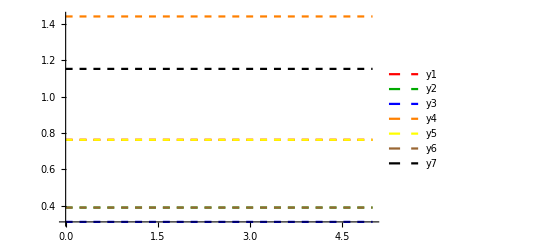

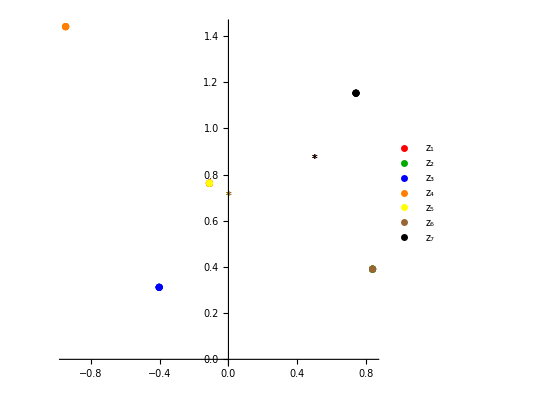

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars];
Show[plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

#### Start exploring

#### New function: save the end point of a regular flow

```mathematica
getEndPointsFlow[solution_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
Return[endValuesHere];
);
doRGFlowGetEndPoints[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end and return it *)
endPoints=getEndPointsFlow[solution];
Return[Association[paramVals->endPoints]];
);
getNearestNeighbours[ansatz_]:=
(
l=Length[ansatz];
zeroVector=Table[0,l];
returnValue={};
For[i=1,i<l+1,i++,
(unitVector=zeroVector;
unitVector[[i]]=stepSize;
neighbourUp=ansatz+unitVector;
neighbourDown=ansatz-unitVector;
AppendTo[returnValue,neighbourUp];
AppendTo[returnValue,neighbourDown];)
];
Return[returnValue];
);
stepSize=1;
getNearestNeighbours[{5,4,3}];
getSetDifference[list1_,list2_]:=
(
(* Returns elements of list2 that are NOT in list1 *)
set1=DeleteDuplicates[list1];
set2=DeleteDuplicates[list2];
returnValue={};
For[e=1,e<Length[set2]+1,e++,
(
element=set2[[e]];
If[Not[MemberQ[set1,element]],AppendTo[returnValue,element]]
)];
Return[returnValue];
)
getSetDifference[{1,2,3,4,5},{4,5,6,7,8}];
(* New function which, from earlier explorations, gets the current boundary to continue explorations *)
getNewPoints[explorations_]:=(
keysHere=Keys[explorations];
newPoints={};
For[k=1,k<Length[keysHere]+1,k++,
(
key=keysHere[[k]];
nn=getNearestNeighbours[key];
If[Not[SubsetQ[keysHere,nn]],AppendTo[newPoints,key]];
)
];
Return[newPoints];
)
```

## Finding the centre of polyhedron:

```mathematica
(* Define expansion & flow eqs to be used *)
newPoints={{0,0,0}};
Off[NDSolve::precw];
Print[StringForm["Looking for a centre of a polyhedron: starting from: ``, rmax: ``", newPoints[[1]],rmax]];
expansion=expansion1Crit6Rescaled
flowEqs=flowEqs1;
(* --- Initializations --- *)
stepSize=5;
rmax=5;
numberOfParams=3;
startIndex=2;
rmax=5;
timeLimit=50;
yBound=2;
(*newPoints=Keys[allExplorations];*)
Timing[
(* Initialize the explored parameter values with what's inside all explorations*)
exploredParamVals=newPoints;
(* PHASE I: get the nearest neighbours to explore *)
allNeighbours={};
found=False;
While[found==False,
(Print["On top"];
(* Get the nearest neighbours *)
For[q=1,q<Length[newPoints]+1,q++,
(
newPoint=newPoints[[q]];
nearestNeighbours=getNearestNeighbours[newPoint];
allNeighbours=Join[allNeighbours,nearestNeighbours];
)
];
allNeighbours=DeleteDuplicates[allNeighbours];
(* The values to explore are nearest neighbours that are NOT yet explored: *)
toExplore=getSetDifference[exploredParamVals,allNeighbours];
Print[StringForm["number toExplore: ``",Length[toExplore]]];
(* The iteration is over if this to explore list is empty! *)
If[Length[toExplore]==0,(Print["Nothing to explore? Aborting"];Abort[];)];
(* What we explore now, will be new points later. Also save as explored already *)
exploredParamVals=Join[exploredParamVals,toExplore];
newPoints=toExplore;
Clear[k];
(* Explore the new points *)
For[k=1,k<Length[toExplore]+1,k++,
(
Print[StringForm["Exploring: `` (``/``)",toExplore[[k]],k,Length[toExplore]]];
TimeConstrained[
(
result=doRGFlowGetEndPoints[toExplore[[k]]];
(* If evaluation is done within time limit, save the result! *)
Print["Done within time limit. Checking regularity . . ."];
key=Keys[result][[1]];
valsEnd=result[key];
yEnd=Table[valsEnd[[2*p]],{p,1,7}];
yMax=Max[yEnd];
If[yMax<=yBound,
(
Print["Regular flow found"];
Print[StringForm["At param vals: ``", toExplore[[k]]]];
Abort[];
)];
),timeLimit];
)];
)];
Print["THE END"];
];
```

## Expand the polyhedron

```mathematica
(* LOAD OR GET STARTING POINT *)
(*allExplorations=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/polyhedron-14-04-unfinished"];*)
(*exploredParamVals=Get["/exthome/user/r0708518/Documents/Wolfram Mathematica/NB5/explored-14-04"];*)
```

```mathematica
f=getEndPointsFlow[solution];
allExplorations=Association[{0,0,0}->{-0.11026031242462285327488964789628669598422874917964299920178088898909711003804`49.99999960754805,0.76291081028328875096609725907965656873597479048634469086858606872759249331471`49.99999997548574,0.83643906374914700495562870303094412712101075744421458719242267294464732950813`49.999999991199275,0.39070211207616071600920449682444894581522078784146545077437963865077704535906`49.999999990046554,-0.4021216839001861786013471008544804408501270104843016182870136509072760238656`49.99999996954079,0.31200321151636986516534300501273037151981770098641611406885719460669717557305`49.9999999962624,-0.94488216216521754913416670899718959673043186221537416382982470867873117889895`49.99999999503555,1.44057419290984477615301440505328134745866679106267650185352671369606545543141`49.999999964673755,-0.11026031242467687831421716301907568897855055450795973098771008611109980899373`49.99999960754617,0.76291081028323429393195971673017260062084106990955175478039313120525708078596`49.99999997548602,0.83643906374917088637409473811403581223354675801791552913935947736764639459285`49.99999999119916,0.39070211207616184978660419091917084914541760928500791529258489984760304636213`49.99999999004655,0.74018643155233734873256008547393517532675711362691607534434283298394158263576`49.99999997339331,1.15256532992172597938518076327307640939795154084551437700137741354257619021734`49.999999950103096}];
exploredParamVals=Keys[allExplorations];
```

```mathematica
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][assoc]][[1]];
```

```mathematica
(* Define expansion & flow eqs to be used *)
Off[NDSolve::precw];
expansion=expansion1Crit6RescaledRvalue;
flowEqs=flowEqs1;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
numberOfIterations=1;
iterationsCount=0;
stepSize=0.01;
timeLimit=35;
stepSizeFactorDecrease=0.1;
newPoints=getNewPoints[allExplorations];
Timing[
While[iterationsCount<numberOfIterations,
(Print[StringForm["Iteration ``/``, s:``",iterationsCount,numberOfIterations, stepSize]];
iterationOver=False;
(* Keep exploring the nearest neighbours of each of the new points *)
While[iterationOver==False,
(
(* PHASE I: get the nearest neighbours to explore *)
allNeighbours={};
For[a=1,a<Length[newPoints]+1,a++,
(
newPoint=newPoints[[a]];
nearestNeighbours=getNearestNeighbours[newPoint];
allNeighbours=Join[allNeighbours,nearestNeighbours];
)
];
(* The values to explore are nearest neighbours that are NOT yet explored: *)
toExplore=getSetDifference[exploredParamVals,allNeighbours];
Print[StringForm["number toExplore: ``",Length[toExplore]]];
(* The iteration is over if this to explore list is empty! *)
If[Length[toExplore]==0,iterationOver=True];
newPoints={};
(* Now do RG flow for all nearest neighbours using parallel map. *)
If[Length[toExplore]!=0,
(toExploreLength=Length[toExplore];
For[k=1,k<Length[toExplore]+1,k++,
(
Print[StringForm["Exploring: `` (``/``)",toExplore[[k]],k,toExploreLength]];
TimeConstrained[
(
result=doRGFlowGetEndPoints[toExplore[[k]]];
(* If evaluation is done within time limit, save the result! *)
Print["Regular flow"];
AppendTo[allExplorations,result];
AppendTo[newPoints,Keys[result][[1]]];
),timeLimit];
)];
)
];
exploredParamVals=Join[exploredParamVals,toExplore];
Print[StringForm["newPoints: ``",newPoints]];
)
];
(* End of iteration: *)
Print["END OF ITERATION"];
stepSize=stepSize*stepSizeFactorDecrease;
iterationsCount=iterationsCount+1;
)
];
Print["THE END"];
]
```

## How did it go?

```mathematica
allExplorations//Keys//Dimensions
```

{470,3}

```mathematica
keys=Keys[allExplorations];
irregular=getSetDifference[keys,exploredParamVals];
polyhedronPlot=ListPointPlot3D[keys,PlotStyle->Black];
polyhedronSelect=Select[keys,#[[3]]==0&];
polyhedronSelectPlot=ListPointPlot3D[polyhedronSelect,PlotStyle->Black];
irregularPlot=ListPointPlot3D[irregular,PlotStyle->Blue];
Show[polyhedronPlot]
```

#### Check how it went in terms of approaching other vacuum

```mathematica
(* Function which considers allExplorations (done!) and checks if a flow went close to target *)
getDistanceFromEndpoints[target_]:=(
keysHere=Keys[allExplorations];
distanceAssociation=Association[];
For[i=1,i<Length[keysHere]+1,i++,
(keyHere=keysHere[[i]];
endPointsHere=allExplorations[keyHere];
distance=EuclideanDistance[endPointsHere,target];
AssociateTo[distanceAssociation,keyHere->distance];
)
];
Return[distanceAssociation]
)
```

```mathematica
targetIndex=4;
target=critPoints1Sigma[[targetIndex]];
distAssoc=getDistanceFromEndpoints[target];
bestAnsatz=getKeyMinValue[distAssoc]
bestDistance=distAssoc[bestAnsatz]
```

{0.13,-0.01,0}

1.62904980330881659705730810752228345627880318

```mathematica
keys=Keys[allExplorations]//Dimensions
```

{1211,3}

#### Do flow

```mathematica
(* Get IC ready *)
ansatz=bestAnsatz ;
numberOfParams=3;
startIndex=2;
IC = expansion1Crit6RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC- fpSigma]//cut
(* Solve - rmax is for the range of r *)
solution = TimeConstrained[NDSolve[Join[flowEqs1, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],45,Print["Blew up!"]];
```

{x1[0]==-0.11026,y1[0]==0.762911,x2[0]==0.836439,y2[0]==0.390702,x3[0]==-0.402122,y3[0]==0.312003,x4[0]==-0.944882,y4[0]==1.44057,x5[0]==-0.11026,y5[0]==0.762911,x6[0]==0.836439,y6[0]==0.390702,x7[0]==0.740186,y7[0]==1.15257}

{{1.01415×10^-10,1.11867×10^-8},{9.37574×10^-9,7.93814×10^-9},{2.55577×10^-9,1.06142×10^-8},{3.44007×10^-9,6.13923×10^-9},{1.01415×10^-10,1.11867×10^-8},{9.37574×10^-9,7.93814×10^-9},{9.40705×10^-9,2.01742×10^-9}}

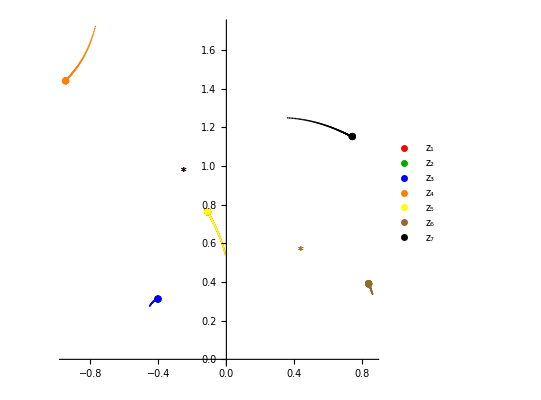

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=target//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars];
Show[plotImScalars];
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
critPoints1Sigma//Flatten//N//Max
```

1.44057

```mathematica
Table[critPoints1[[i]],{i,1,5}]//Im//N//Flatten//Max
```

1.37473

```mathematica
yEnd=yR/.{r->rmax}/.solution;
yEnd=yEnd[[1]];
yMax=Max[yEnd];
yBound=1.5;
yMax>=yBound
```

1.5

True

New distance functions!

```mathematica
getDistanceEndFlow[solution_,target_,start_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
zE=endValuesHere//cut;
beginValuesListHere=sigmaR/.{r->0}/.solution;
beginValuesHere=beginValuesListHere[[1]];
zB=beginValuesHere//cut;
zT=target//cut;
(*distanceHereSquared=Sum[ArcCosh[((zE[[2i-1]]-zT[[2i-1]])^2+zE[[2i]]^2+zT[[2i]]^2)/(2zE[[2i]]zT[[2i]])]^2,{i,1,7}];*)
(*distanceHereSquared=Sum[Log[(Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]-zT[[2i]])^2]+Sqrt[(zE[[2i-1]]-zT[[2i-1]])^2+(zE[[2i]]+zT[[2i]])^2])/(2Sqrt[zE[[2i]]*zT[[2i]]])]^2,{i,1,7}];*)
distanceHereSquared=Sum[(hyperbolicDistance[zE[[i]],zT[[i]]])^2,{i,1,7}];
distanceHere=Sqrt[distanceHereSquared];
(* In case we want to do Euclidean: *)
If[useEuclDistance==True,
(
distanceHereEnd=EuclideanDistance[endValuesHere,target];
distanceHereBegin=EuclideanDistance[beginValuesHere,start];
If[distanceBeginAndEnd==True,
(distanceHere=distanceHereEnd+distanceHereBegin;),
(distanceHere=distanceHereEnd;)];
)];
Return[distanceHere];
);
```

# Old: trying to get IC out of GS IC by comparing expansions etc

```mathematica
guarinoSterckx={re,im}//Transpose//Flatten;
```

```mathematica
(* 1.56 eigenvectors: *)
v1=guarinoSterckxLambdas/.{lambda1->0,lambda2->0,bigLambda1->1,bigLambda2->0,rvalue->0} ;(* 1.56 eigenvalue *)
v2=guarinoSterckxLambdas/.{lambda1->0,lambda2->0,bigLambda1->0,bigLambda2->1,rvalue->0};
v3=guarinoSterckxLambdas/.{lambda1->1,lambda2->0,bigLambda1->0,bigLambda2->0,rvalue->0} ;(* 0.56 eigenvalue *)
v4=guarinoSterckxLambdas/.{lambda1->0,lambda2->1,bigLambda1->0,bigLambda2->0,rvalue->0};
```

```mathematica
(* Our eigenvectors: *)
w1=eigenvecs[[7]];
w2=eigenvecs[[8]];
w3=eigenvecs[[11]];
w4=eigenvecs[[12]];
(* Make them orthonormal *)
{w1bis,w2bis}=Orthogonalize[{w1, w2}]//Chop;
{w3bis,w4bis}=Orthogonalize[{w3, w4}]//Chop;
```

```mathematica
(* Get deviations that G&S have *)
xLambda=bestBigLambda1*v1+bestBigLambda2*v2;
yLambda=bestLambda1*v3+bestLambda2*v4;
GSdeviations=xLambda+yLambda;
```

```mathematica
ICGSdeviations=ICGS-fpSigma
```

{0.000178632,0.000682107,-0.000205537,-0.0250156,0.000178632,0.000682107,0.0201196,-0.000151154,-0.00953303,0.0092208,0.0201196,-0.000151154,-0.00953303,0.0092208}

```mathematica
myDeviations=a w1 + b w2 + d w3 + e w4;
left=1;
right=6;
sol=Solve[Table[ICGSdeviations[[i]]==myDeviations[[i]],{i,left,right}],{a,b,d,e}];
solValue=sol[[1]];
myDeviations/.solValue
```

{0.000178632,0.000682107,-0.000205537,-0.0250156,0.000178632,0.000682107,0.0198256,0.0000560466,-0.0183047,0.0181378,0.0198256,0.0000560466,-0.0183047,0.0181378}

# Back-up of succesful flow in SO(1, 1) model

Expansion used:

{0.0356614 α3+0.0189679 α4,0.706906-0.000439773 α2,0.00022616-0.0000240059 α2-0.0322966 α3-0.0171782 α4,0.999889-0.000242795 α2-0.0310504 α4,0.0356614 α3+0.0189679 α4,0.706906-0.000439773 α2,0.0242434 α4,0.99971+0.0000307462 α2,0.707025+0.000188657 α2-0.0228372 α3-0.0341027 α4,0.706869-0.000154707 α2-0.0228372 α3+0.00980912 α4,0.0242434 α4,0.99971+0.0000307462 α2,0.707025+0.000188657 α2-0.0228372 α3-0.0341027 α4,0.706869-0.000154707 α2-0.0228372 α3+0.00980912 α4}

Values of parameters:

```mathematica
{6.456844878629852,-0.3388085961622639,0.6460354580856319}
```

IClist was:

```mathematica
{x1[0]==0.00017152179158568329,y1[0]==0.7040666177414023,x2[0]==-0.00008417984316806787,y2[0]==0.9782619180141329,x3[0]==0.00017152179158576135,y3[0]==0.7040666177414023,x4[0]==0.01566208674864449,y4[0]==0.9999088623501007,x5[0]==0.6939491669680303,y5[0]==0.7199440815532571,x6[0]==0.01566208674864433,y6[0]==0.9999088623501007,x7[0]==0.6939491669680303,y7[0]==0.7199440815532571}
```

How I got the first estimate:

```mathematica
(* SIMILAR BUT DONT FIX ALPHA 1 yet *)
myDeviations=check-fpSigma;
ICGSdeviations=ICGS-fpSigma;
distanceFunction=EuclideanDistance[myDeviations,ICGSdeviations]//ComplexExpand;
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0}//ComplexExpand//Simplify;
eqs={3.407186065095647*^-7+5.672686052544086*^-7 α1+2.536560838572228*^-7 α2+8.30726578220496*^-6 α3+5.071332005387692*^-7 α4==0,9.806390825552213*^-7+2.536560838572228*^-7 α1+5.672686052544257*^-7 α2-7.753087390909227*^-7 α3-7.951256400126461*^-6 α4==0,-0.00003364000803392008+8.30726578220496*^-6 α1-7.753087390909227*^-7 α2+0.005672686052544108 α3+0.003017232045893865 α4==0,-0.0025936861525326775+5.071332005387692*^-7 α1-7.951256400126461*^-6 α2+0.003017232045893865 α3+0.005672686052544321 α4==0};
```

```mathematica
eqs[[4]];
```

```mathematica
sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals]}],{α1,α2,α3,α4}];
solValue=sol[[1]]
```

{α1→0.879256,α2→6.47149,α3→-0.338097,α4→0.646045}

```mathematica
IC=check/.solValue
```

{0.000197102,0.70406,-0.000107698,0.978258,0.000197102,0.70406,0.0156623,0.999909,0.693935,0.719926,0.0156623,0.999909,0.693935,0.719926}

```mathematica
ICGS
```

{0.000178632,0.707789,-0.000205537,0.974984,0.000178632,0.707789,0.0201196,0.999849,0.697574,0.716328,0.0201196,0.999849,0.697574,0.716328}

# Bad idea dump:

## Trying something new, get an expansion around UV vacuum

```mathematica
(* Start from second point, go towards first. *)
goal=critPoints3Sigma[[1]];
target=goal; (* using these names interchangeably... *)
jacUV=jacobians3[[1]]/.{g->1};
{eigenvalsUV, eigenvecsUV}=Eigensystem[jacUV];
potentialValue=potentialValues3[[1]]/.{g->1};
LUV=Sqrt[-3/potentialValue]//N;
deltasUV=eigenvalsUV*(-LUV);
deltasUV//Sort
(* Get the critical point in the IR and an expansion around it: *)
fpSigmaUV=critPoints3Sigma[[1]];
```

{-3.03142,-2.14466,-2.14466,-1.88118,0.333333,0.333333,0.663692,1.33631,1.66667,1.66667,3.88118,4.14466,4.14466,5.03142}

```mathematica
expansion3UV=getExpansionAtUV[fpSigmaUV,eigenvalsUV,eigenvecsUV]//N;
(* Another expansion: *)
rvalueHereUV=-Log[10^-1];
check=expansion3UV/.{rvalue->rvalueHereUV};
```

```mathematica
fpSigmaUV//N
```

{0.3849,0.430331,0.3849,0.430331,0.3849,0.430331,-0.310202,0.693632,-0.310202,0.693632,-0.310202,0.693632,1.55101,0.693632}

## Find a good shooting guess from experience FROM UV

```mathematica
expansion3UVv2=check;
expansion3AllAlphas=expansion3UVv2;
eps=0.1;
startingTarget=fpSigma;
goodDirection=fpSigmaUV+eps*(startingTarget-fpSigmaUV)//N;
(*secondEps=0.5;*)
(*goodDirection[[13]]=fpSigma[[13]]+secondEps*(startingTarget[[13]]-fpSigma[[13]])//N;*)
(*goodDirection[[14]]=fpSigma[[14]]+secondEps*(startingTarget[[14]]-fpSigma[[14]])//N;*)
goodDirection
```

{0.34641,0.461834,0.34641,0.461834,0.34641,0.461834,-0.238357,0.715556,-0.238357,0.715556,-0.238357,0.715556,1.43673,0.715556}

```mathematica
expansion3AllAlphas;
```

```mathematica
myDeviations=expansion3AllAlphas;
distanceFunction=EuclideanDistance[myDeviations,goodDirection]//ComplexExpand;
eqs={D[distanceFunction,α1]==0,D[distanceFunction,α2]==0,D[distanceFunction,α3]==0,D[distanceFunction,α4]==0,D[distanceFunction,α5]==0,D[distanceFunction,α6]==0,D[distanceFunction,α7]==0,D[distanceFunction,α8]==0,D[distanceFunction,α9]==0,D[distanceFunction,α10]==0}//ComplexExpand//Simplify;
sol=Solve[Join[eqs,{Element[α1,Reals],Element[α2,Reals],Element[α3,Reals],Element[α4,Reals],Element[α5,Reals],Element[α6,Reals],Element[α7,Reals],Element[α8,Reals],Element[α9,Reals],Element[α10,Reals]}],{α1,α2,α3,α4,α5,α6,α7,α8,α9,α10}];
solValue=sol[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α1→-4.92159×10^6,α2→2.76866×10^-9,α3→-2.16569×10^-10,α4→104220.,α5→3.67176×10^-14,α6→-3.62221×10^-16,α7→4.48601,α8→0.183624,α9→-2.97178×10^-17,α10→-5.20892×10^-16}

```mathematica
pointFound=myDeviations/.solValue
Abs[pointFound-fpSigmaUV]
```

{0.34963,0.411338,0.34963,0.411338,0.34963,0.411338,-0.299006,0.726454,-0.299006,0.726454,-0.299006,0.726454,1.52677,0.677575}

{0.0352706,0.018993,0.0352706,0.018993,0.0352706,0.018993,0.0111958,0.0328224,0.0111958,0.0328224,0.0111958,0.0328224,0.02424,0.0160566}

## Test it

```mathematica
IC=pointFound;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
rmax=0.2;
solution = TimeConstrained[NDSolve[Join[flowEqs3, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],50,Print["Blew up!"]];
```

{x1[0]==0.34963,y1[0]==0.411338,x2[0]==0.34963,y2[0]==0.411338,x3[0]==0.34963,y3[0]==0.411338,x4[0]==-0.299006,y4[0]==0.726454,x5[0]==-0.299006,y5[0]==0.726454,x6[0]==-0.299006,y6[0]==0.726454,x7[0]==1.52677,y7[0]==0.677575}

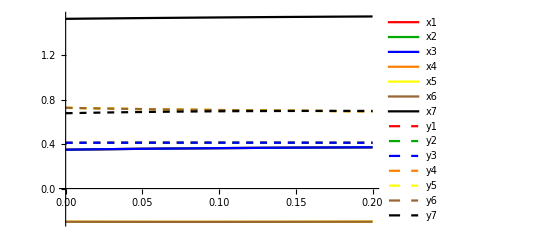

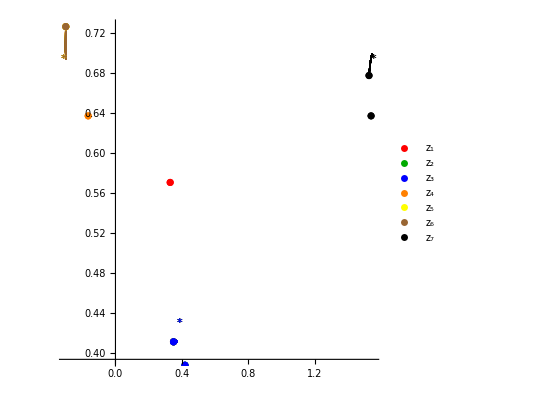

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
pointFoundCut=pointFound//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotPointFound=ListPlot[{#}&/@pointFoundCut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## MODEL 0) SO(8)

```mathematica
(* https://arxiv.org/pdf/1910.06866.pdf for points and flows already found before *)
superpotSO8=superpot/.{a->1, b->1, atilde->0,btilde->0};
potentialSO8=potential/.{a->1, b->1, atilde->0,btilde->0};
test=superpotSO8/.{g->1}//Expand;
```

```mathematica
diskCritsSO8={{0,0,0,0,0,0,0},{1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4))},{ⅈ √(5-2 √6),2-√3,ⅈ √(5-2 √6),ⅈ √(5-2 √6),ⅈ √(5-2 √6),2-√3,2-√3},{-0.48332142747953905-0.3864057693311296 ⅈ,0.3162021275491621-0.5162839349222905 ⅈ,0.16963595783412394+0.14157403013514813 ⅈ,0.16963595783412394+0.14157403013514813 ⅈ,0.16963595783412394+0.14157403013514813 ⅈ,0.3162021275491621-0.5162839349222905 ⅈ,0.3162021275491621-0.5162839349222905 ⅈ}};
(*getPlaneCritFromDisk[crit_]:=(-(t1+2I crit)/(t1- 2 I crit))/.{t1->2};*)
getPlaneCritFromDisk[crit_]:=1/(2 I)t1((crit+1)/(crit-1));
planeCritsSO8=getPlaneCritFromDisk[diskCritsSO8]//N;
```

```mathematica
planeCritsSO8;
```

```mathematica
(* Fill in the points *)
eqs=nabla[superpotSO8]/.{g->1};
check=Table[eqs/.Join[Table[z[[i]]->planeCritsSO8[[s]][[i]],{i,1,7}],Table[zb[[i]]->Conjugate[planeCritsSO8[[s]][[i]]],{i,1,7}]],{s,1,Length[planeCritsSO8]}]//N//refine//FS//Chop;
check/.{t1->2}//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0.181385+1.54247 ⅈ,1.09532-1.38725 ⅈ,-0.828427+3.65685 ⅈ,-0.828427+3.65685 ⅈ,-0.828427+3.65685 ⅈ,1.09532-1.38725 ⅈ,1.09532-1.38725 ⅈ},{-17.3723-17.7065 ⅈ,-11.3516-1.93965 ⅈ,2.66027-6.91892 ⅈ,2.66027-6.91892 ⅈ,2.66027-6.91892 ⅈ,-11.3516-1.93965 ⅈ,-11.3516-1.93965 ⅈ}}

```mathematica
check[[3]];
```

```mathematica
Solve[(0.5756764089969328+1.8856180831641323 ⅈ) t1^2-(0.03314563036811924+0.09375000000000025 ⅈ) t1^6==0,t1];
```

```mathematica
(* Now for potential *)
eqs=Table[D[potentialSO8,z[[i]]],{i,1,7}];
check=Table[eqs/.Join[Table[z[[i]]->planeCritsSO8[[s]][[i]],{i,1,7}],Table[zb[[i]]->Conjugate[planeCritsSO8[[s]][[i]]],{i,1,7}]],{s,1,Length[planeCritsSO8]}]//N//refine//FS//Chop;
check/.{t1->2}//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0.375-0.53033 ⅈ,-0.166667+0.221405 ⅈ,0.369586-0.541667 ⅈ,0.369586-0.541667 ⅈ,0.369586-0.541667 ⅈ,-0.166667+0.221405 ⅈ,-0.166667+0.221405 ⅈ},{28.9297+35.9663 ⅈ,7.9923+10.7165 ⅈ,-8.24474+0.191942 ⅈ,-8.24474+0.191942 ⅈ,-8.24474+0.191942 ⅈ,7.9923+10.7165 ⅈ,7.9923+10.7165 ⅈ}}

```mathematica
check[[3]]
```

{((0.375-2.51907 ⅈ)+(0.28125+0.0994369 ⅈ) t1^4-(0.0131836+0.0046611 ⅈ) t1^8)/t1^2,((-0.291667-0.298202 ⅈ)-(0.0234375-0.179458 ⅈ) t1^4-(0.+0.0065918 ⅈ) t1^8)/t1^2,((0.171362-2.62875 ⅈ)+(0.292624+0.103458 ⅈ) t1^4-(0.0131836+0.0046611 ⅈ) t1^8)/t1^2,((0.171362-2.62875 ⅈ)+(0.292624+0.103458 ⅈ) t1^4-(0.0131836+0.0046611 ⅈ) t1^8)/t1^2,((0.171362-2.62875 ⅈ)+(0.292624+0.103458 ⅈ) t1^4-(0.0131836+0.0046611 ⅈ) t1^8)/t1^2,((-0.291667-0.298202 ⅈ)-(0.0234375-0.179458 ⅈ) t1^4-(0.+0.0065918 ⅈ) t1^8)/t1^2,((-0.291667-0.298202 ⅈ)-(0.0234375-0.179458 ⅈ) t1^4-(0.+0.0065918 ⅈ) t1^8)/t1^2}

## When not considering the simpler parametrization

```mathematica
zeta={ζ1,ζ2,ζ3,ζ4,ζ5,ζ6,ζ7};
zetab={ζb1,ζb2,ζb3,ζb4,ζb5,ζb6,ζb7};
kahlerPotDisk=- Sum[Log[1-zeta[[i]]zetab[[i]]],{i,1,Length[z]}];
superpotDisk= zeta[[1]] zeta[[2]]zeta[[3]] zeta[[4]]zeta[[5]]zeta[[6]]zeta[[7]] + zeta[[1]]zeta[[2]]zeta[[3]] zeta[[7]]+ zeta[[1]]zeta[[2]]zeta[[5]] zeta[[6]] + zeta[[1]]zeta[[3]]zeta[[4]] zeta[[5]]+ zeta[[1]]zeta[[4]]zeta[[6]] zeta[[7]]+ zeta[[2]]zeta[[3]] zeta[[4]]zeta[[6]]+ zeta[[2]] zeta[[4]]zeta[[5]]zeta[[7]]+ zeta[[3]] zeta[[5]]zeta[[6]]zeta[[7]]+zeta[[1]]zeta[[2]]zeta[[4]] +zeta[[1]]zeta[[3]]zeta[[6]]+zeta[[1]]zeta[[5]]zeta[[7]] +zeta[[2]]zeta[[6]]zeta[[7]]+zeta[[2]]zeta[[3]]zeta[[5]]+zeta[[3]]zeta[[4]]zeta[[7]]   +zeta[[4]]zeta[[5]]zeta[[6]] + 1;
```

```mathematica
zeta2zRule[f_]:=(f/.Join[Table[zeta[[i]]->-(t1+2 I z[[i]])/(t1-2 I z[[i]]),{i,1,7}],Table[zetab[[i]]->-(t1-2 I zb[[i]])/(t1+2 I zb[[i]]),{i,1,7}]])
```

```mathematica
kahlerPotDiskMapped=kahlerPotDisk//zeta2zRule;
superpotDiskMapped=superpotDisk//zeta2zRule;
```

```mathematica
nablaNew[f_]:= Table[D[f,z[[i]]] + f*D[kahlerPotDiskMapped,z[[i]]],{i,1,Length[z]}];
nablaBarNew[f_]:= Table[D[f,zb[[i]]] + f*D[kahlerPotDiskMapped,zb[[i]]],{i,1,Length[zb]}];
```

```mathematica
eqs=nablaNew[superpotDiskMapped];
```

```mathematica
(* Fill in the points *)
check=Table[eqs/.Join[Table[z[[i]]->planeCritsSO8[[s]][[i]],{i,1,7}],Table[zb[[i]]->Conjugate[planeCritsSO8[[s]][[i]]],{i,1,7}]],{s,1,Length[planeCritsSO8]}]//N//refine//FS//Chop;
check/.{t1->2}//N//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
Solve[check[[2]][[1]]==0,t1]
```

{{}}

## Is it easy to find the critical points in the plane?

```mathematica
eqs=nabla[superpotSO8]/.{g->1};
eqsRF=eqs//complexToRealScalars//ComplexExpand;
eqsRe=Re[eqsRF]//ComplexExpand//Simplify;
eqsIm=Im[eqsRF]//ComplexExpand//Simplify;
eqsToSolve=Join[eqsRe,eqsIm];
```

```mathematica
toSolve=Table[eqsToSolve[[i]]==0,{i,1,Length[sigma]}];
```

```mathematica
Solve[toSolve,sigma,Assumptions->assumptions]
```

$Aborted

## Get BPS equations

```mathematica
Exp[kahlerpot/2]//Expand
```

ⅇ^(1/2 (-Log[-ⅈ (z1-zb1)]-Log[-ⅈ (z2-zb2)]-Log[-ⅈ (z3-zb3)]-Log[-ⅈ (z4-zb4)]-Log[-ⅈ (z5-zb5)]-Log[-ⅈ (z6-zb6)]-Log[-ⅈ (z7-zb7)]))

```mathematica
(* Taken from arXiv:1909.10969v2 *)
sign=-1;
factor=1;
(* Save a variable with the superpotential but with m = g = 1 *)
superpotSO82=superpotSO8/.{g->1};
```

```mathematica
zprimeSuperpotentialPart=ComplexExpand[complexToRealScalars[superpotSO82]]/Conjugate[ComplexExpand[complexToRealScalars[superpotSO82]]]//ComplexExpand;
(*zprimeT=sign*factor*ComplexExpand[complexToRealScalars[Exp[kahlerpot]]]*zprimeSuperpotentialPart//ComplexExpand //Simplify;*)
zprimeT=Get["zprimeT"];
```

```mathematica
invMetric=Inverse[kahlerMetric]//complexToRealScalars//ComplexExpand//FS;
```

```mathematica
nablaPart=nablaBar[conjugate[superpotSO82]]//complexToRealScalars//ComplexExpand//Simplify;
```

```mathematica
zprimeS=Table[Sum[invMetric[[a]][[b]]*nablaPart[[b]],{b,1,7}],{a,1,7}]//ComplexExpand//Simplify;
```

```mathematica
zprime=Sqrt[zprimeT]*zprimeS;
Put[zprime,"zprime"]
```

```mathematica
xprime=Re[zprime]//ComplexExpand
```

{1/(2 √2)x2 x3 y1^2 √((√1)/1) Cos[1/2 Arg[(ⅈ (x1 (x4 x7+ⅈ x3 y2-y2 y3+29+x5 (x6+ⅈ y6) (1-ⅈ x7 y2 y3 y4-x4 y2 y3 (x7+ⅈ y7)+ⅈ x3 y2 (x4+ⅈ y4) (x7+ⅈ y7)+y2 y3 y4 y7)+x2 (x3+ⅈ y3) (1-x6 x7 y4 y5-ⅈ x7 y4 y5 y6+ⅈ x5 y4 (x6+ⅈ y6) (x7+ⅈ y7)+x4 (x5+ⅈ y5) (x6+ⅈ y6) (x7+ⅈ y7)-ⅈ x6 y4 y5 y7+y4 y5 y6 y7))+ⅈ (1)))/(y1 y2 4 y7 (-x3 (x2 y1-ⅈ y1 y2+x5 y4-ⅈ y4 y5+x7 y6-x2 x5 x7 y1 y4 y6+ⅈ x5 x7 y1 y2 y4 y6+6+ⅈ x2 x5 y1 y4 y6 y7+x5 y1 y2 y4 y6 y7+x2 y1 y4 y5 y6 y7-ⅈ y1 y2 y4 y5 y6 y7+x4 (x5-ⅈ y5) (ⅈ-x7 y1 y2 y6+x6 y1 y2 (-ⅈ x7-y7)+x2 y1 (x6-ⅈ y6) (x7-ⅈ y7)+ⅈ y1 y2 y6 y7))+ⅈ (1)+x1 (1)))]]+(x5 x6 y1^2 √((√1)/1) Cos[1/2 Arg[(ⅈ (x1 (1)+ⅈ (1)))/(y1 6 (-x3 (1)+ⅈ 1+x1 1))]])/(2 √2)+(x4 3 Cos[1/2 Arg[1]])/(2 √2)+276+1/(2 1)+1/(2 √2)+(x2 y1^2 5 √(1/1) Sin[1/2 Arg[(ⅈ (1))/(y1 6 (1))]])/(2 √2)-(x1 y1 y2 4 y7 √((√1)/1) Sin[1/2 Arg[(ⅈ (x1 (x4 x7+33+x2 (1) (1-x6 x7 y4 y5-ⅈ x7 y4 y5 y6+1+1-ⅈ x6 y4 y5 y7+y4 y5 y6 y7))+1))/(y1 y2 5 (-x3 (1)+ⅈ 1+x1 (-x5 (x6-ⅈ y6) (5+ⅈ y2 y3 y4 y7)+x2 (1) (1)+ⅈ (y2 y3+12))))]])/(2 √2),5,1}
 |  |  |  |

```mathematica
yprime=Im[zprime]//ComplexExpand
```

{1,268+1/(2 √2)-(x1 9)/(2 √2)-(y1 y2^2 y3 y4 y5 y6 y7 √((√1)/1) Sin[1/2 Arg[(ⅈ (1))/(y1 7)]])/(2 √2),270+1/1-(y1 7 Sin[1])/(2 √2),1,1,270+1/(2 √2)-(y1 7 Sin[1/2 Arg[1/1]])/(2 √2),269+1/(2 √2)+(x1 x2 5 √1 Sin[1/2 Arg[1]])/(2 √2)-(y1 y2 y3 y4 y5 y6 y7^2 √((√1)/1) Sin[1/2 Arg[(ⅈ (x1 (x4 x7+33+1)+ⅈ 1))/(y1 6 (-x3 (21+1)+ⅈ 1+x1 1))]])/(2 √2)}
 |  |  |  |

```mathematica
Put[xprime, "xprime"]
Put[yprime, "yprime"]
```

```mathematica
(* Get the xprime and yprime equations from earlier: *)
xprime=Get["xprime"];
yprime=Get["yprime"];
sigmaprime={xprime,yprime}//Transpose//Flatten;
```

```mathematica
(* Get the jacobian - takes a few hours *)
jacobian0=Table[Table[D[sigmaprime[[i]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}]//refine;  
Put[jacobian0, "jacobian0"]
```

$Aborted

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
(* jacobian1 = Get["jacobian0"]; *)
```

```mathematica
xprime0[[1]]
```

1256+1+(16 x1 x2^2 y1^2 y3^2 1 y5^2 y6^2 y7^2 Sinh[1/2 (Log[2]+Log[y1])+5+1/2 (Log[2]+Log[y7])])/(√((2 (1)+1+1)^2+(1)^2))+(16 x1 y1^2 y2^2 y3^2 y4^2 y5^2 y6^2 y7^2 Sinh[1/2 (Log[2]+Log[y1])+1/2 (Log[2]+Log[y2])+1/2 (Log[2]+Log[y3])+1/2 (Log[2]+Log[y4])+1/2 (Log[2]+Log[y5])+1/2 (Log[2]+Log[y6])+1/2 (Log[2]+Log[y7])])/(√((2 (x3 x4 x5+x2 x4 x6+x1 x5 x6+x1 x4 x7+x2 x5 x7+37)+(1) (1)+(2 x1 x2 x3-2 x3 y1 y2-2 x2 y1 y3-2 x1 y2 y3) (1+x7 (1)+(-x5 x6 y4-x4 x6 y5-x4 x5 y6+y4 y5 y6) y7))^2+(1)^2))
 |  |  |  |

#### The old method:

```mathematica
sign=-1;
factor=1;
superpotSO82=superpotSO8/.{g->1};
zprime0Part1=Table[sign*factor*Exp[kahlerpot/2]*(superpotSO82/Abs[superpotSO82])*Sum[Inverse[kahlerMetric][[a]][[b]]*nablaBar[conjugate[superpotSO82]][[b]],{b,1,Length[z]}],{a,1,Length[z]}]//complexToRealScalars//refine//ExpToTrig;
```

```mathematica
zprime0=Assuming[assumptions,ComplexExpand[zprime0Part1]]//refine;
xprime0=ComplexExpand[Re[zprime0]]//refine;
Put[xprime0,"xprime0"];
yprime0=ComplexExpand[Im[zprime0]]//refine;
Put[yprime0,"yprime0"];
sigmaprime0={xprime0,yprime0}//Transpose//Flatten;
```

```mathematica
jacobian0v2=Table[Table[D[sigmaprime0[[i]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}]//refine;
Put[jacobian0v2,"jacobian0v2"]
```

$Aborted

```mathematica
(*jacobian1=Get["jacobian1"];*)
```

# A dump from model 2:

### Part 4) Completely rethink the algorithm - version 6

#### Step 1) Find a good initial point by hand

```mathematica
(* Get the critical point in the IR and an expansion around it: *)
index=2;
fp = critPoints2FamilyI/.{c->1,chi->0};
fpRe=Re[fp];
fpIm=Im[fp];
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
(* Get 1/L: appears in the expansion *)
invLengthScaleStart=inverseLengthScales2[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians2[[index]]; 
{eigenvals,eigenvecs}=jac//Eigensystem//FS;
Clear[rvalue];
expansion2Crit1=getExpansion[fpSigma,invLengthScaleStart,eigenvals,eigenvecs];
(* expansion2Crit1FS=getExpansion[fpSigma,invLengthScaleStart,eigenvals,eigenvecs]//FS;*)
(* Can put one constant as desired WLOG *)
expansion2Crit1Rescaled=expansion2Crit1/.{α1->1,rvalue->Log[10^-5]};
(* These are the modes that we are going to finetune *)
{eigenvecs[[7]],eigenvecs[[8]],eigenvecs[[11]],eigenvecs[[12]]};
```

```mathematica
expansion2Crit1Rescaled//N
```

{0.000553148 α3+0.000553148 α4,0.707107+7.08459×10^-9 α2,3.91135×10^-9+3.91135×10^-9 α2-0.000500956 α3-0.000500956 α4,1.+3.91135×10^-9 α2+0.000500956 α3-0.000500956 α4,0.000553148 α3+0.000553148 α4,0.707107+7.08459×10^-9 α2,-0.000391135 α3+0.000391135 α4,1.-5.00956×10^-9 α2,0.707107-5.53148×10^-9 α2-0.000708459 α4,0.707107-0.000708459 α3,-0.000391135 α3+0.000391135 α4,1.-5.00956×10^-9 α2,0.707107-5.53148×10^-9 α2-0.000708459 α4,0.707107-0.000708459 α3}

```mathematica
(* The goal we want to reach - took a guess for chi1, chi2 from Guarino and Sterckx --- 0,-1.65,-2.1*)
goal=critPoints2Sigma[[1]]/.{c->1,g->1,chi1->0,chi2->0};
(* We are starting from chi = 0 in the IR: *)
start=critPoints2Sigma[[2]]/.{c->1,g->1,chi->0};
```

```mathematica
(* Take angles, return a point on the 2-sphere *)
alphaRadius=1;
getSphericalCoordinates[d_,thetas_]:=(
If[d==3,
(Return[{alphaRadius*Cos[thetas[[2]]]*Sin[thetas[[1]]],alphaRadius*Sin[thetas[[2]]]*Sin[thetas[[1]]],alphaRadius*Cos[thetas[[1]]]}]
)];
If[d==4,
(Print["Not implemented yet!"];
Return[Null]
)];
);
```

```mathematica
(* Get IC ready *)
numberOfParams=2;
startIndex=2;
thetas={1,1};
ansatz=getSphericalCoordinates[3,thetas];
(* Save the expansion we are going to use - i.e. we choose an epsilon value here *)
expansionNew=expansion2Crit1Rescaled//N;
IC =expansionNew /.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC- fpSigma]
StringForm["Largest distance between FP and IC is ``",Max[Abs[IC- fpSigma]]]
```

{x1[0]==0.000690537,y1[0]==0.707107,x2[0]==-0.000625376,y2[0]==1.00008,x3[0]==0.000690537,y3[0]==0.707107,x4[0]==-0.0000656211,y4[0]==1.,x5[0]==0.706724,y5[0]==0.706605,x6[0]==-0.0000656211,y6[0]==1.,x7[0]==0.706724,y7[0]==0.706605}

{0.000690537,3.86359×10^-9,0.000625376,0.0000840438,0.000690537,3.86359×10^-9,0.0000656211,7.28715×10^-9,0.000382785,0.000501647,0.0000656211,7.28715×10^-9,0.000382785,0.000501647}

Largest distance between FP and IC is 0.000690537

#### Start - version 6 of the algorithm!

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
rmax=15;
```

```mathematica
getGridForAngles[d_, minAngles_,maxAngles_,numberOfIterations_]:=(
numberOfAngles=d-1;
returnValueHere={};
ranges=maxAngles-minAngles;
For[i=1,i<numberOfAngles+1,i++,
(
stepSizeTheta=(ranges[[i]]-2eps)/numberOfIterations;
anglesListHere=Range[minAngles[[i]]+eps,maxAngles[[i]]-eps, stepSizeTheta];
AppendTo[returnValueHere,anglesListHere];
)
];
gridHere=Tuples[returnValueHere];
Return [gridHere];
)
```

```mathematica
minAngles={5,0};
maxAngles={2 Pi, Pi};
test=getGridForAngles[3,minAngles,maxAngles, 20];
test2=test/.{eps->0.001};
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansionNew;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=2; (* params are angles here *)
startIndex=2;
(* Time limit for an individual integration *)
timeLimit=60;
rmax=15;
allExplorations=Association[rmax->Association[]];
(* Set up the grid of angles *)
numberOfIterations=10;
expectedTime=numberOfIterations^(numberOfParams)*timeLimit/3600//N;
(* Get the grid for the angles *)
explorationAngles={6.0259482457436695,0.6289185307179587};
explorationRange=0.25;
minAngles=explorationAngles-explorationRange;
maxAngles=explorationAngles+explorationRange;
eps=0.001;
(* Note: the following function uses eps!!! *)
gridAngles=getGridForAngles[3,minAngles,maxAngles, numberOfIterations];
(* Do the flows *)
Timing[
Print[StringForm["Shooting everywhere for rmax = `` . . . ",rmax]];
dtheta=Max[Abs[gridAngles[[1]]-gridAngles[[2]]]];
Print[StringForm["Number of iterations: ``, dθ: `` time limit: ``, upper bound runtime: `` hours", numberOfIterations, dtheta,timeLimit, expectedTime]];
For[i=1,i<Length[gridAngles]+1,i++,
(
(* Get angles from the grid *)
thetas=gridAngles[[i]];
Print[StringForm["Current angles: ``", thetas]];
(* Transfer angles to alpha values on unit n-sphere *)
ansatz=getSphericalCoordinates[3,thetas];
Print[StringForm["Parameter values: ``", ansatz]];
(* Integrate within the time limit, and see if we have a distance or not *)
distance=TimeConstrained[doRGFlowGetDistance[ansatz],timeLimit,10^8];
AppendTo[allExplorations,Association[thetas->distance]];
)
];
Print["THE END"];
]
```

Shooting everywhere for rmax = 15 . . .

Number of iterations: 10, dθ: 2.77595 time limit: 60, upper bound runtime: 1.66667 hours

Current angles: 3

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

Part::partd: Part specification 3⟦1⟧ is longer than depth of object.

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Parameter values: {Cos[3⟦2⟧] Sin[3⟦1⟧],Sin[3⟦1⟧] Sin[3⟦2⟧],Cos[3⟦1⟧]}

$Aborted

### Part 5) Completely rethink the algorithm - version 8

#### Step 1) Find a good initial point by hand

```mathematica
(* Get the critical point in the IR and an expansion around it: *)
index=2;
fp = critPoints2FamilyI/.{c->1,chi->0};
fpRe=Re[fp];
fpIm=Im[fp];
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
(* Get 1/L: appears in the expansion *)
invLengthScaleStart=inverseLengthScales2[[index]];
(* Get the jacobian matrix and use it to get the linearization around the vacuum *)
jac=jacobians2[[index]]; 
{eigenvals,eigenvecs}=jac//Eigensystem//FS;
Clear[rvalue];
expansion2Crit1=getExpansion[fpSigma,invLengthScaleStart,eigenvals,eigenvecs];
(* Can put one constant as desired WLOG *)
expansion2Crit1Rescaled=expansion2Crit1/.{α1->1,rvalue->Log[10^-2]};
(* These are the modes that we are going to finetune *)
{eigenvecs[[7]],eigenvecs[[8]],eigenvecs[[11]],eigenvecs[[12]]};
expansion2Crit1Rescaled//N
```

{0.0267608 α3+0.0267608 α4,0.706764+0.000342747 α2,0.000189228+0.000189228 α2-0.0242358 α3-0.0242358 α4,0.999811+0.000189228 α2+0.0242358 α3-0.0242358 α4,0.0267608 α3+0.0267608 α4,0.706764+0.000342747 α2,-0.0189228 α3+0.0189228 α4,0.999758-0.000242358 α2,0.707107-0.000267608 α2-0.0342747 α4,0.706839-0.0342747 α3,-0.0189228 α3+0.0189228 α4,0.999758-0.000242358 α2,0.707107-0.000267608 α2-0.0342747 α4,0.706839-0.0342747 α3}

```mathematica
(* The goal we want to reach - took a guess for chi1, chi2 from Guarino and Sterckx --- 0,-1.65,-2.1*)
goal=critPoints2Sigma[[1]]/.{c->1,g->1,chi1->0,chi2->0};
(* We are starting from chi = 0 in the IR: *)
start=critPoints2Sigma[[2]]/.{c->1,g->1,chi->0};
```

```mathematica
(* Get IC ready *)
numberOfParams=3;
startIndex=2;
ansatz={0,0,0};
ansatz={-5.316683953,-0.6433641476999997,0.8673828123999998};
(* Save the expansion we are going to use - i.e. we choose an epsilon value here *)
expansionNew=expansion2Crit1Rescaled//N;
IC =expansionNew /.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
IClist
Abs[IC- fpSigma]
StringForm["Largest distance between FP and IC is ``",Max[Abs[IC- fpSigma]]]
```

{x1[0]==0.00599493,y1[0]==0.704942,x2[0]==-0.00624612,y2[0]==0.96219,x3[0]==0.00599493,y3[0]==0.704942,x4[0]==0.0285875,y4[0]==1.00105,x5[0]==0.6788,y5[0]==0.72889,x6[0]==0.0285875,y6[0]==1.00105,x7[0]==0.6788,y7[0]==0.72889}

{0.00599493,0.00216502,0.00624612,0.0378095,0.00599493,0.00216502,0.0285875,0.00104618,0.0283065,0.0217835,0.0285875,0.00104618,0.0283065,0.0217835}

Largest distance between FP and IC is 0.0378095

```mathematica
(* Solve - rmax is for the range of r *)
rmax=20;
Timing[
solution = TimeConstrained[NDSolve[Join[flowEqs2, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];]
```

NDSolve::precw: The precision of the differential equation ({{Divide[16 Cosh[Divide[Log[2] + Log[y1[r]], 2] + Divide[Log[2] + Log[y2[r]], 2] + Divide[Log[2] + Log[y3[r]], 2] + <<2>> + Divide[<<2>>] + Divide[Log[2] + Log[y7[r]], 2]] <<2>> Power[y1[r], 2], <<1>>] + <<200>> == 0, <<27>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

{14.5258,Null}

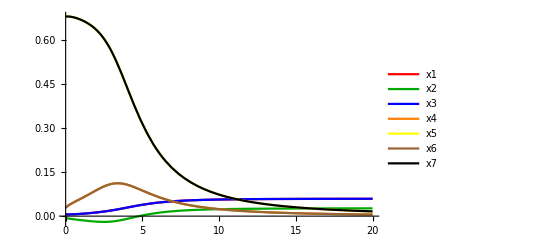

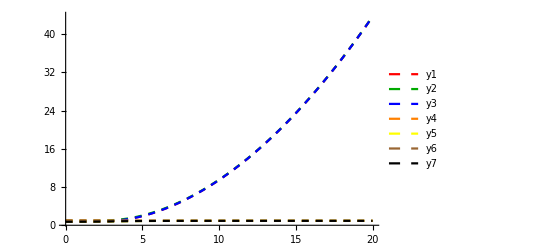

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,Length[sigmaR]}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,Length[xR]}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,Length[yR]}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
plotIC=ListPlot[IC//cut,PlotStyle->colorsRF];
plotGoal=ListPlot[goal//cut,PlotStyle->colorsRF];
(* Show desired plots *)
Show[plotReScalars]
Show[plotImScalars]
```

```mathematica
(* Save this initial guess *)
distance=getDistanceEndAndStartFlow[solution,goal,start];
ansatzValues={α2,α3,α4}/.getAlphaRule[ansatz];
allExplorations=Association[ansatzValues->distance]
```

<|{-5.31668,-0.543364,0.967383}→74.41125062525188685744175086857659943750452603504|>

#### Start - version 8 of the algorithm!

```mathematica
(* Turn off a certain message *)
Off[NDSolve::precw]
rmax=20;
```

```mathematica
(* Define expansion & flow eqs to be used *)
expansion=expansionNew;
flowEqs=flowEqs2;
(* --- Initializations --- *)
numberOfParams=3;
startIndex=2;
(* Step size info *)
initialStepSize=0.1;
stepSizeFactorDecrease=1/10;
initialStepSizeFactorDecrease=0.75;
thresholdStepSize=10^-8;
numberOfIterations=200;
iterationsCount=0;
(* Thresholds *)
timeLimit=50;
exploredParamVals={};
Clear[previousMinimalValueKey];(* for debugging... *)
Timing[
firstRound=True;
(* Get the current best: *)
newMinimalValueKeyRound=Keys[MinimalBy[Value][allExplorations]][[1]];
newMinimalValueRound=allExplorations[newMinimalValueKey];
While[iterationsCount<=numberOfIterations,
(
Print[StringForm["Iteration: ``/``",iterationsCount,numberOfIterations]];
If[Not[firstRound],
(
If[newMinimalValueKey==newMinimalValueKeyRound,(
initialStepSize=initialStepSize*initialStepSizeFactorDecrease;
Print[StringForm["No improvement. Reducing initial step size to ``",initialStepSize]];
)]
)];
(* Explore the nearest neighbours *)
For[p=1,p<numberOfParams+1,p++,(
stepSize=initialStepSize;
(* Get the current best: *)
newMinimalValueKey=Keys[MinimalBy[Value][allExplorations]][[1]];
newMinimalValue=allExplorations[newMinimalValueKey];
Print[StringForm["Current best: ``. Distance: ``.",newMinimalValueKey,newMinimalValue]];
(* Current direction & unit vector in that direction *)
currentIndex=p;
Print[StringForm["Parameter: ``.",currentIndex]];
unitVector=Table[0,numberOfParams];
unitVector[[currentIndex]]=1;
upParamValues=newMinimalValueKey +stepSize*unitVector;
downParamValues=newMinimalValueKey -stepSize*unitVector;
(* Go up: keep dividing step count until we hit a new spot *)
Print["Going up"];
While[stepSize>=thresholdStepSize &&upFound==False,
(
If[MemberQ[exploredParamVals,upParamValues],
(
stepSize=stepSize*stepSizeFactorDecrease;
Print[StringForm["Already explored. Step size is now:",stepSize]];
If[stepSize<thresholdStepSize,
(
upFound=False;
Print["No valid up direction found."]
)
];
),
(
upFound=True;
)
];
)
];
If[upFound==True,
(
ansatz=upParamValues;
Print[StringForm["Parameter values: ``.",ansatz]];
upDistance=TimeConstrained[doRGFlowGetDistanceVersion2[ansatz],timeLimit,10^(8)];
AppendTo[allExplorations,Association[ansatz->upDistance]];
AppendTo[exploredParamVals,ansatz];
)
];
(* Go down: keep dividing step count until we hit a new spot *)
Print["Going down"];
While[stepSize>=thresholdStepSize &&downFound==False,
(
If[MemberQ[exploredParamVals,downParamValues],
(
stepSize=stepSize*stepSizeFactorDecrease;
Print[StringForm["Already explored. Step size is now:",stepSize]];
If[stepSize<thresholdStepSize,
(
downFound=False;
Print["No valid down direction found."]
)
];
),
(
downFound=True;
)
];
)
];
If[downFound==True,
(
ansatz=downParamValues;
Print[StringForm["Parameter values: ``.",ansatz]];
downDistance=TimeConstrained[doRGFlowGetDistanceVersion2[ansatz],timeLimit,10^(8)];
AppendTo[allExplorations,Association[ansatz->downDistance]];
AppendTo[exploredParamVals,ansatz];
)
];
)];
(* Improved all parameters, round is complete *)
Print["Round complete."];
iterationsCount+=1;
firstRound=False;
previousMinimalValueKey=newMinimalValueKey;
)];
Print["The End"];
];
```

## (Abandoned) Get and save at arbitrary values for chi:

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2FamilyI;
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine//ComplexExpand
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(*jac=jacobian2//evalatFP//ComplexExpand;*)
(*jacv2=jac//N//Chop//ComplexExpand//Simplify//ComplexExpand//Chop;*)
(*jacv2=jac//ComplexExpand//Chop;*)
(*Put[jac,"jacAtAnyChi"];*)
(*jacEigensystem=jac//Eigensystem//Chop;*)
(*{eigenvals, eigenvecs}=jacEigensystem;*)
```

{-chi,1/(√2),0,1,chi,1/(√2),0,1,1/(√2),1/(√2),0,1,1/(√2),1/(√2)}

$Aborted

```mathematica
(*charEquation=Det[jacv2-lambda*DiagonalMatrix[Table[1,14]]]//Chop;*)
(*eigenvalsSelf=Solve[{charEquation==0,lambda ∈Reals},lambda]*)
(*charEquationNumerator=Numerator[charEquation];*)
```

## To play around and look at eigenvectors:

```mathematica
(* Check the deltas for a specific matrix *)
fp = critPoints2FamilyI;
(* Choose a specific value for chi OR phi (I vs II) *)
chiValue=0.1;
fp=fp/.{chi->chiValue,phi->chiValue}
potentialValue=-3 g^2/c;
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten//refine;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
jac=jacobian2//evalatFP;
jac=jac//N//Chop;
{eigenvals, eigenvecs}=jac//Eigensystem//Chop;
(* For the results obtained at chi = phi = 0: save them *)
(*{eigenvalsAtOrigin, eigenvecsAtOrigin}={eigenvals, eigenvecs};*)
eigenvals//Sort
```

{-0.1+0.707107 ⅈ,ⅈ,0.1+0.707107 ⅈ,ⅈ,(1+ⅈ)/(√2),ⅈ,(1+ⅈ)/(√2)}

Set::shape: Lists {eigenvals,eigenvecs} and Eigensystem[jacobian2] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[eigenvals].

Sort[eigenvals]

```mathematica
eigenvals
eigenvecs;
{eigenvecs[[7]],eigenvecs[[8]],eigenvecs[[11]],eigenvecs[[12]],eigenvecs[[13]]}
```

eigenvals

Part::partd: Part specification eigenvecs⟦7⟧ is longer than depth of object.

Part::partd: Part specification eigenvecs⟦8⟧ is longer than depth of object.

Part::partd: Part specification eigenvecs⟦11⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{eigenvecs⟦7⟧,eigenvecs⟦8⟧,eigenvecs⟦11⟧,eigenvecs⟦12⟧,eigenvecs⟦13⟧}

```mathematica
eigenvalsAtOrigin
eigenvecsAtOrigin;
{eigenvecsAtOrigin[[7]],eigenvecsAtOrigin[[8]],eigenvecsAtOrigin[[11]],eigenvecsAtOrigin[[12]],eigenvecsAtOrigin[[13]]}
```

eigenvalsAtOrigin

Part::partd: Part specification eigenvecsAtOrigin⟦7⟧ is longer than depth of object.

Part::partd: Part specification eigenvecsAtOrigin⟦8⟧ is longer than depth of object.

Part::partd: Part specification eigenvecsAtOrigin⟦11⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{eigenvecsAtOrigin⟦7⟧,eigenvecsAtOrigin⟦8⟧,eigenvecsAtOrigin⟦11⟧,eigenvecsAtOrigin⟦12⟧,eigenvecsAtOrigin⟦13⟧}

```mathematica
(*Put[eigenvalsAtOrigin,"eigenvalsAtOrigin"]*)
(*Put[eigenvecsAtOrigin,"eigenvecsAtOrigin"]*)
```